numeric simulation

```mathematica
Quit[]
```

```mathematica
dispSimp = {a_[t]->a,Cos[a_]->c[a],Sin[a_]->s[a],Subscript[ⅈ, i_,zz]->Subscript[I, i]};
```

original equations:

```mathematica
(quadEqNominal=EulerEquations[L,{(*Subscript[x, 1][t],Subscript[y, 1][t],Subscript[θ, 1][t],Subscript[x, 2][t],Subscript[y, 2][t],Subscript[θ, 2][t],*)Subscript[x, p][t],Subscript[y, p][t],Subscript[θ, p][t]},t](*[[All,1]]*)(*==Q*)//Simplify)//MatrixForm//TraditionalForm
```

((k_1 (h_p sin(θ_p(t))+l_p cos(θ_p(t))-2 x_p(t)+2 x_1(t)) (√(1/4 (h_p sin(θ_p(t))+l_p cos(θ_p(t))-2 x_p(t)+2 x_1(t))^2+(1/2 h_p cos(θ_p(t))-1/2 l_p sin(θ_p(t))+y_p(t)-y_1(t))^2)-L0_1))/(2 √(1/4 (h_p sin(θ_p(t))+l_p cos(θ_p(t))-2 x_p(t)+2 x_1(t))^2+(1/2 h_p cos(θ_p(t))-1/2 l_p sin(θ_p(t))+y_p(t)-y_1(t))^2))+(k_2 (1/2 h_p sin(θ_p(t))-1/2 l_p cos(θ_p(t))-x_p(t)+x_2(t)) (√((1/2 h_p sin(θ_p(t))-1/2 l_p cos(θ_p(t))-x_p(t)+x_2(t))^2+1/4 (h_p cos(θ_p(t))+l_p sin(θ_p(t))+2 y_p(t)-2 y_2(t))^2)-L0_2))/(√((1/2 h_p sin(θ_p(t))-1/2 l_p cos(θ_p(t))-x_p(t)+x_2(t))^2+1/4 (h_p cos(θ_p(t))+l_p sin(θ_p(t))+2 y_p(t)-2 y_2(t))^2))==m_p x_p''(t)
(k_1 (-1/2 h_p cos(θ_p(t))+1/2 l_p sin(θ_p(t))-y_p(t)+y_1(t)) (√(1/4 (h_p sin(θ_p(t))+l_p cos(θ_p(t))-2 x_p(t)+2 x_1(t))^2+(1/2 h_p cos(θ_p(t))-1/2 l_p sin(θ_p(t))+y_p(t)-y_1(t))^2)-L0_1))/(√(1/4 (h_p sin(θ_p(t))+l_p cos(θ_p(t))-2 x_p(t)+2 x_1(t))^2+(1/2 h_p cos(θ_p(t))-1/2 l_p sin(θ_p(t))+y_p(t)-y_1(t))^2))+(k_2 (-1/2 h_p cos(θ_p(t))-1/2 l_p sin(θ_p(t))-y_p(t)+y_2(t)) (√((1/2 h_p sin(θ_p(t))-1/2 l_p cos(θ_p(t))-x_p(t)+x_2(t))^2+1/4 (h_p cos(θ_p(t))+l_p sin(θ_p(t))+2 y_p(t)-2 y_2(t))^2)-L0_2))/(√((1/2 h_p sin(θ_p(t))-1/2 l_p cos(θ_p(t))-x_p(t)+x_2(t))^2+1/4 (h_p cos(θ_p(t))+l_p sin(θ_p(t))+2 y_p(t)-2 y_2(t))^2))==m_p (g+y_p''(t))
ⅈ_(p,zz) θ_p''(t)+(k_1 (h_p (x_1(t) cos(θ_p(t))-x_p(t) cos(θ_p(t))+(y_1(t)-y_p(t)) sin(θ_p(t)))+l_p (x_1(t) (-sin(θ_p(t)))+x_p(t) sin(θ_p(t))+(y_1(t)-y_p(t)) cos(θ_p(t)))) (√(1/4 (h_p sin(θ_p(t))+l_p cos(θ_p(t))-2 x_p(t)+2 x_1(t))^2+(1/2 h_p cos(θ_p(t))-1/2 l_p sin(θ_p(t))+y_p(t)-y_1(t))^2)-L0_1))/(2 √(1/4 (h_p sin(θ_p(t))+l_p cos(θ_p(t))-2 x_p(t)+2 x_1(t))^2+(1/2 h_p cos(θ_p(t))-1/2 l_p sin(θ_p(t))+y_p(t)-y_1(t))^2))+(k_2 (h_p (x_2(t) cos(θ_p(t))-x_p(t) cos(θ_p(t))+(y_2(t)-y_p(t)) sin(θ_p(t)))+l_p (x_2(t) sin(θ_p(t))-x_p(t) sin(θ_p(t))+(y_p(t)-y_2(t)) cos(θ_p(t)))) (√((1/2 h_p sin(θ_p(t))-1/2 l_p cos(θ_p(t))-x_p(t)+x_2(t))^2+1/4 (h_p cos(θ_p(t))+l_p sin(θ_p(t))+2 y_p(t)-2 y_2(t))^2)-L0_2))/(2 √((1/2 h_p sin(θ_p(t))-1/2 l_p cos(θ_p(t))-x_p(t)+x_2(t))^2+1/4 (h_p cos(θ_p(t))+l_p sin(θ_p(t))+2 y_p(t)-2 y_2(t))^2))==0)

```mathematica
non-conserving forces:
aerodynamic =  f(OverDot[Subscript[x, p]],OverDot[Subscript[y, p]],Subscript[θ, p], Subscript[w, x],Subscript[w, y]) , w for wind components. = f(Subscript[relV, x],Subscript[relV, y]) , relV is relative to air 
dumping (structural)= f(OverDot[Subscript[l, i]])=f(OverDot[Subscript[x, i]],OverDot[Subscript[y, i]],OverDot[Subscript[x, p]],OverDot[Subscript[y, p]])
```

non dim the full equations

```mathematica
(smallEqs=quadEqNominal/.terms2/.terms3)//MatrixForm
```

((r1x k_1 (a-L0_1))/(√(a^2))+(r2x k_2 (b-L0_2))/(√(b^2))==m_p x_p''[t]
(r1y k_1 (a-L0_1))/(√(a^2))+(r2y k_2 (b-L0_2))/(√(b^2))==m_p (g+y_p''[t])
(c1 k_1 (a-L0_1))/(√(a^2))+(c2 k_2 (b-L0_2))/(√(b^2))+ⅈ_(p,zz) θ_p''[t]==0)

NonDimEq manually settings the terms:

```mathematica
OverTilde[Subscript[y, p]][t]=Subscript[y, p][t] /Subscript[L0, 1]  or any other of the lengths varialbes (Subscript[x, p],r1x,r1y,r2x,r2y,Subscript[h, p],Subscript[l, p])
t=τ/Subscript[ω, s]
Subscript[ω, s]^2=(Subscript[k, 1]/Subscript[m, p])[g/l=1/s^2]
A is non-dimentional  form of 'a'
B is non-dimentional  form of 'b'
```

(((1-1/A) k_1 L0_1 r1x)/m_p+(k_2 L0_1 r2x (1-L0_2/(B L0_1)))/m_p==L0_1 ω_s^2 x_p''(t)
((1-1/A) k_1 L0_1 r1y)/m_p+(k_2 L0_1 r2y (1-L0_2/(B L0_1)))/m_p-g==L0_1 ω_s^2 y_p''(t)
-((1-1/A) c_1 k_1 L0_1^2)/(ⅈ_(p,zz))-(c_2 k_2 L0_1^2 (1-L0_2/(B L0_1)))/(ⅈ_(p,zz))==ω_s^2 θ_p''(t))

```mathematica
(*Subscript[Delta, Equilibrium]=(Subscript[m, p] g)/Subscript[k, i]*)
```

```mathematica
greekTerms={
Subscript[k, 2]/Subscript[k, 1]->κ,
Subscript[L0, 2]/Subscript[L0, 1]->ℒ,
Subscript[k, 1]/Subscript[m, p]->Subscript[ω, s]^2,
(Subscript[m, p] Subscript[L0, 1]^2)/Subscript[I, p](=(Subscript[L0, 1]^2 Subscript[k, 1])/(Subscript[I, p] Subscript[ω, s]^2))->α,
g/(Subscript[L0, 1] Subscript[ω, s]^2)(=(g Subscript[m, p])/(Subscript[L0, 1] Subscript[k, 1]))->γ
}
```

```mathematica
(NonDimEq={
Subscript[ω, s]^2 Subscript[L0, 1](1-1/A)r1x +κ Subscript[ω, s]^2  Subscript[L0, 1](1-1/B ℒ)r2x ==Subscript[L0, 1] Subscript[ω, s]^2 Subscript[x, p]''[t],
Subscript[ω, s]^2 Subscript[L0, 1](1-1/A)r1y +κ Subscript[ω, s]^2  Subscript[L0, 1](1-1/B ℒ)r2y -g/(Subscript[L0, 1] Subscript[ω, s]^2)Subscript[L0, 1] Subscript[ω, s]^2==Subscript[L0, 1] Subscript[ω, s]^2 Subscript[y, p]''[t],
Subscript[k, 1]/(-Subscript[ⅈ, p,zz]) Subscript[L0, 1]^2/Subscript[ω, s]^2 Subscript[ω, s]^2(1-1/A)Subscript[c, 1] +κ Subscript[k, 1]/(-Subscript[ⅈ, p,zz]) Subscript[L0, 1]^2/Subscript[ω, s]^2 Subscript[ω, s]^2(1-1/B ℒ)Subscript[c, 2]==Subscript[ω, s]^2 Subscript[θ, p]''[t]
})//Flatten//MatrixForm//TraditionalForm
```

((1-1/A) L0_1 r1x ω_s^2+κ L0_1 r2x (1-ℒ/B) ω_s^2==L0_1 ω_s^2 x_p''(t)
(1-1/A) L0_1 r1y ω_s^2+κ L0_1 r2y (1-ℒ/B) ω_s^2-g==L0_1 ω_s^2 y_p''(t)
-((1-1/A) c_1 k_1 L0_1^2)/(ⅈ_(p,zz))-(c_2 κ k_1 L0_1^2 (1-ℒ/B))/(ⅈ_(p,zz))==ω_s^2 θ_p''(t))

```mathematica
𝒳^(..)=({{1, 0, 0}, {0, 1, 0}, {0, 0, -α}})(1-1/A)Subscript[𝒱, 1]+κ({{1, 0, 0}, {0, 1, 0}, {0, 0, -α}})(1-1/B ℒ)Subscript[𝒱, 2]-({{0}, {γ}, {0}})-Cmat.𝒳̇+Forces
```

```mathematica
𝒳^(..)=f[𝒳,𝒳̇]
```

```mathematica
Quit[]
```

```mathematica
𝒳=({{Subscript[x, p][t]}, {Subscript[y, p][t]}, {Subscript[θ, p][t]}})(*//Flatten*)
greekTermsSymetricCase={
(*Subscript[k, 2]/Subscript[k, 1]->*)κ->1,
(*Subscript[L0, 2]/Subscript[L0, 1]->*)ℒ->1
}
greekTermsGeneral={
(*Subscript[k, 2]/Subscript[k, 1]->*)κ->1,
(*Subscript[L0, 2]/Subscript[L0, 1]->*)ℒ->1,
(*Subscript[k, 1]/Subscript[m, p]->*)Subscript[ω, s]^2->1,
(*(Subscript[m, p] Subscript[L0, 1]^2)/Subscript[I, p](=(Subscript[L0, 1]^2 Subscript[k, 1])/(Subscript[I, p] Subscript[ω, s]^2))->*)α->1,
(*g/(Subscript[L0, 1] Subscript[ω, s]^2)(=(g Subscript[m, p])/(Subscript[L0, 1] Subscript[k, 1]))-> *)γ->1 (* make sure it is not over-determined constant *)

}
(* already here : replacing all former Subscript[h, p],Subscript[l, p] with new 2 Subscript[h, p],2 Subscript[l, p]*)
A(*->√(r1x^2+r1y^2)*)=√((Sin[Subscript[θ, p][t]] Subscript[h, p]+Cos[Subscript[θ, p][t]] Subscript[l, p]+(Subscript[x, 1][t]-Subscript[x, p][t]))^2+(- Cos[Subscript[θ, p][t]] Subscript[h, p]+ Sin[Subscript[θ, p][t]] Subscript[l, p]+(Subscript[y, 1][t]-Subscript[y, p][t]))^2)

B(*->√(r2x^2+r2y^2)*)=√((Sin[Subscript[θ, p][t]] Subscript[h, p]-Cos[Subscript[θ, p][t]] Subscript[l, p]+(Subscript[x, 2][t]-Subscript[x, p][t]))^2+(- Cos[Subscript[θ, p][t]] Subscript[h, p]- Sin[Subscript[θ, p][t]] Subscript[l, p]+(Subscript[y, 2][t]-Subscript[y, p][t]))^2)
(*Subscript[c, 1](*->dr1+dr2*)=Subscript[l, p] (-Sin[Subscript[θ, p][t]] (Subscript[x, 1][t]- Subscript[x, p][t])+Cos[Subscript[θ, p][t]] (Subscript[y, 1][t]-Subscript[y, p][t]))+Subscript[h, p] (Cos[Subscript[θ, p][t]]( Subscript[x, 1][t]- Subscript[x, p][t])+Sin[Subscript[θ, p][t]] (Subscript[y, 1][t]-Subscript[y, p][t]))
Subscript[c, 2](*->dr3+dr4*)=Subscript[l, p] (Sin[Subscript[θ, p][t]] (Subscript[x, 2][t]- Subscript[x, p][t])+Cos[Subscript[θ, p][t]] (-Subscript[y, 2][t]+Subscript[y, p][t]))+Subscript[h, p] (Cos[Subscript[θ, p][t]]( Subscript[x, 2][t]- Subscript[x, p][t])+Sin[Subscript[θ, p][t]] (Subscript[y, 2][t]-Subscript[y, p][t]))*)
Subscript[𝒱, 1](*=({{r1x}, {r1y}, {Subscript[c, 1]}})*)=({{(Sin[Subscript[θ, p][t]] Subscript[h, p]+Cos[Subscript[θ, p][t]] Subscript[l, p]+(Subscript[x, 1][t]-Subscript[x, p][t]))}, {(- Cos[Subscript[θ, p][t]] Subscript[h, p]+ Sin[Subscript[θ, p][t]] Subscript[l, p]+(Subscript[y, 1][t]-Subscript[y, p][t]))}, {Subscript[l, p] (-Sin[Subscript[θ, p][t]] (Subscript[x, 1][t]- Subscript[x, p][t])+Cos[Subscript[θ, p][t]] (Subscript[y, 1][t]-Subscript[y, p][t]))+Subscript[h, p] (Cos[Subscript[θ, p][t]]( Subscript[x, 1][t]- Subscript[x, p][t])+Sin[Subscript[θ, p][t]] (Subscript[y, 1][t]-Subscript[y, p][t]))}})
Subscript[𝒱, 2](*=({{r2x}, {r2y}, {Subscript[c, 2]}})*)=({{(Sin[Subscript[θ, p][t]] Subscript[h, p]-Cos[Subscript[θ, p][t]] Subscript[l, p]+(Subscript[x, 2][t]-Subscript[x, p][t]))}, {(- Cos[Subscript[θ, p][t]] Subscript[h, p]- Sin[Subscript[θ, p][t]] Subscript[l, p]+(Subscript[y, 2][t]-Subscript[y, p][t]))}, {Subscript[l, p] (Sin[Subscript[θ, p][t]] (Subscript[x, 2][t]- Subscript[x, p][t])+Cos[Subscript[θ, p][t]] (-Subscript[y, 2][t]+Subscript[y, p][t]))+Subscript[h, p] (Cos[Subscript[θ, p][t]]( Subscript[x, 2][t]- Subscript[x, p][t])+Sin[Subscript[θ, p][t]] (Subscript[y, 2][t]-Subscript[y, p][t]))}})
Cmat=({{Subscript[c, 1], 0, 0}, {0, Subscript[c, 2], 0}, {0, 0, Subscript[c, 3]}});
nameChange={Subscript[l, p]->Subscript[w, p]};
"equations with no general forces :"
EOM=D[𝒳,{t,2}]==(({{1, 0, 0}, {0, 1, 0}, {0, 0, -α}})(1-1/A)).Subscript[𝒱, 1]+(κ({{1, 0, 0}, {0, 1, 0}, {0, 0, -α}})(1-1/B ℒ)).Subscript[𝒱, 2]-({{0}, {γ}, {0}})-Cmat.D[𝒳,{t,1}]  //.nameChange//Flatten;
```

{{x_p[t]},{y_p[t]},{θ_p[t]}}

{κ→1,ℒ→1}

{κ→1,ℒ→1,ω_s^2→1,α→1,γ→1}

√((Sin[θ_p[t]] h_p+Cos[θ_p[t]] l_p+x_1[t]-x_p[t])^2+(-Cos[θ_p[t]] h_p+Sin[θ_p[t]] l_p+y_1[t]-y_p[t])^2)

√((Sin[θ_p[t]] h_p-Cos[θ_p[t]] l_p+x_2[t]-x_p[t])^2+(-Cos[θ_p[t]] h_p-Sin[θ_p[t]] l_p+y_2[t]-y_p[t])^2)

{{Sin[θ_p[t]] h_p+Cos[θ_p[t]] l_p+x_1[t]-x_p[t]},{-Cos[θ_p[t]] h_p+Sin[θ_p[t]] l_p+y_1[t]-y_p[t]},{l_p (-Sin[θ_p[t]] (x_1[t]-x_p[t])+Cos[θ_p[t]] (y_1[t]-y_p[t]))+h_p (Cos[θ_p[t]] (x_1[t]-x_p[t])+Sin[θ_p[t]] (y_1[t]-y_p[t]))}}

{{Sin[θ_p[t]] h_p-Cos[θ_p[t]] l_p+x_2[t]-x_p[t]},{-Cos[θ_p[t]] h_p-Sin[θ_p[t]] l_p+y_2[t]-y_p[t]},{h_p (Cos[θ_p[t]] (x_2[t]-x_p[t])+Sin[θ_p[t]] (y_2[t]-y_p[t]))+l_p (Sin[θ_p[t]] (x_2[t]-x_p[t])+Cos[θ_p[t]] (-y_2[t]+y_p[t]))}}

equations with no general forces :

```mathematica
Clear[a]
```

```mathematica
dispNoTime={aa_[t]->aa};(*
EOM/.dispNoTime/.greekTermsSymetricCase//Flatten(*//MatrixForm*)(*//TraditionalForm*);
EOM/.dispNoTime/.greekTermsSymetricCase//Flatten(*//MatrixForm*)//TraditionalForm*)
```

```mathematica
(*numerics={Subscript[h, p]->0.1,Subscript[w, p]->1,Subscript[x, 1][t]->0,Subscript[y, 1][t]->0,Subscript[x, 2][t]->2 Subscript[w, p],Subscript[y, 2][t]->0,α->0.04,γ->2}*)
(*EOM//.greekTermsSymetricCase//.numerics//Flatten//TraditionalForm*)
```

{h_p→0.1,w_p→1,x_1[t]→0,y_1[t]→0,x_2[t]→2 w_p,y_2[t]→0,α→0.04,γ→2}

(x_p''(t)
y_p''(t)
θ_p''(t))==((-cos(θ_p(t))+0.1 sin(θ_p(t))-x_p(t)+2) (1-1/(√((-cos(θ_p(t))+0.1 sin(θ_p(t))-x_p(t)+2)^2+(-0.1 cos(θ_p(t))-sin(θ_p(t))-y_p(t))^2)))+(cos(θ_p(t))+0.1 sin(θ_p(t))-x_p(t)) (1-1/(√((cos(θ_p(t))+0.1 sin(θ_p(t))-x_p(t))^2+(-0.1 cos(θ_p(t))+sin(θ_p(t))-y_p(t))^2)))
(1-1/(√((-cos(θ_p(t))+0.1 sin(θ_p(t))-x_p(t)+2)^2+(-0.1 cos(θ_p(t))-sin(θ_p(t))-y_p(t))^2))) (-0.1 cos(θ_p(t))-sin(θ_p(t))-y_p(t))+(1-1/(√((cos(θ_p(t))+0.1 sin(θ_p(t))-x_p(t))^2+(-0.1 cos(θ_p(t))+sin(θ_p(t))-y_p(t))^2))) (-0.1 cos(θ_p(t))+sin(θ_p(t))-y_p(t))-2
-0.04 (1-1/(√((-cos(θ_p(t))+0.1 sin(θ_p(t))-x_p(t)+2)^2+(-0.1 cos(θ_p(t))-sin(θ_p(t))-y_p(t))^2))) (sin(θ_p(t)) (2-x_p(t))+cos(θ_p(t)) y_p(t)+0.1 (cos(θ_p(t)) (2-x_p(t))-sin(θ_p(t)) y_p(t)))-0.04 (1-1/(√((cos(θ_p(t))+0.1 sin(θ_p(t))-x_p(t))^2+(-0.1 cos(θ_p(t))+sin(θ_p(t))-y_p(t))^2))) (sin(θ_p(t)) x_p(t)-cos(θ_p(t)) y_p(t)+0.1 (-cos(θ_p(t)) x_p(t)-sin(θ_p(t)) y_p(t))))

```mathematica
(*EquibInputConditions={Subscript[x, 1][t]->0,Subscript[y, 1][t]->0,Subscript[x, 2][t]->2 Subscript[w, p],Subscript[y, 2][t]->Subscript[y, 1][t]}*)
```

{x_1[t]→0,y_1[t]→0,x_2[t]→2 w_p,y_2[t]→y_1[t]}

```mathematica
(*(SymetricEquib=EOM/.nameChange/.greekTermsSymetricCase(*/.equibTerms*)//.EquibInputConditions)//MatrixForm//TraditionalForm*)
```

(x_p''(t)
y_p''(t)
θ_p''(t))==((sin(θ_p(t)) h_p-cos(θ_p(t)) w_p+2 w_p-x_p(t)) (1-1/(√((sin(θ_p(t)) h_p-cos(θ_p(t)) w_p+2 w_p-x_p(t))^2+(-cos(θ_p(t)) h_p-sin(θ_p(t)) w_p-y_p(t))^2)))+(sin(θ_p(t)) h_p+cos(θ_p(t)) w_p-x_p(t)) (1-1/(√((sin(θ_p(t)) h_p+cos(θ_p(t)) w_p-x_p(t))^2+(-cos(θ_p(t)) h_p+sin(θ_p(t)) w_p-y_p(t))^2)))-c_1 x_p'(t)
-γ+(1-1/(√((sin(θ_p(t)) h_p-cos(θ_p(t)) w_p+2 w_p-x_p(t))^2+(-cos(θ_p(t)) h_p-sin(θ_p(t)) w_p-y_p(t))^2))) (-cos(θ_p(t)) h_p-sin(θ_p(t)) w_p-y_p(t))+(1-1/(√((sin(θ_p(t)) h_p+cos(θ_p(t)) w_p-x_p(t))^2+(-cos(θ_p(t)) h_p+sin(θ_p(t)) w_p-y_p(t))^2))) (-cos(θ_p(t)) h_p+sin(θ_p(t)) w_p-y_p(t))-c_2 y_p'(t)
-α (1-1/(√((sin(θ_p(t)) h_p-cos(θ_p(t)) w_p+2 w_p-x_p(t))^2+(-cos(θ_p(t)) h_p-sin(θ_p(t)) w_p-y_p(t))^2))) (w_p (sin(θ_p(t)) (2 w_p-x_p(t))+cos(θ_p(t)) y_p(t))+h_p (cos(θ_p(t)) (2 w_p-x_p(t))-sin(θ_p(t)) y_p(t)))-α (1-1/(√((sin(θ_p(t)) h_p+cos(θ_p(t)) w_p-x_p(t))^2+(-cos(θ_p(t)) h_p+sin(θ_p(t)) w_p-y_p(t))^2))) (w_p (sin(θ_p(t)) x_p(t)-cos(θ_p(t)) y_p(t))+h_p (-cos(θ_p(t)) x_p(t)-sin(θ_p(t)) y_p(t)))-c_3 θ_p'(t))

```mathematica
NumericParametersTest={Subscript[k, 1]->200, Subscript[k, 2]->Subscript[k, 1]+0,Subscript[L0, 1]->2,Subscript[L0, 2]->Subscript[L0, 1]+0,Subscript[m, p]->2,Subscript[h, p]->0.1,Subscript[w, p]->1,g->9.81}
NumericEquibInputs={Subscript[x, 1][t]->0,Subscript[y, 1][t]->0,Subscript[x, 2][t]->2 Subscript[w, p],Subscript[y, 2][t]->0(*,α->0.04,γ->2*)}
cFactor=0.1;
NumericStructuralDamping={Subscript[c, 1]->cFactor,Subscript[c, 2]->cFactor,Subscript[c, 3]->cFactor};
NumericNonStructuralDamping={Subscript[c, 1]->0,Subscript[c, 2]->0,Subscript[c, 3]->0};
greekTermsGeneralForTest={
κ->Subscript[k, 2]/Subscript[k, 1],
ℒ->Subscript[L0, 2]/Subscript[L0, 1],
Subscript[ω, s]^2->Subscript[k, 1]/Subscript[m, p],
α->(3 Subscript[L0, 1]^2)/(Subscript[w, p]^2+Subscript[h, p]^2),
γ->((g Subscript[m, p])/(Subscript[L0, 1] Subscript[k, 1]))
}
(*g/Subscript[L0, 1]/.NumericParametersTest*)
NumericTestParams=greekTermsGeneralForTest//.NumericParametersTest
```

{k_1→200,k_2→k_1,L0_1→2,L0_2→L0_1,m_p→2,h_p→0.1,w_p→1,g→9.81}

{x_1[t]→0,y_1[t]→0,x_2[t]→2 w_p,y_2[t]→0}

{κ→k_2/k_1,ℒ→L0_2/L0_1,ω_s^2→k_1/m_p,α→(3 L0_1^2)/(h_p^2+w_p^2),γ→(g m_p)/(k_1 L0_1)}

{κ→1,ℒ→1,ω_s^2→100,α→11.8812,γ→0.04905}

“(*simple case testings:*)”

```mathematica
(*trajectory:
τ=0: y^(..)=1m/s^2  until Subscript[y, 1]=Subscript[y, 2]=10 Subscript[L0, 1]
    y^(..)=-1m/s^2 until OverDot[Subscript[y, 1]]=OverDot[Subscript[y, 2]]=0
Subscript[x, 1]^(..)=Subscript[x, 2]^(..)=1m/s^2  until OverDot[Subscript[x, 1]]=OverDot[Subscript[x, 2]]=2m/s
disterbunce can be input by Subscript[x, 1]+=5 Subscript[L0, 1] over 1/(100 √Subscript[ω, s])*)
```

```mathematica
(* greekTermsSymetricCase must be used again because this is where the equilibrium point is refering to .
EquibInputConditions might be turned of later for better investigation *)
(SymetricEOMtoInvestigate=EOM/.greekTermsSymetricCase//.NumericEquibInputs)/.dispNoTime//MatrixForm//TraditionalForm
```

(x_p''
y_p''
θ_p'')==((sin(θ_p) h_p-cos(θ_p) w_p+2 w_p-x_p) (1-1/(√((sin(θ_p) h_p-cos(θ_p) w_p+2 w_p-x_p)^2+(-cos(θ_p) h_p-sin(θ_p) w_p-y_p)^2)))+(sin(θ_p) h_p+cos(θ_p) w_p-x_p) (1-1/(√((sin(θ_p) h_p+cos(θ_p) w_p-x_p)^2+(-cos(θ_p) h_p+sin(θ_p) w_p-y_p)^2)))-c_1 x_p'
-γ+(1-1/(√((sin(θ_p) h_p-cos(θ_p) w_p+2 w_p-x_p)^2+(-cos(θ_p) h_p-sin(θ_p) w_p-y_p)^2))) (-cos(θ_p) h_p-sin(θ_p) w_p-y_p)+(1-1/(√((sin(θ_p) h_p+cos(θ_p) w_p-x_p)^2+(-cos(θ_p) h_p+sin(θ_p) w_p-y_p)^2))) (-cos(θ_p) h_p+sin(θ_p) w_p-y_p)-c_2 y_p'
-α (1-1/(√((sin(θ_p) h_p-cos(θ_p) w_p+2 w_p-x_p)^2+(-cos(θ_p) h_p-sin(θ_p) w_p-y_p)^2))) (w_p (sin(θ_p) (2 w_p-x_p)+cos(θ_p) y_p)+h_p (cos(θ_p) (2 w_p-x_p)-sin(θ_p) y_p))-α (1-1/(√((sin(θ_p) h_p+cos(θ_p) w_p-x_p)^2+(-cos(θ_p) h_p+sin(θ_p) w_p-y_p)^2))) (w_p (sin(θ_p) x_p-cos(θ_p) y_p)+h_p (-cos(θ_p) x_p-sin(θ_p) y_p))-c_3 θ_p')

```mathematica
testValid={Subscript[x, p][t]->1,Subscript[y, p][t]->1,Subscript[θ, p][t]->1};
(*testValid={Subscript[x, p][t]->1,(*Subscript[y, p][t]->1,*)Subscript[θ, p][t]->1};*)
"equation with 'testValid' applied in print only:"
(EOMtoSolve=SymetricEOMtoInvestigate/.NumericTestParams/.NumericParametersTest/.NumericNonStructuralDamping)/.testValid//MatrixForm//TraditionalForm
EOMtoSolve;
numericEqs={X1'[t]==X2[t],
X2'[t]== (EOMtoSolve[[2,1]][[1]]),
X3'[t]==X4[t],
X4'[t]== (EOMtoSolve[[2,2]][[1]]),
X5'[t]==X6[t],
X6'[t]== (EOMtoSolve[[2,3]][[1]])}/.Subscript[x, p][t]->X1[t]/.Subscript[y, p][t]->X3[t]/.Subscript[θ, p][t]->X5[t]/.D[Subscript[x, p][t],t]->X2[t]/.D[Subscript[y, p][t],t]->X4[t]/.D[Subscript[θ, p][t],t]->X6[t];
NumericTestParams
NumericParametersTest
(*startValues={X1[0]==Subscript[w, p],X2[0]==0.1,X3[0]==-1-Subscript[h, p]-γ/2,X4[0]==1,X5[0]==0,X6[0]==0.1}/.NumericTestParams/.NumericParametersTest*)
(*startValues={X1[0]==Subscript[w, p],X2[0]==0.001,X3[0]==-1-Subscript[h, p]-γ/2,X4[0]==0.001,X5[0]==0,X6[0]==1}/.NumericTestParams/.NumericParametersTest*)
(*startValues={X1[0]==Subscript[w, p],X2[0]==0.001,X3[0]==-1-Subscript[h, p]-γ/2,X4[0]==1,X5[0]==0,X6[0]==0}/.NumericTestParams/.NumericParametersTest*)
startValues={X1[0]==Subscript[w, p],X2[0]==0.001,X3[0]==-1-Subscript[h, p]-γ/2,X4[0]==1,X5[0]==0,X6[0]==0}/.NumericTestParams/.NumericParametersTest
T=100
sol1 = NDSolve[ {numericEqs, startValues}, {X1, X2,X3,X4,X5,X6}, {t, 0, T} ]
```

equation with 'testValid' applied in print only:

(x_p''(t)
y_p''(t)
θ_p''(t))==(0.762781
-0.703322
-5.36449)

{κ→1,ℒ→1,ω_s^2→100,α→11.8812,γ→0.04905}

{k_1→200,k_2→k_1,L0_1→2,L0_2→L0_1,m_p→2,h_p→0.1,w_p→1,g→9.81}

{X1[0]==1,X2[0]==0.001,X3[0]==-1.12453,X4[0]==1,X5[0]==0,X6[0]==0}

100

{{X1→InterpolatingFunction[{{0., 100.}}, <>],X2→InterpolatingFunction[{{0., 100.}}, <>],X3→InterpolatingFunction[{{0., 100.}}, <>],X4→InterpolatingFunction[{{0., 100.}}, <>],X5→InterpolatingFunction[{{0., 100.}}, <>],X6→InterpolatingFunction[{{0., 100.}}, <>]}}

```mathematica
EquibInputConditions
NumericEquibInputs
```

EquibInputConditions

{x_1[t]→0,y_1[t]→0,x_2[t]→2 w_p,y_2[t]→0}

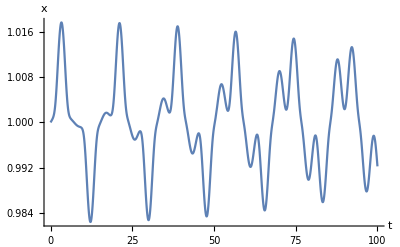
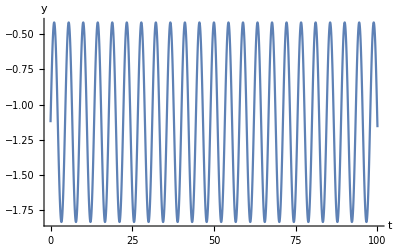
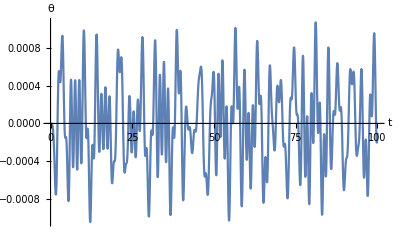

```mathematica
{Plot[{X1[t]}/.sol1,{t,0,T},AxesLabel->{"t","x"},PlotRange->All],
Plot[{X3[t]}/.sol1,{t,0,T},AxesLabel->{"t","y"},PlotRange->All],
Plot[{X5[t]}/.sol1,{t,0,T},AxesLabel->{"t","θ"},PlotRange->All]}
```

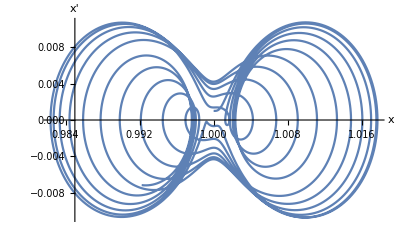
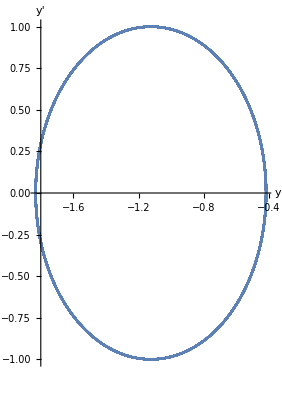
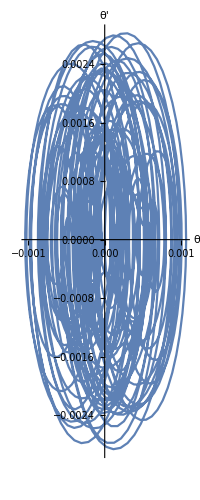

```mathematica
{ParametricPlot[{X1[t],X2[t]}/.sol1,{t,0,T},AxesLabel->{"x","x'"}],
ParametricPlot[{X3[t],X4[t]}/.sol1,{t,0,T},AxesLabel->{"y","y'"}],
ParametricPlot[{X5[t],X6[t]}/.sol1,{t,0,T},AxesLabel->{"θ","θ'"}]}
(*DrawAnimation*)
Animate[DrawSystem[Subscript[x, 1],Subscript[y, 1],Subscript[x, 2],Subscript[y, 2],Subscript[x, p],Subscript[y, p],θp,Subscript[w, p]][[1]]/.({(Subscript[x, p]->X1[t]/.sol1)[[1]],(Subscript[y, p]->X3[t]/.sol1)[[1]],(θp->X5[t]/.sol1)[[1]],Subscript[x, 1]->0,
Subscript[x, 2]->2 Subscript[w, p],Subscript[y, 1]->0,Subscript[y, 2]->0,NumericEquibInputs}//Flatten)(*/.EquibInputConditions*)/.NumericParametersTest,{t,0,T}]
```

```mathematica
(*dataset=Flatten[Table[{x,y,f[x,y]},{x,0,1,.1},{y,0,1.1}],1]*)
(*Export["mydataset.txt",dataset,"CSV"]*)
(*dataset=Flatten[Table[{t,X1[t]}/.sol1,{t,0,T}],1]
dataset=Flatten[Table[{t,X1[t]}/.sol1,{t,0,T,0.01}],1];*)
datasetAllState=Flatten[Table[
{t,X1[t],X2[t],X3[t],X4[t],X5[t],X6[t]}/.sol1,
{t,0,T,0.01}],1];
(*Export["./GitHub/quad_docs/mydataset.csv",dataset]*)
Export["./GitHub/quad_docs/myDatasetAllState.csv",datasetAllState]
```

./GitHub/quad_docs/myDatasetAllState.csv

```mathematica
ListPlot[dataset]
```

```mathematica
add both a driving force and damping
```

```mathematica
NumericTestParams
NumericParametersTest
EquibInputConditions
NumericEquibInputs
NumericStructuralDamping
```

{κ→1,ℒ→1,ω_s^2→100,α→11.8812,γ→0.04905}

{k_1→200,k_2→k_1,L0_1→2,L0_2→L0_1,m_p→2,h_p→0.1,w_p→1,g→9.81}

EquibInputConditions

{x_1[t]→0,y_1[t]→0,x_2[t]→2 w_p,y_2[t]→0}

{c_1→0.01,c_2→0.01,c_3→0.01}

```mathematica
Ω=2; (* Hz *)
Fmag=0.82 (*NonDim magnitude*)
Fmag=0
Fmag=0.005
NumericEquibInputs={Subscript[x, 1][t]->0,Subscript[y, 1][t]->0+Fmag Sin[Ω t],Subscript[x, 2][t]->2 Subscript[w, p],Subscript[y, 2][t]->Subscript[y, 1][t]}
(SymetricEOMtoInvestigate=EOM/.greekTermsSymetricCase//.NumericEquibInputs)/.dispNoTime//MatrixForm//TraditionalForm
EOMtoSolve=SymetricEOMtoInvestigate/.NumericTestParams/.NumericParametersTest/.NumericStructuralDamping;
```

0.82

0

0.005

{x_1[t]→0,y_1[t]→0.005 Sin[2 t],x_2[t]→2 w_p,y_2[t]→y_1[t]}

(x_p''
y_p''
θ_p'')==((sin(θ_p) h_p-cos(θ_p) w_p+2 w_p-x_p) (1-1/(√((sin(θ_p) h_p-cos(θ_p) w_p+2 w_p-x_p)^2+(0.005 sin(2 t)-cos(θ_p) h_p-sin(θ_p) w_p-y_p)^2)))+(sin(θ_p) h_p+cos(θ_p) w_p-x_p) (1-1/(√((sin(θ_p) h_p+cos(θ_p) w_p-x_p)^2+(0.005 sin(2 t)-cos(θ_p) h_p+sin(θ_p) w_p-y_p)^2)))-c_1 x_p'
-γ+(1-1/(√((sin(θ_p) h_p-cos(θ_p) w_p+2 w_p-x_p)^2+(0.005 sin(2 t)-cos(θ_p) h_p-sin(θ_p) w_p-y_p)^2))) (0.005 sin(2 t)-cos(θ_p) h_p-sin(θ_p) w_p-y_p)+(1-1/(√((sin(θ_p) h_p+cos(θ_p) w_p-x_p)^2+(0.005 sin(2 t)-cos(θ_p) h_p+sin(θ_p) w_p-y_p)^2))) (0.005 sin(2 t)-cos(θ_p) h_p+sin(θ_p) w_p-y_p)-c_2 y_p'
-α (w_p (sin(θ_p) x_p+cos(θ_p) (0.005 sin(2 t)-y_p))+h_p (sin(θ_p) (0.005 sin(2 t)-y_p)-cos(θ_p) x_p)) (1-1/(√((sin(θ_p) h_p+cos(θ_p) w_p-x_p)^2+(0.005 sin(2 t)-cos(θ_p) h_p+sin(θ_p) w_p-y_p)^2)))-α (1-1/(√((sin(θ_p) h_p-cos(θ_p) w_p+2 w_p-x_p)^2+(0.005 sin(2 t)-cos(θ_p) h_p-sin(θ_p) w_p-y_p)^2))) (h_p (cos(θ_p) (2 w_p-x_p)+sin(θ_p) (0.005 sin(2 t)-y_p))+w_p (sin(θ_p) (2 w_p-x_p)+cos(θ_p) (y_p-0.005 sin(2 t))))-c_3 θ_p')

```mathematica
NumericTestParams
NumericParametersTest
startValuesWithMove={X1[0]==Subscript[w, p],X2[0]==0.001,X3[0]==-1-Subscript[h, p]-γ/2,X4[0]==0.01,X5[0]==0,X6[0]==0.001}/.NumericTestParams/.NumericParametersTest
startValuesFromStatic={X1[0]==Subscript[w, p],X2[0]==0.00,X3[0]==-1-Subscript[h, p]-1/2 γ,X4[0]==0.0,X5[0]==0,X6[0]==0.00}/.NumericTestParams/.NumericParametersTest
```

{κ→1,ℒ→1,ω_s^2→100,α→11.8812,γ→0.04905}

{k_1→200,k_2→k_1,L0_1→2,L0_2→L0_1,m_p→2,h_p→0.1,w_p→1,g→9.81}

{X1[0]==1,X2[0]==0.001,X3[0]==-1.12453,X4[0]==0.01,X5[0]==0,X6[0]==0.001}

{X1[0]==1,X2[0]==0.,X3[0]==-1.12453,X4[0]==0.,X5[0]==0,X6[0]==0.}

```mathematica
startValuesFromStatic[[1]]
```

X1[0]==1

```mathematica
"Because of energy conservation one can clearly never get chaos from the motion of a single degree of freedom. We therefore add both a driving force and damping, in order to remove energy conservation"
```

```mathematica
Ω=2; (* Hz *);
calcSol[Fmag_,T_,startValues_ (*vec of 6*)]:={
NumericEquibInputs={Subscript[x, 1][t]->0,Subscript[y, 1][t]->0+Fmag Sin[Ω t],Subscript[x, 2][t]->2 Subscript[w, p],Subscript[y, 2][t]->Subscript[y, 1][t]};
SymetricEOMtoInvestigate=EOM/.greekTermsSymetricCase//.NumericEquibInputs;
EOMtoSolve=SymetricEOMtoInvestigate/.NumericTestParams/.NumericParametersTest/.NumericStructuralDamping;

numericEqs={X1'[t]==X2[t],
X2'[t]== (EOMtoSolve[[2,1]][[1]]),
X3'[t]==X4[t],
X4'[t]== (EOMtoSolve[[2,2]][[1]]),
X5'[t]==X6[t],
X6'[t]== (EOMtoSolve[[2,3]][[1]])}/.Subscript[x, p][t]->X1[t]/.Subscript[y, p][t]->X3[t]/.Subscript[θ, p][t]->X5[t]/.D[Subscript[x, p][t],t]->X2[t]/.D[Subscript[y, p][t],t]->X4[t]/.D[Subscript[θ, p][t],t]->X6[t];

(*startValues=startValuesFromStatic;*)
(*startValues=startValuesWithMove;*)
(*Print["startValues : "];
Print[startValues];*)
initValuesEquations={X1[0]==startValues[[1]],X2[0]==startValues[[2]],X3[0]==startValues[[3]],					X4[0]==startValues[[4]],X5[0]==startValues[[5]],X6[0]==startValues[[6]]};

sol1 = NDSolve[ {numericEqs, initValuesEquations}, {X1, X2,X3,X4,X5,X6}, {t, 0, T},MaxSteps -> Floor[1000*T] ];
sol1[[1]]  (* the value/data to return *)
}
```

according to ref of Duffing.nb:

```mathematica
"Rainbow: blue color is the beginning ,  as from 0 (blue) to 1 (red/orange)"
```

```mathematica
plotParametricPlots[midT_]:={
{ParametricPlot[{X1[t],X2[t]}/.sol1,{t,0,midT},AxesLabel->{"x","x'"},PlotRange->All,ColorFunction->"Rainbow"],
ParametricPlot[{X3[t],X4[t]}/.sol1,{t,0,midT},AxesLabel->{"y","y'"},PlotRange->All,ColorFunction->"Rainbow"],
ParametricPlot[{X5[t],X6[t]}/.sol1,{t,0,midT},AxesLabel->{"θ","θ'"},PlotRange->All,ColorFunction->"Rainbow"]},
{ParametricPlot[{X1[t],X2[t]}/.sol1,{t,midT,T},AxesLabel->{"x","x'"},PlotRange->All,ColorFunction->"Rainbow"],
ParametricPlot[{X3[t],X4[t]}/.sol1,{t,midT,T},AxesLabel->{"y","y'"},PlotRange->All,ColorFunction->"Rainbow"],
ParametricPlot[{X5[t],X6[t]}/.sol1,{t,midT,T},AxesLabel->{"θ","θ'"},PlotRange->All,ColorFunction->"Rainbow"]},
{Plot[{X1[t]}/.sol1,{t,0,T},AxesLabel->{"t","x"},PlotRange->All,ColorFunction->"Rainbow"],
Plot[{X2[t]}/.sol1,{t,0,T},AxesLabel->{"t","x'"},PlotRange->All(*,ColorFunction->"Rainbow"*)],
Plot[{X3[t]}/.sol1,{t,0,T},AxesLabel->{"t","y"},PlotRange->All,ColorFunction->"Rainbow"],
Plot[{X4[t]}/.sol1,{t,0,T},AxesLabel->{"t","y'"},PlotRange->All(*,ColorFunction->"Rainbow"*)],
Plot[{X5[t]}/.sol1,{t,0,T},AxesLabel->{"t","θ"},PlotRange->All,ColorFunction->"Rainbow"],
Plot[{X6[t]}/.sol1,{t,0,T},AxesLabel->{"t","θ'"},PlotRange->All(*,ColorFunction->"Rainbow"*)]}
}
```

```mathematica
{"expectedPeriod by Forcing period:" ,
 expectedPeriod=2π/(Ω /Subscript[ω, s])  /.(Subscript[ω, s]->√(Subscript[ω, s]^2)/.NumericTestParams)//N,"[sec]"}
```

{expectedPeriod by Forcing period:,31.4159,[sec]}

```mathematica
T=1*expectedPeriod
sectionTime=9/10 T;
```

31.4159

{{X1→InterpolatingFunction[{{0., 314.159}}, <>],X2→InterpolatingFunction[{{0., 314.159}}, <>],X3→InterpolatingFunction[{{0., 314.159}}, <>],X4→InterpolatingFunction[{{0., 314.159}}, <>],X5→InterpolatingFunction[{{0., 314.159}}, <>],X6→InterpolatingFunction[{{0., 314.159}}, <>]}}

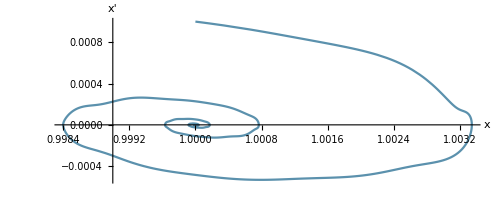
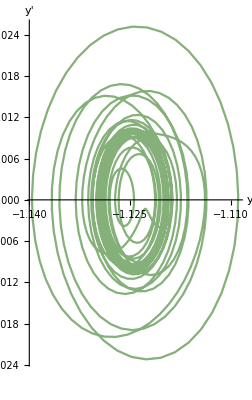
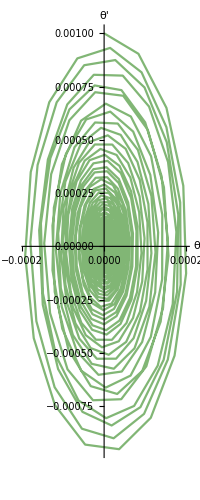
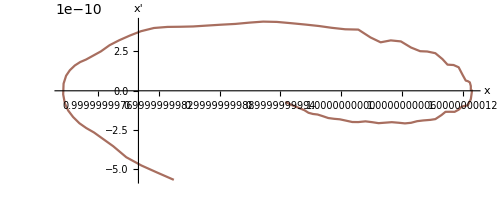
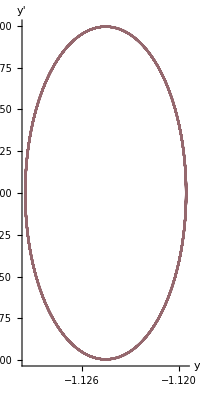
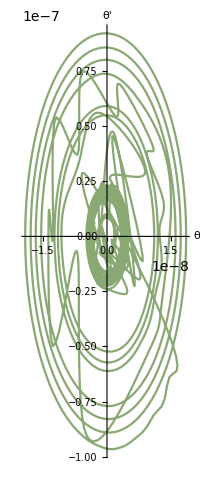
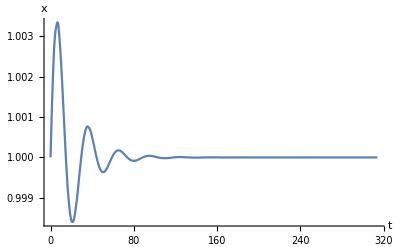
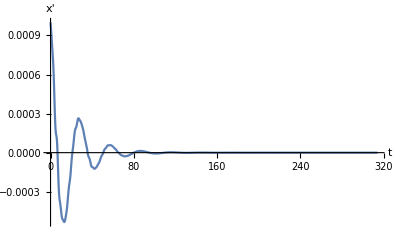

```mathematica
(*sol1 = NDSolve[ {numericEqs, startValues}, {X1, X2,X3,X4,X5,X6}, {t, 0, T} , MaxSteps -> 117500 ]*)
(*calcSol[0.005, T,startValuesWithMove[[All,2]]]
plotParametricPlots[sectionTime]*)
```

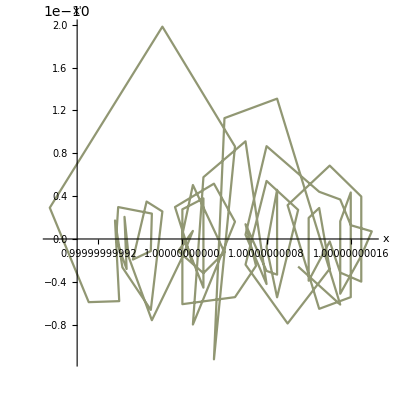
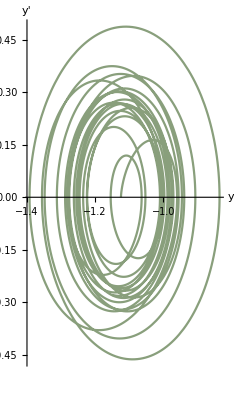
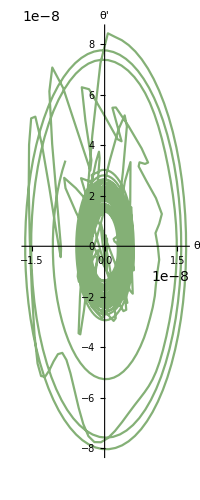
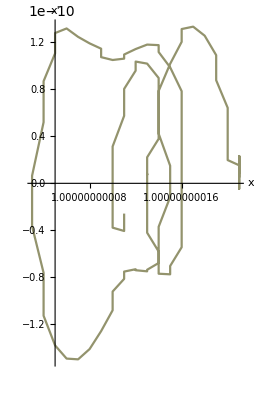
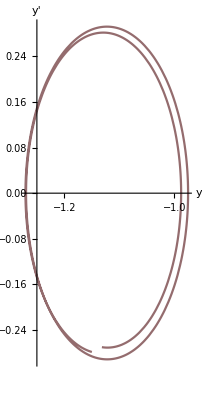
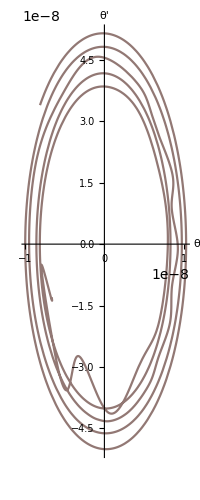
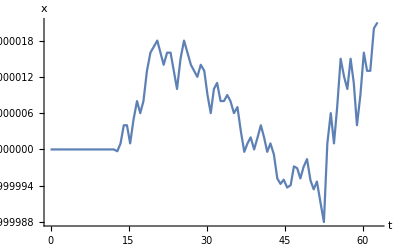
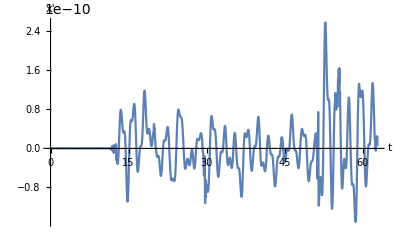

```mathematica
calcSol[0.14, T,startValuesFromStatic[[All,2]]];plotParametricPlots[sectionTime]
calcSol[0.16, T,startValuesFromStatic[[All,2]]];plotParametricPlots[sectionTime]
Manipulate[calcSol[f, T,startValuesFromStatic[[All,2]]];plotParametricPlots[sectionTime],{f,0.01,0.5}]
```

```mathematica
poincare[d_,ndrop_,nplot_,psize_]:=(
gg[prevStartValues_]:=({X1[T],X2[T],X3[T],X4[T],X5[T],X6[T]}/.calcSol[d, T,prevStartValues])[[1]];
(*Print[calcSol[d, T,startValuesFromStatic]];*)
(*Print[gg[startValuesFromStatic[[All,2]]]];*)
extList=Drop[NestList[gg,startValuesFromStatic[[All,2]],nplot+ndrop],ndrop];
(*Print[extList];*)
pX=ListPlot[Transpose[{extList[[All,1]],extList[[All,2]]}],PlotStyle->{PointSize[psize],Hue[0]},PlotRange->All,AxesLabel->{"x","x'"}];
pY=ListPlot[Transpose[{extList[[All,3]],extList[[All,4]]}],PlotStyle->{PointSize[psize],Hue[0]},PlotRange->All,AxesLabel->{"y","y'"}];
pθ=ListPlot[Transpose[{extList[[All,5]],extList[[All,6]]}],PlotStyle->{PointSize[psize],Hue[0]},PlotRange->All,AxesLabel->{"θ","θ'"}];
{pX,pY,pθ}
)
```

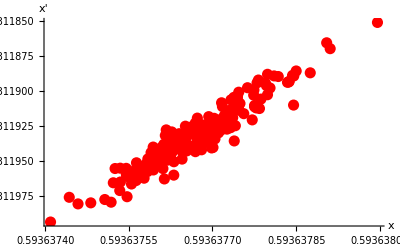
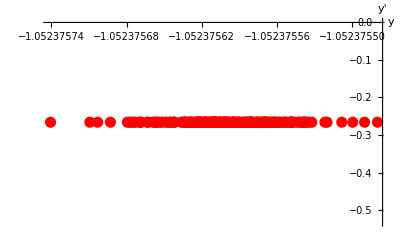
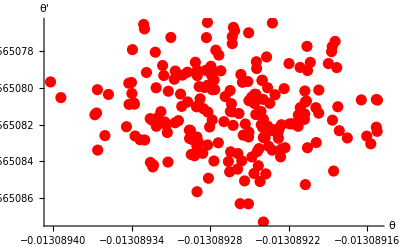

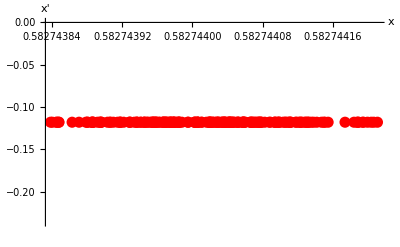
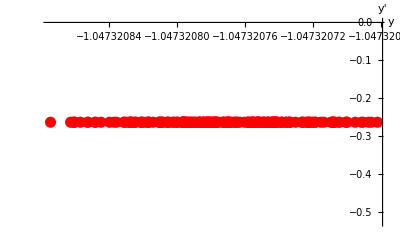
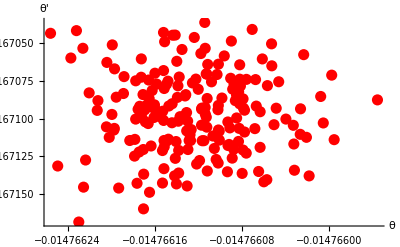

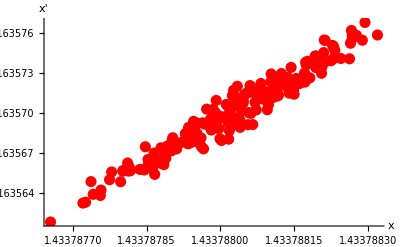
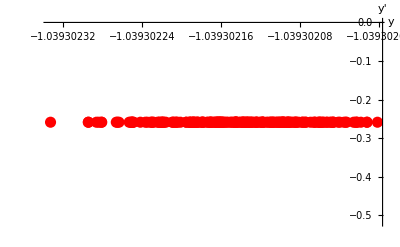

```mathematica
(*poincare[0.14,100,200,0.02]*)
poincare[0.161,100,200,0.02]
poincare[0.1612,100,200,0.02]
poincare[0.1614,100,200,0.02]
```

```mathematica
(*bifurcation[dmin_,dmax_,nd_,xmin_,xmax_,γ_,ω_,ndrop_,nplot_,psize_]:=(
xi = 1; vi = 0;g[{xold_,vold_}]:={x[T],v[T]}/.NDSolve[{v'[t]==x[t]-x[t]^3-γ v[t]+d Cos[ω t],x'[t]==v[t],x[0]==xold,v[0]==vold},{x,v},{t,0,T}]⟦1⟧;f[{x_,y_}]:=(xi = x; vi = y;{d,x});ListPlot[Flatten[Table[f/@Drop[NestList[g,{xi,vi},nplot+ndrop],ndrop],{d,dmin,dmax,(dmax-dmin)/nd}],1],PlotStyle->{PointSize[psize],Hue[0]},PlotRange->{{dmin,dmax},{xmin,xmax}},AxesLabel->{"d","x"}])*)
```

```mathematica
Clear[gg]
Clear[baseList]
Clear[fX]
Clear[tableListX]
```

```mathematica
bifurcation[dmin_,dmax_,nd_,ndrop_,nplot_,psize_]:=(gg[{prevStartValues_,d_}]:=({{X1[T],X2[T],X3[T],X4[T],X5[T],X6[T]},d}/.calcSol[d, T,prevStartValues])[[1]];
baseList[d_]:=Drop[NestList[gg,{startValuesFromStatic[[All,2]],d},nplot+ndrop],ndrop];
fX[{x_,d_}]:=(xElement = x[[1]]; {d,x[[1]]});
tableListX=Flatten[Table[fX/@(baseList[d]),{d,dmin,dmax,(dmax-dmin)/nd}],1];
(*tableListX=Flatten[Table[{(baseList[d])[[1,1]],{d,dmin,dmax,(dmax-dmin)/nd}],1];*)
(*Print[extList];*)
pX=ListPlot[tableListX,PlotStyle->{PointSize[psize],Hue[0]},PlotRange->All,AxesLabel->{"x","x'"}];
(*pY=ListPlot[Transpose[{extList[[All,3]],extList[[All,4]]}],PlotStyle->{PointSize[psize],Hue[0]},PlotRange->All,AxesLabel->{"y","y'"}];
pθ=ListPlot[Transpose[{extList[[All,5]],extList[[All,6]]}],PlotStyle->{PointSize[psize],Hue[0]},PlotRange->All,AxesLabel->{"θ","θ'"}];
*)(*{pX,pY,pθ}*)
pX
)
```

```mathematica
(*?gg
?baseList
?fX
?tableListX*)
```

Global`gg

Global`baseList

Global`fX

Global`tableListX

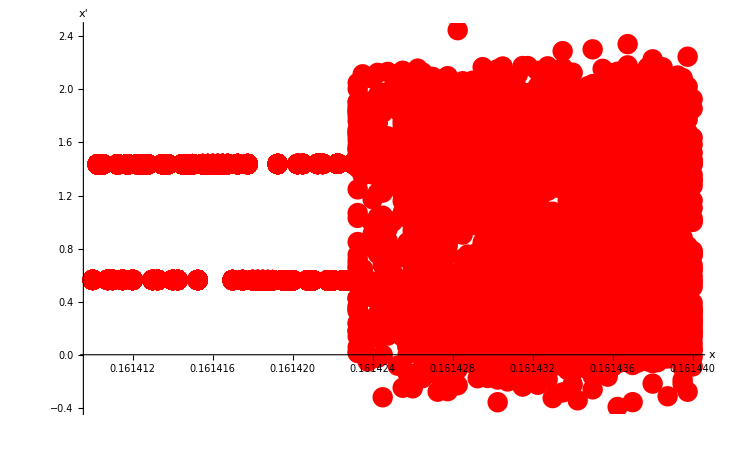

```mathematica
bifurcation[0.16141,0.16144,120,100,50,0.02]
```

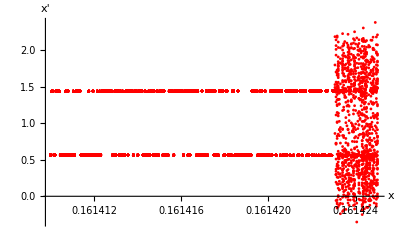

```mathematica
bifurcation[0.16141,0.161425,300,100,50,0.005]
```

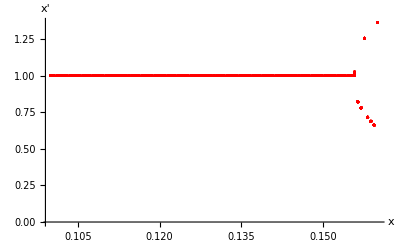

```mathematica
bifurcation[0.10,0.16,100,100,50,0.005]
```

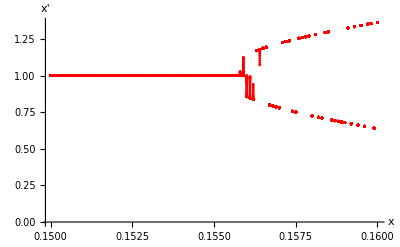

```mathematica
bifurcation[0.15,0.16,100,100,50,0.005]
```

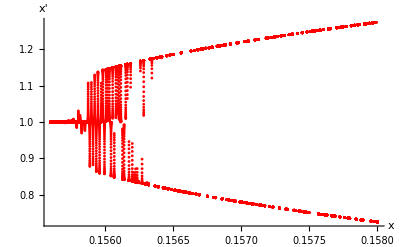

```mathematica
bifurcation[0.1556,0.158,200,100,50,0.005]
```

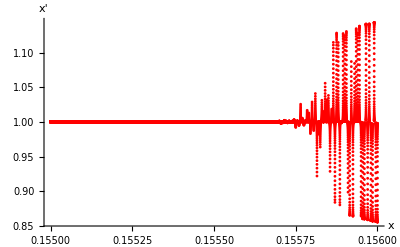

```mathematica
"the above might be numerical errors or not stable solution yet?  "
```

```mathematica
?gg
?baseList
?fX
?tableListX
```

Global`gg

gg[{prevStartValues_,d_}]:=({{X1[T],X2[T],X3[T],X4[T],X5[T],X6[T]},d}/.calcSol[d,T,prevStartValues])⟦1⟧

Global`baseList

baseList[d$_]:=Drop[NestList[gg,{startValuesFromStatic⟦All,2⟧,d$},50+100],100]

Global`fX

fX[{x_,d_}]:=(xElement=x⟦1⟧;{d,x⟦1⟧})

Global`tableListX

tableListX={{0.1556,1.},{0.1556,1.},{0.1556,1.},{0.1556,1.},{0.1556,1.},{0.1556,1.},{0.1556,1.},{0.1556,1.},{0.1556,1.},{0.1556,1.},{0.1556,1.},{0.1556,1.},{0.1556,1.},{0.1556,1.},{0.1556,1.},{0.1556,1.},{0.1556,1.},{0.1556,1.},{0.1556,1.},{0.1556,1.00001},{0.1556,1.00001},{0.1556,1.00001},{0.1556,1.00001},{0.1556,1.00001},{0.1556,1.00001},{0.1556,1.00001},{0.1556,1.00001},{0.1556,1.00001},{0.1556,1.00001},{0.1556,1.00001},{0.1556,1.00001},{0.1556,1.00001},{0.1556,1.00001},{0.1556,1.00001},{0.1556,1.00001},{0.1556,1.00002},{0.1556,1.00002},{0.1556,1.00002},{0.1556,1.00002},{0.1556,1.00002},{0.1556,1.00002},{0.1556,1.00002},{0.1556,1.00003},{0.1556,1.00003},{0.1556,1.00003},{0.1556,1.00003},{0.1556,1.00003},{0.1556,1.00004},{0.1556,1.00004},{0.1556,1.00004},{0.1556,1.00005},{0.155612,0.999998},{0.155612,0.999997},{0.155612,0.999997},{0.155612,0.999997},{0.155612,0.999997},{0.155612,0.999996},{0.155612,0.999996},{0.155612,0.999996},{0.155612,0.999996},{0.155612,0.999995},{0.155612,0.999995},{0.155612,0.999995},{0.155612,0.999994},{0.155612,0.999994},{0.155612,0.999993},{0.155612,0.999993},{0.155612,0.999992},{0.155612,0.999991},{0.155612,0.999991},{0.155612,0.99999},{0.155612,0.999989},{0.155612,0.999989},{0.155612,0.999988},{0.155612,0.999987},{0.155612,0.999986},{0.155612,0.999985},{0.155612,0.999983},{0.155612,0.999982},{0.155612,0.999981},{0.155612,0.999979},{0.155612,0.999978},{0.155612,0.999976},{0.155612,0.999974},{0.155612,0.999972},{0.155612,0.99997},{0.155612,0.999968},{0.155612,0.999965},{0.155612,0.999963},{0.155612,0.99996},{0.155612,0.999957},{0.155612,0.999954},{0.155612,0.99995},{0.155612,0.999946},{0.155612,0.999942},{0.155612,0.999938},{0.155612,0.999933},{0.155612,0.999928},{0.155612,0.999922},{0.155612,0.999916},{0.155612,0.99991},{0.155612,0.999903},{0.155624,1.},{0.155624,1.},{0.155624,1.},{0.155624,1.},{0.155624,1.},{0.155624,1.},{0.155624,1.},{0.155624,1.},{0.155624,1.},{0.155624,1.},{0.155624,1.},{0.155624,1.},{0.155624,1.},{0.155624,1.},{0.155624,1.},{0.155624,1.},{0.155624,1.},{0.155624,1.},{0.155624,1.},{0.155624,1.},{0.155624,1.},{0.155624,1.},{0.155624,1.},{0.155624,1.},{0.155624,1.},{0.155624,1.},{0.155624,1.},{0.155624,1.},{0.155624,1.},{0.155624,1.00001},{0.155624,1.00001},{0.155624,1.00001},{0.155624,1.00001},{0.155624,1.00001},{0.155624,1.00001},{0.155624,1.00001},{0.155624,1.00001},{0.155624,1.00001},{0.155624,1.00001},{0.155624,1.00001},{0.155624,1.00001},{0.155624,1.00001},{0.155624,1.00001},{0.155624,1.00002},{0.155624,1.00002},{0.155624,1.00002},{0.155624,1.00002},{0.155624,1.00002},{0.155624,1.00002},{0.155624,1.00002},{0.155624,1.00003},{0.155636,1.00001},{0.155636,1.00001},{0.155636,1.00001},{0.155636,1.00001},{0.155636,1.00001},{0.155636,1.00001},{0.155636,1.00001},{0.155636,1.00001},{0.155636,1.00001},{0.155636,1.00001},{0.155636,1.00001},{0.155636,1.00001},{0.155636,1.00001},{0.155636,1.00001},{0.155636,1.00002},{0.155636,1.00002},{0.155636,1.00002},{0.155636,1.00002},{0.155636,1.00002},{0.155636,1.00002},{0.155636,1.00002},{0.155636,1.00003},{0.155636,1.00003},{0.155636,1.00003},{0.155636,1.00003},{0.155636,1.00004},{0.155636,1.00004},{0.155636,1.00004},{0.155636,1.00005},{0.155636,1.00005},{0.155636,1.00005},{0.155636,1.00006},{0.155636,1.00006},{0.155636,1.00007},{0.155636,1.00007},{0.155636,1.00008},{0.155636,1.00009},{0.155636,1.00009},{0.155636,1.0001},{0.155636,1.00011},{0.155636,1.00012},{0.155636,1.00013},{0.155636,1.00014},{0.155636,1.00015},{0.155636,1.00016},{0.155636,1.00017},{0.155636,1.00019},{0.155636,1.0002},{0.155636,1.00022},{0.155636,1.00024},{0.155636,1.00026},{0.155648,0.999989},{0.155648,0.999988},{0.155648,0.999987},{0.155648,0.999986},{0.155648,0.999985},{0.155648,0.999983},{0.155648,0.999982},{0.155648,0.99998},{0.155648,0.999979},{0.155648,0.999977},{0.155648,0.999975},{0.155648,0.999973},{0.155648,0.99997},{0.155648,0.999968},{0.155648,0.999965},{0.155648,0.999962},{0.155648,0.999959},{0.155648,0.999956},{0.155648,0.999952},{0.155648,0.999948},{0.155648,0.999943},{0.155648,0.999939},{0.155648,0.999933},{0.155648,0.999928},{0.155648,0.999922},{0.155648,0.999915},{0.155648,0.999908},{0.155648,0.9999},{0.155648,0.999892},{0.155648,0.999883},{0.155648,0.999873},{0.155648,0.999862},{0.155648,0.999851},{0.155648,0.999838},{0.155648,0.999824},{0.155648,0.999809},{0.155648,0.999793},{0.155648,0.999776},{0.155648,0.999757},{0.155648,0.999737},{0.155648,0.999714},{0.155648,0.99969},{0.155648,0.999664},{0.155648,0.999636},{0.155648,0.999605},{0.155648,0.999572},{0.155648,0.999536},{0.155648,0.999497},{0.155648,0.999454},{0.155648,0.999408},{0.155648,0.999358},{0.15566,1.},{0.15566,1.00001},{0.15566,1.00001},{0.15566,1.00001},{0.15566,1.00001},{0.15566,1.00001},{0.15566,1.00001},{0.15566,1.00001},{0.15566,1.00001},{0.15566,1.00001},{0.15566,1.00001},{0.15566,1.00001},{0.15566,1.00001},{0.15566,1.00001},{0.15566,1.00002},{0.15566,1.00002},{0.15566,1.00002},{0.15566,1.00002},{0.15566,1.00002},{0.15566,1.00002},{0.15566,1.00003},{0.15566,1.00003},{0.15566,1.00003},{0.15566,1.00003},{0.15566,1.00004},{0.15566,1.00004},{0.15566,1.00004},{0.15566,1.00005},{0.15566,1.00005},{0.15566,1.00006},{0.15566,1.00006},{0.15566,1.00007},{0.15566,1.00007},{0.15566,1.00008},{0.15566,1.00008},{0.15566,1.00009},{0.15566,1.0001},{0.15566,1.00011},{0.15566,1.00012},{0.15566,1.00013},{0.15566,1.00014},{0.15566,1.00015},{0.15566,1.00016},{0.15566,1.00018},{0.15566,1.00019},{0.15566,1.00021},{0.15566,1.00023},{0.15566,1.00025},{0.15566,1.00027},{0.15566,1.00029},{0.15566,1.00032},{0.155672,1.},{0.155672,1.},{0.155672,1.},{0.155672,1.},{0.155672,1.},{0.155672,0.999999},{0.155672,0.999999},{0.155672,0.999999},{0.155672,0.999999},{0.155672,0.999999},{0.155672,0.999999},{0.155672,0.999999},{0.155672,0.999999},{0.155672,0.999999},{0.155672,0.999999},{0.155672,0.999999},{0.155672,0.999999},{0.155672,0.999999},{0.155672,0.999998},{0.155672,0.999998},{0.155672,0.999998},{0.155672,0.999998},{0.155672,0.999998},{0.155672,0.999998},{0.155672,0.999997},{0.155672,0.999997},{0.155672,0.999997},{0.155672,0.999997},{0.155672,0.999996},{0.155672,0.999996},{0.155672,0.999996},{0.155672,0.999995},{0.155672,0.999995},{0.155672,0.999994},{0.155672,0.999994},{0.155672,0.999993},{0.155672,0.999993},{0.155672,0.999992},{0.155672,0.999991},{0.155672,0.999991},{0.155672,0.99999},{0.155672,0.999989},{0.155672,0.999988},{0.155672,0.999987},{0.155672,0.999986},{0.155672,0.999984},{0.155672,0.999983},{0.155672,0.999981},{0.155672,0.99998},{0.155672,0.999978},{0.155672,0.999976},{0.155684,1.00001},{0.155684,1.00001},{0.155684,1.00001},{0.155684,1.00001},{0.155684,1.00002},{0.155684,1.00002},{0.155684,1.00002},{0.155684,1.00002},{0.155684,1.00002},{0.155684,1.00003},{0.155684,1.00003},{0.155684,1.00003},{0.155684,1.00003},{0.155684,1.00004},{0.155684,1.00004},{0.155684,1.00004},{0.155684,1.00005},{0.155684,1.00005},{0.155684,1.00006},{0.155684,1.00006},{0.155684,1.00007},{0.155684,1.00007},{0.155684,1.00008},{0.155684,1.00009},{0.155684,1.00009},{0.155684,1.0001},{0.155684,1.00011},{0.155684,1.00012},{0.155684,1.00013},{0.155684,1.00015},{0.155684,1.00016},{0.155684,1.00017},{0.155684,1.00019},{0.155684,1.00021},{0.155684,1.00023},{0.155684,1.00025},{0.155684,1.00027},{0.155684,1.0003},{0.155684,1.00032},{0.155684,1.00035},{0.155684,1.00039},{0.155684,1.00042},{0.155684,1.00046},{0.155684,1.0005},{0.155684,1.00055},{0.155684,1.0006},{0.155684,1.00065},{0.155684,1.00071},{0.155684,1.00078},{0.155684,1.00085},{0.155684,1.00093},{0.155696,1.},{0.155696,1.},{0.155696,0.999999},{0.155696,0.999999},{0.155696,0.999999},{0.155696,0.999999},{0.155696,0.999999},{0.155696,0.999999},{0.155696,0.999999},{0.155696,0.999999},{0.155696,0.999999},{0.155696,0.999999},{0.155696,0.999999},{0.155696,0.999999},{0.155696,0.999998},{0.155696,0.999998},{0.155696,0.999998},{0.155696,0.999998},{0.155696,0.999998},{0.155696,0.999998},{0.155696,0.999997},{0.155696,0.999997},{0.155696,0.999997},{0.155696,0.999997},{0.155696,0.999996},{0.155696,0.999996},{0.155696,0.999995},{0.155696,0.999995},{0.155696,0.999995},{0.155696,0.999994},{0.155696,0.999993},{0.155696,0.999993},{0.155696,0.999992},{0.155696,0.999991},{0.155696,0.999991},{0.155696,0.99999},{0.155696,0.999989},{0.155696,0.999988},{0.155696,0.999986},{0.155696,0.999985},{0.155696,0.999984},{0.155696,0.999982},{0.155696,0.999981},{0.155696,0.999979},{0.155696,0.999977},{0.155696,0.999974},{0.155696,0.999972},{0.155696,0.999969},{0.155696,0.999966},{0.155696,0.999963},{0.155696,0.99996},{0.155708,0.999981},{0.155708,0.999979},{0.155708,0.999977},{0.155708,0.999975},{0.155708,0.999973},{0.155708,0.99997},{0.155708,0.999967},{0.155708,0.999964},{0.155708,0.999961},{0.155708,0.999957},{0.155708,0.999953},{0.155708,0.999948},{0.155708,0.999943},{0.155708,0.999937},{0.155708,0.999931},{0.155708,0.999925},{0.155708,0.999917},{0.155708,0.999909},{0.155708,0.9999},{0.155708,0.999891},{0.155708,0.99988},{0.155708,0.999868},{0.155708,0.999856},{0.155708,0.999842},{0.155708,0.999826},{0.155708,0.999809},{0.155708,0.999791},{0.155708,0.99977},{0.155708,0.999748},{0.155708,0.999723},{0.155708,0.999697},{0.155708,0.999667},{0.155708,0.999635},{0.155708,0.999599},{0.155708,0.99956},{0.155708,0.999517},{0.155708,0.99947},{0.155708,0.999419},{0.155708,0.999362},{0.155708,0.9993},{0.155708,0.999232},{0.155708,0.999158},{0.155708,0.999076},{0.155708,0.998986},{0.155708,0.998887},{0.155708,0.998779},{0.155708,0.99866},{0.155708,0.99853},{0.155708,0.998386},{0.155708,0.998229},{0.155708,0.998057},{0.15572,1.00001},{0.15572,1.00001},{0.15572,1.00001},{0.15572,1.00002},{0.15572,1.00002},{0.15572,1.00002},{0.15572,1.00002},{0.15572,1.00002},{0.15572,1.00002},{0.15572,1.00003},{0.15572,1.00003},{0.15572,1.00003},{0.15572,1.00004},{0.15572,1.00004},{0.15572,1.00004},{0.15572,1.00005},{0.15572,1.00005},{0.15572,1.00006},{0.15572,1.00006},{0.15572,1.00007},{0.15572,1.00008},{0.15572,1.00009},{0.15572,1.00009},{0.15572,1.0001},{0.15572,1.00011},{0.15572,1.00012},{0.15572,1.00014},{0.15572,1.00015},{0.15572,1.00017},{0.15572,1.00018},{0.15572,1.0002},{0.15572,1.00022},{0.15572,1.00024},{0.15572,1.00027},{0.15572,1.00029},{0.15572,1.00032},{0.15572,1.00036},{0.15572,1.00039},{0.15572,1.00043},{0.15572,1.00047},{0.15572,1.00052},{0.15572,1.00057},{0.15572,1.00063},{0.15572,1.00069},{0.15572,1.00076},{0.15572,1.00084},{0.15572,1.00092},{0.15572,1.00101},{0.15572,1.00111},{0.15572,1.00123},{0.15572,1.00135},{0.155732,1.00003},{0.155732,1.00003},{0.155732,1.00004},{0.155732,1.00004},{0.155732,1.00004},{0.155732,1.00005},{0.155732,1.00005},{0.155732,1.00006},{0.155732,1.00006},{0.155732,1.00007},{0.155732,1.00008},{0.155732,1.00009},{0.155732,1.0001},{0.155732,1.00011},{0.155732,1.00012},{0.155732,1.00013},{0.155732,1.00014},{0.155732,1.00016},{0.155732,1.00017},{0.155732,1.00019},{0.155732,1.00021},{0.155732,1.00023},{0.155732,1.00025},{0.155732,1.00028},{0.155732,1.00031},{0.155732,1.00034},{0.155732,1.00038},{0.155732,1.00041},{0.155732,1.00046},{0.155732,1.0005},{0.155732,1.00056},{0.155732,1.00061},{0.155732,1.00068},{0.155732,1.00075},{0.155732,1.00082},{0.155732,1.00091},{0.155732,1.001},{0.155732,1.0011},{0.155732,1.00121},{0.155732,1.00134},{0.155732,1.00148},{0.155732,1.00163},{0.155732,1.00179},{0.155732,1.00198},{0.155732,1.00218},{0.155732,1.0024},{0.155732,1.00265},{0.155732,1.00292},{0.155732,1.00322},{0.155732,1.00355},{0.155732,1.00391},{0.155744,1.00002},{0.155744,1.00002},{0.155744,1.00002},{0.155744,1.00002},{0.155744,1.00002},{0.155744,1.00003},{0.155744,1.00003},{0.155744,1.00003},{0.155744,1.00004},{0.155744,1.00004},{0.155744,1.00004},{0.155744,1.00005},{0.155744,1.00005},{0.155744,1.00006},{0.155744,1.00006},{0.155744,1.00007},{0.155744,1.00008},{0.155744,1.00009},{0.155744,1.0001},{0.155744,1.00011},{0.155744,1.00012},{0.155744,1.00013},{0.155744,1.00014},{0.155744,1.00016},{0.155744,1.00018},{0.155744,1.00019},{0.155744,1.00021},{0.155744,1.00024},{0.155744,1.00026},{0.155744,1.00029},{0.155744,1.00032},{0.155744,1.00035},{0.155744,1.00039},{0.155744,1.00043},{0.155744,1.00048},{0.155744,1.00053},{0.155744,1.00058},{0.155744,1.00065},{0.155744,1.00071},{0.155744,1.00079},{0.155744,1.00087},{0.155744,1.00096},{0.155744,1.00106},{0.155744,1.00118},{0.155744,1.0013},{0.155744,1.00144},{0.155744,1.00159},{0.155744,1.00175},{0.155744,1.00194},{0.155744,1.00214},{0.155744,1.00236},{0.155756,1.00003},{0.155756,1.00003},{0.155756,1.00004},{0.155756,1.00004},{0.155756,1.00005},{0.155756,1.00005},{0.155756,1.00006},{0.155756,1.00006},{0.155756,1.00007},{0.155756,1.00008},{0.155756,1.00008},{0.155756,1.00009},{0.155756,1.0001},{0.155756,1.00011},{0.155756,1.00013},{0.155756,1.00014},{0.155756,1.00016},{0.155756,1.00017},{0.155756,1.00019},{0.155756,1.00021},{0.155756,1.00023},{0.155756,1.00026},{0.155756,1.00029},{0.155756,1.00032},{0.155756,1.00035},{0.155756,1.00039},{0.155756,1.00043},{0.155756,1.00048},{0.155756,1.00053},{0.155756,1.00059},{0.155756,1.00065},{0.155756,1.00072},{0.155756,1.0008},{0.155756,1.00089},{0.155756,1.00098},{0.155756,1.00109},{0.155756,1.0012},{0.155756,1.00133},{0.155756,1.00148},{0.155756,1.00164},{0.155756,1.00181},{0.155756,1.00201},{0.155756,1.00222},{0.155756,1.00246},{0.155756,1.00273},{0.155756,1.00302},{0.155756,1.00335},{0.155756,1.00371},{0.155756,1.0041},{0.155756,1.00455},{0.155756,1.00503},{0.155768,1.00004},{0.155768,1.00005},{0.155768,1.00005},{0.155768,1.00006},{0.155768,1.00007},{0.155768,1.00007},{0.155768,1.00008},{0.155768,1.00009},{0.155768,1.0001},{0.155768,1.00011},{0.155768,1.00012},{0.155768,1.00014},{0.155768,1.00015},{0.155768,1.00017},{0.155768,1.00019},{0.155768,1.00021},{0.155768,1.00023},{0.155768,1.00026},{0.155768,1.00029},{0.155768,1.00032},{0.155768,1.00036},{0.155768,1.0004},{0.155768,1.00044},{0.155768,1.00049},{0.155768,1.00054},{0.155768,1.0006},{0.155768,1.00067},{0.155768,1.00074},{0.155768,1.00082},{0.155768,1.00091},{0.155768,1.00101},{0.155768,1.00112},{0.155768,1.00125},{0.155768,1.00139},{0.155768,1.00154},{0.155768,1.00171},{0.155768,1.0019},{0.155768,1.00211},{0.155768,1.00234},{0.155768,1.0026},{0.155768,1.00288},{0.155768,1.0032},{0.155768,1.00356},{0.155768,1.00395},{0.155768,1.00438},{0.155768,1.00486},{0.155768,1.0054},{0.155768,1.00599},{0.155768,1.00665},{0.155768,1.00739},{0.155768,1.0082},{0.15578,1.00001},{0.15578,1.00001},{0.15578,1.00001},{0.15578,1.00001},{0.15578,1.00001},{0.15578,1.00002},{0.15578,1.00002},{0.15578,1.00002},{0.15578,1.00002},{0.15578,1.00002},{0.15578,1.00003},{0.15578,1.00003},{0.15578,1.00003},{0.15578,1.00004},{0.15578,1.00004},{0.15578,1.00005},{0.15578,1.00005},{0.15578,1.00006},{0.15578,1.00007},{0.15578,1.00007},{0.15578,1.00008},{0.15578,1.00009},{0.15578,1.0001},{0.15578,1.00011},{0.15578,1.00012},{0.15578,1.00014},{0.15578,1.00015},{0.15578,1.00017},{0.15578,1.00019},{0.15578,1.00021},{0.15578,1.00024},{0.15578,1.00026},{0.15578,1.00029},{0.15578,1.00032},{0.15578,1.00036},{0.15578,1.0004},{0.15578,1.00045},{0.15578,1.0005},{0.15578,1.00055},{0.15578,1.00062},{0.15578,1.00069},{0.15578,1.00076},{0.15578,1.00085},{0.15578,1.00095},{0.15578,1.00105},{0.15578,1.00117},{0.15578,1.0013},{0.15578,1.00145},{0.15578,1.00162},{0.15578,1.0018},{0.15578,1.002},{0.155792,0.999936},{0.155792,0.999929},{0.155792,0.999921},{0.155792,0.999911},{0.155792,0.999901},{0.155792,0.99989},{0.155792,0.999877},{0.155792,0.999863},{0.155792,0.999847},{0.155792,0.999829},{0.155792,0.999809},{0.155792,0.999787},{0.155792,0.999763},{0.155792,0.999735},{0.155792,0.999705},{0.155792,0.999671},{0.155792,0.999633},{0.155792,0.99959},{0.155792,0.999543},{0.155792,0.99949},{0.155792,0.999431},{0.155792,0.999366},{0.155792,0.999292},{0.155792,0.999211},{0.155792,0.999119},{0.155792,0.999018},{0.155792,0.998904},{0.155792,0.998777},{0.155792,0.998636},{0.155792,0.998479},{0.155792,0.998303},{0.155792,0.998107},{0.155792,0.997888},{0.155792,0.997644},{0.155792,0.997372},{0.155792,0.997069},{0.155792,0.99673},{0.155792,0.996353},{0.155792,0.995932},{0.155792,0.995462},{0.155792,0.994939},{0.155792,0.994355},{0.155792,0.993704},{0.155792,0.992979},{0.155792,0.992171},{0.155792,0.99127},{0.155792,0.990267},{0.155792,0.98915},{0.155792,0.987907},{0.155792,0.986524},{0.155792,0.984988},{0.155804,1.00012},{0.155804,1.00013},{0.155804,1.00015},{0.155804,1.00017},{0.155804,1.00019},{0.155804,1.00021},{0.155804,1.00023},{0.155804,1.00026},{0.155804,1.00029},{0.155804,1.00033},{0.155804,1.00036},{0.155804,1.00041},{0.155804,1.00046},{0.155804,1.00051},{0.155804,1.00057},{0.155804,1.00064},{0.155804,1.00071},{0.155804,1.0008},{0.155804,1.00089},{0.155804,1.001},{0.155804,1.00111},{0.155804,1.00125},{0.155804,1.00139},{0.155804,1.00156},{0.155804,1.00174},{0.155804,1.00195},{0.155804,1.00218},{0.155804,1.00244},{0.155804,1.00272},{0.155804,1.00305},{0.155804,1.00341},{0.155804,1.00381},{0.155804,1.00426},{0.155804,1.00476},{0.155804,1.00532},{0.155804,1.00595},{0.155804,1.00665},{0.155804,1.00743},{0.155804,1.00831},{0.155804,1.00928},{0.155804,1.01037},{0.155804,1.01159},{0.155804,1.01295},{0.155804,1.01446},{0.155804,1.01614},{0.155804,1.01801},{0.155804,1.02009},{0.155804,1.0224},{0.155804,1.02496},{0.155804,1.02778},{0.155804,1.03088},{0.155816,1.00006},{0.155816,1.00007},{0.155816,1.00008},{0.155816,1.00009},{0.155816,1.0001},{0.155816,1.00011},{0.155816,1.00013},{0.155816,1.00014},{0.155816,1.00016},{0.155816,1.00018},{0.155816,1.0002},{0.155816,1.00022},{0.155816,1.00025},{0.155816,1.00028},{0.155816,1.00031},{0.155816,1.00035},{0.155816,1.00039},{0.155816,1.00044},{0.155816,1.00049},{0.155816,1.00055},{0.155816,1.00062},{0.155816,1.00069},{0.155816,1.00078},{0.155816,1.00087},{0.155816,1.00098},{0.155816,1.0011},{0.155816,1.00123},{0.155816,1.00138},{0.155816,1.00154},{0.155816,1.00173},{0.155816,1.00194},{0.155816,1.00217},{0.155816,1.00244},{0.155816,1.00273},{0.155816,1.00306},{0.155816,1.00343},{0.155816,1.00384},{0.155816,1.00431},{0.155816,1.00483},{0.155816,1.00541},{0.155816,1.00606},{0.155816,1.00679},{0.155816,1.00761},{0.155816,1.00852},{0.155816,1.00955},{0.155816,1.01069},{0.155816,1.01197},{0.155816,1.0134},{0.155816,1.015},{0.155816,1.01679},{0.155816,1.01878},{0.155828,0.999908},{0.155828,0.999897},{0.155828,0.999884},{0.155828,0.99987},{0.155828,0.999854},{0.155828,0.999836},{0.155828,0.999816},{0.155828,0.999793},{0.155828,0.999767},{0.155828,0.999739},{0.155828,0.999706},{0.155828,0.99967},{0.155828,0.999629},{0.155828,0.999584},{0.155828,0.999532},{0.155828,0.999475},{0.155828,0.99941},{0.155828,0.999337},{0.155828,0.999255},{0.155828,0.999163},{0.155828,0.99906},{0.155828,0.998944},{0.155828,0.998814},{0.155828,0.998667},{0.155828,0.998503},{0.155828,0.998318},{0.155828,0.998111},{0.155828,0.997878},{0.155828,0.997616},{0.155828,0.997322},{0.155828,0.996992},{0.155828,0.99662},{0.155828,0.996204},{0.155828,0.995736},{0.155828,0.99521},{0.155828,0.99462},{0.155828,0.993958},{0.155828,0.993214},{0.155828,0.992379},{0.155828,0.991442},{0.155828,0.990391},{0.155828,0.989213},{0.155828,0.987892},{0.155828,0.986413},{0.155828,0.984757},{0.155828,0.982906},{0.155828,0.980838},{0.155828,0.978532},{0.155828,0.975965},{0.155828,0.973114},{0.155828,0.969958},{0.15584,0.99998},{0.15584,0.999977},{0.15584,0.999974},{0.15584,0.999971},{0.15584,0.999967},{0.15584,0.999963},{0.15584,0.999958},{0.15584,0.999953},{0.15584,0.999947},{0.15584,0.999941},{0.15584,0.999933},{0.15584,0.999925},{0.15584,0.999915},{0.15584,0.999905},{0.15584,0.999893},{0.15584,0.999879},{0.15584,0.999864},{0.15584,0.999847},{0.15584,0.999827},{0.15584,0.999806},{0.15584,0.999781},{0.15584,0.999754},{0.15584,0.999723},{0.15584,0.999688},{0.15584,0.999648},{0.15584,0.999604},{0.15584,0.999554},{0.15584,0.999498},{0.15584,0.999434},{0.15584,0.999363},{0.15584,0.999283},{0.15584,0.999193},{0.15584,0.999091},{0.15584,0.998976},{0.15584,0.998847},{0.15584,0.998702},{0.15584,0.998538},{0.15584,0.998354},{0.15584,0.998147},{0.15584,0.997913},{0.15584,0.99765},{0.15584,0.997354},{0.15584,0.997021},{0.15584,0.996645},{0.15584,0.996223},{0.15584,0.995748},{0.15584,0.995212},{0.15584,0.99461},{0.15584,0.993932},{0.15584,0.993169},{0.15584,0.99231},{0.155852,0.999944},{0.155852,0.999937},{0.155852,0.999929},{0.155852,0.99992},{0.155852,0.99991},{0.155852,0.999898},{0.155852,0.999885},{0.155852,0.99987},{0.155852,0.999854},{0.155852,0.999835},{0.155852,0.999814},{0.155852,0.99979},{0.155852,0.999763},{0.155852,0.999732},{0.155852,0.999698},{0.155852,0.999659},{0.155852,0.999615},{0.155852,0.999565},{0.155852,0.999509},{0.155852,0.999446},{0.155852,0.999375},{0.155852,0.999295},{0.155852,0.999204},{0.155852,0.999101},{0.155852,0.998986},{0.155852,0.998855},{0.155852,0.998708},{0.155852,0.998542},{0.155852,0.998354},{0.155852,0.998142},{0.155852,0.997903},{0.155852,0.997634},{0.155852,0.997329},{0.155852,0.996986},{0.155852,0.996598},{0.155852,0.996161},{0.155852,0.995668},{0.155852,0.995111},{0.155852,0.994483},{0.155852,0.993775},{0.155852,0.992976},{0.155852,0.992075},{0.155852,0.991059},{0.155852,0.989915},{0.155852,0.988626},{0.155852,0.987175},{0.155852,0.985543},{0.155852,0.983709},{0.155852,0.981649},{0.155852,0.97934},{0.155852,0.976755},{0.155864,1.},{0.155864,1.},{0.155864,1.},{0.155864,1.},{0.155864,1.},{0.155864,1.},{0.155864,1.},{0.155864,1.},{0.155864,1.},{0.155864,1.},{0.155864,1.},{0.155864,1.},{0.155864,1.},{0.155864,1.},{0.155864,1.},{0.155864,1.},{0.155864,1.},{0.155864,1.},{0.155864,1.00001},{0.155864,1.00001},{0.155864,1.00001},{0.155864,1.00001},{0.155864,1.00001},{0.155864,1.00001},{0.155864,1.00001},{0.155864,1.00001},{0.155864,1.00001},{0.155864,1.00002},{0.155864,1.00002},{0.155864,1.00002},{0.155864,1.00002},{0.155864,1.00003},{0.155864,1.00003},{0.155864,1.00003},{0.155864,1.00004},{0.155864,1.00004},{0.155864,1.00005},{0.155864,1.00005},{0.155864,1.00006},{0.155864,1.00007},{0.155864,1.00008},{0.155864,1.00009},{0.155864,1.0001},{0.155864,1.00011},{0.155864,1.00013},{0.155864,1.00014},{0.155864,1.00016},{0.155864,1.00018},{0.155864,1.00021},{0.155864,1.00023},{0.155864,1.00027},{0.155876,1.00033},{0.155876,1.00037},{0.155876,1.00042},{0.155876,1.00048},{0.155876,1.00054},{0.155876,1.00061},{0.155876,1.0007},{0.155876,1.00079},{0.155876,1.00089},{0.155876,1.00101},{0.155876,1.00115},{0.155876,1.0013},{0.155876,1.00148},{0.155876,1.00168},{0.155876,1.0019},{0.155876,1.00216},{0.155876,1.00244},{0.155876,1.00277},{0.155876,1.00314},{0.155876,1.00356},{0.155876,1.00404},{0.155876,1.00458},{0.155876,1.00519},{0.155876,1.00589},{0.155876,1.00668},{0.155876,1.00757},{0.155876,1.00858},{0.155876,1.00972},{0.155876,1.01101},{0.155876,1.01248},{0.155876,1.01413},{0.155876,1.016},{0.155876,1.01811},{0.155876,1.02049},{0.155876,1.02316},{0.155876,1.02615},{0.155876,1.02951},{0.155876,1.03324},{0.155876,1.03739},{0.155876,1.04196},{0.155876,1.04697},{0.155876,1.0524},{0.155876,1.05823},{0.155876,1.06441},{0.155876,1.07085},{0.155876,1.07744},{0.155876,1.08405},{0.155876,1.09053},{0.155876,1.09671},{0.155876,1.10247},{0.155876,1.10768},{0.155888,0.999547},{0.155888,0.999485},{0.155888,0.999414},{0.155888,0.999334},{0.155888,0.999243},{0.155888,0.99914},{0.155888,0.999023},{0.155888,0.998889},{0.155888,0.998738},{0.155888,0.998565},{0.155888,0.998369},{0.155888,0.998147},{0.155888,0.997894},{0.155888,0.997606},{0.155888,0.997279},{0.155888,0.996908},{0.155888,0.996486},{0.155888,0.996006},{0.155888,0.995461},{0.155888,0.994842},{0.155888,0.994139},{0.155888,0.99334},{0.155888,0.992433},{0.155888,0.991403},{0.155888,0.990234},{0.155888,0.988909},{0.155888,0.987405},{0.155888,0.985702},{0.155888,0.983775},{0.155888,0.981595},{0.155888,0.979134},{0.155888,0.976361},{0.155888,0.973244},{0.155888,0.96975},{0.155888,0.965851},{0.155888,0.96152},{0.155888,0.95674},{0.155888,0.951505},{0.155888,0.945827},{0.155888,0.939742},{0.155888,0.933313},{0.155888,0.926635},{0.155888,0.919832},{0.155888,0.913057},{0.155888,0.906475},{0.155888,0.900247},{0.155888,0.894517},{0.155888,0.889389},{0.155888,0.884922},{0.155888,0.881128},{0.155888,0.877979},{0.1559,1.00026},{0.1559,1.0003},{0.1559,1.00034},{0.1559,1.00038},{0.1559,1.00044},{0.1559,1.0005},{0.1559,1.00057},{0.1559,1.00065},{0.1559,1.00074},{0.1559,1.00084},{0.1559,1.00095},{0.1559,1.00109},{0.1559,1.00124},{0.1559,1.00141},{0.1559,1.00161},{0.1559,1.00183},{0.1559,1.00209},{0.1559,1.00238},{0.1559,1.00271},{0.1559,1.00308},{0.1559,1.00351},{0.1559,1.004},{0.1559,1.00456},{0.1559,1.00519},{0.1559,1.00591},{0.1559,1.00674},{0.1559,1.00767},{0.1559,1.00874},{0.1559,1.00995},{0.1559,1.01132},{0.1559,1.01289},{0.1559,1.01466},{0.1559,1.01667},{0.1559,1.01896},{0.1559,1.02154},{0.1559,1.02445},{0.1559,1.02773},{0.1559,1.03141},{0.1559,1.03553},{0.1559,1.0401},{0.1559,1.04514},{0.1559,1.05066},{0.1559,1.05663},{0.1559,1.06301},{0.1559,1.06972},{0.1559,1.07666},{0.1559,1.08366},{0.1559,1.09056},{0.1559,1.0972},{0.1559,1.10339},{0.1559,1.10901},{0.155912,0.999712},{0.155912,0.999671},{0.155912,0.999625},{0.155912,0.999572},{0.155912,0.999511},{0.155912,0.999441},{0.155912,0.999362},{0.155912,0.999272},{0.155912,0.999168},{0.155912,0.99905},{0.155912,0.998916},{0.155912,0.998762},{0.155912,0.998586},{0.155912,0.998386},{0.155912,0.998157},{0.155912,0.997895},{0.155912,0.997597},{0.155912,0.997256},{0.155912,0.996867},{0.155912,0.996423},{0.155912,0.995916},{0.155912,0.995337},{0.155912,0.994676},{0.155912,0.993922},{0.155912,0.993062},{0.155912,0.992081},{0.155912,0.990961},{0.155912,0.989685},{0.155912,0.988232},{0.155912,0.986576},{0.155912,0.984692},{0.155912,0.982552},{0.155912,0.980122},{0.155912,0.977369},{0.155912,0.974256},{0.155912,0.970748},{0.155912,0.96681},{0.155912,0.962409},{0.155912,0.957522},{0.155912,0.952138},{0.155912,0.946262},{0.155912,0.939928},{0.155912,0.933199},{0.155912,0.926176},{0.155912,0.918997},{0.155912,0.91183},{0.155912,0.904862},{0.155912,0.898277},{0.155912,0.892239},{0.155912,0.886866},{0.155912,0.88222},{0.155924,1.00041},{0.155924,1.00047},{0.155924,1.00054},{0.155924,1.00062},{0.155924,1.00071},{0.155924,1.00081},{0.155924,1.00093},{0.155924,1.00106},{0.155924,1.00122},{0.155924,1.00139},{0.155924,1.00159},{0.155924,1.00182},{0.155924,1.00209},{0.155924,1.00239},{0.155924,1.00273},{0.155924,1.00313},{0.155924,1.00358},{0.155924,1.00409},{0.155924,1.00468},{0.155924,1.00536},{0.155924,1.00613},{0.155924,1.00702},{0.155924,1.00803},{0.155924,1.00919},{0.155924,1.01051},{0.155924,1.01202},{0.155924,1.01374},{0.155924,1.0157},{0.155924,1.01794},{0.155924,1.02048},{0.155924,1.02336},{0.155924,1.02663},{0.155924,1.03032},{0.155924,1.03447},{0.155924,1.0391},{0.155924,1.04425},{0.155924,1.04992},{0.155924,1.0561},{0.155924,1.06273},{0.155924,1.06976},{0.155924,1.07704},{0.155924,1.08443},{0.155924,1.09174},{0.155924,1.09876},{0.155924,1.10531},{0.155924,1.11123},{0.155924,1.11642},{0.155924,1.12084},{0.155924,1.12449},{0.155924,1.12745},{0.155924,1.12979},{0.155936,0.999329},{0.155936,0.999231},{0.155936,0.999117},{0.155936,0.998988},{0.155936,0.998839},{0.155936,0.998668},{0.155936,0.998472},{0.155936,0.998247},{0.155936,0.997989},{0.155936,0.997693},{0.155936,0.997353},{0.155936,0.996964},{0.155936,0.996518},{0.155936,0.996006},{0.155936,0.995418},{0.155936,0.994745},{0.155936,0.993973},{0.155936,0.993088},{0.155936,0.992074},{0.155936,0.990912},{0.155936,0.989581},{0.155936,0.988057},{0.155936,0.986314},{0.155936,0.984322},{0.155936,0.982048},{0.155936,0.979456},{0.155936,0.976506},{0.155936,0.973159},{0.155936,0.969373},{0.155936,0.965109},{0.155936,0.960334},{0.155936,0.955022},{0.155936,0.949166},{0.155936,0.942785},{0.155936,0.935926},{0.155936,0.928678},{0.155936,0.921172},{0.155936,0.913584},{0.155936,0.906118},{0.155936,0.898985},{0.155936,0.892382},{0.155936,0.886465},{0.155936,0.88133},{0.155936,0.877004},{0.155936,0.87346},{0.155936,0.870623},{0.155936,0.868399},{0.155936,0.866683},{0.155936,0.865377},{0.155936,0.864394},{0.155936,0.863659},{0.155948,1.00071},{0.155948,1.00082},{0.155948,1.00094},{0.155948,1.00108},{0.155948,1.00124},{0.155948,1.00143},{0.155948,1.00164},{0.155948,1.00189},{0.155948,1.00217},{0.155948,1.0025},{0.155948,1.00287},{0.155948,1.0033},{0.155948,1.0038},{0.155948,1.00437},{0.155948,1.00502},{0.155948,1.00577},{0.155948,1.00663},{0.155948,1.00763},{0.155948,1.00876},{0.155948,1.01007},{0.155948,1.01157},{0.155948,1.01329},{0.155948,1.01526},{0.155948,1.01752},{0.155948,1.0201},{0.155948,1.02304},{0.155948,1.02639},{0.155948,1.03018},{0.155948,1.03447},{0.155948,1.03929},{0.155948,1.04466},{0.155948,1.0506},{0.155948,1.0571},{0.155948,1.0641},{0.155948,1.07151},{0.155948,1.0792},{0.155948,1.08699},{0.155948,1.09466},{0.155948,1.10198},{0.155948,1.10874},{0.155948,1.11479},{0.155948,1.12002},{0.155948,1.1244},{0.155948,1.12797},{0.155948,1.1308},{0.155948,1.13302},{0.155948,1.13471},{0.155948,1.13599},{0.155948,1.13695},{0.155948,1.13766},{0.155948,1.13818},{0.15596,0.998763},{0.15596,0.998575},{0.15596,0.998357},{0.15596,0.998107},{0.15596,0.997818},{0.15596,0.997486},{0.15596,0.997102},{0.15596,0.996661},{0.15596,0.996152},{0.15596,0.995566},{0.15596,0.994891},{0.15596,0.994113},{0.15596,0.993217},{0.15596,0.992186},{0.15596,0.990999},{0.15596,0.989632},{0.15596,0.988061},{0.15596,0.986255},{0.15596,0.984182},{0.15596,0.981805},{0.15596,0.979083},{0.15596,0.975972},{0.15596,0.972427},{0.15596,0.968402},{0.15596,0.963853},{0.15596,0.958743},{0.15596,0.953047},{0.15596,0.94676},{0.15596,0.939909},{0.15596,0.93256},{0.15596,0.924827},{0.15596,0.916873},{0.15596,0.908909},{0.15596,0.90117},{0.15596,0.893894},{0.15596,0.887284},{0.15596,0.881484},{0.15596,0.876562},{0.15596,0.872512},{0.15596,0.869268},{0.15596,0.86673},{0.15596,0.864783},{0.15596,0.863311},{0.15596,0.862213},{0.15596,0.861401},{0.15596,0.860804},{0.15596,0.860368},{0.15596,0.86005},{0.15596,0.859819},{0.15596,0.859652},{0.15596,0.859531},{0.155972,1.00011},{0.155972,1.00013},{0.155972,1.00015},{0.155972,1.00018},{0.155972,1.0002},{0.155972,1.00024},{0.155972,1.00027},{0.155972,1.00032},{0.155972,1.00036},{0.155972,1.00042},{0.155972,1.00049},{0.155972,1.00056},{0.155972,1.00065},{0.155972,1.00075},{0.155972,1.00086},{0.155972,1.001},{0.155972,1.00115},{0.155972,1.00133},{0.155972,1.00154},{0.155972,1.00178},{0.155972,1.00205},{0.155972,1.00237},{0.155972,1.00274},{0.155972,1.00316},{0.155972,1.00365},{0.155972,1.00422},{0.155972,1.00488},{0.155972,1.00563},{0.155972,1.0065},{0.155972,1.00751},{0.155972,1.00867},{0.155972,1.01001},{0.155972,1.01155},{0.155972,1.01333},{0.155972,1.01538},{0.155972,1.01773},{0.155972,1.02043},{0.155972,1.02353},{0.155972,1.02707},{0.155972,1.0311},{0.155972,1.03567},{0.155972,1.04081},{0.155972,1.04657},{0.155972,1.05294},{0.155972,1.0599},{0.155972,1.06739},{0.155972,1.0753},{0.155972,1.08345},{0.155972,1.09162},{0.155972,1.09956},{0.155972,1.10702},{0.155984,1.00244},{0.155984,1.00282},{0.155984,1.00327},{0.155984,1.00378},{0.155984,1.00438},{0.155984,1.00507},{0.155984,1.00586},{0.155984,1.00679},{0.155984,1.00786},{0.155984,1.00909},{0.155984,1.01052},{0.155984,1.01217},{0.155984,1.01407},{0.155984,1.01627},{0.155984,1.0188},{0.155984,1.02171},{0.155984,1.02504},{0.155984,1.02886},{0.155984,1.03321},{0.155984,1.03814},{0.155984,1.04368},{0.155984,1.04986},{0.155984,1.05668},{0.155984,1.06409},{0.155984,1.072},{0.155984,1.08026},{0.155984,1.08865},{0.155984,1.09693},{0.155984,1.10482},{0.155984,1.11208},{0.155984,1.11851},{0.155984,1.12401},{0.155984,1.12854},{0.155984,1.13217},{0.155984,1.13501},{0.155984,1.13717},{0.155984,1.13879},{0.155984,1.13999},{0.155984,1.14087},{0.155984,1.1415},{0.155984,1.14196},{0.155984,1.14229},{0.155984,1.14253},{0.155984,1.1427},{0.155984,1.14282},{0.155984,1.14291},{0.155984,1.14297},{0.155984,1.14302},{0.155984,1.14305},{0.155984,1.14307},{0.155984,1.14308},{0.155996,0.999582},{0.155996,0.999515},{0.155996,0.999438},{0.155996,0.999347},{0.155996,0.999243},{0.155996,0.999121},{0.155996,0.99898},{0.155996,0.998816},{0.155996,0.998627},{0.155996,0.998406},{0.155996,0.998151},{0.155996,0.997854},{0.155996,0.99751},{0.155996,0.99711},{0.155996,0.996647},{0.155996,0.996109},{0.155996,0.995486},{0.155996,0.994762},{0.155996,0.993923},{0.155996,0.99295},{0.155996,0.991822},{0.155996,0.990515},{0.155996,0.989},{0.155996,0.987247},{0.155996,0.985219},{0.155996,0.982876},{0.155996,0.980172},{0.155996,0.977057},{0.155996,0.97348},{0.155996,0.969386},{0.155996,0.96472},{0.155996,0.959434},{0.155996,0.953495},{0.155996,0.946888},{0.155996,0.939634},{0.155996,0.9318},{0.155996,0.923511},{0.155996,0.914956},{0.155996,0.906381},{0.155996,0.898067},{0.155996,0.890294},{0.155996,0.883298},{0.155996,0.877239},{0.155996,0.872179},{0.155996,0.868092},{0.155996,0.864886},{0.155996,0.862431},{0.155996,0.86059},{0.155996,0.859229},{0.155996,0.858235},{0.155996,0.857516},{0.156008,1.0017},{0.156008,1.00198},{0.156008,1.0023},{0.156008,1.00268},{0.156008,1.00311},{0.156008,1.00362},{0.156008,1.00421},{0.156008,1.0049},{0.156008,1.00569},{0.156008,1.00662},{0.156008,1.0077},{0.156008,1.00895},{0.156008,1.01041},{0.156008,1.01209},{0.156008,1.01405},{0.156008,1.01632},{0.156008,1.01894},{0.156008,1.02197},{0.156008,1.02546},{0.156008,1.02948},{0.156008,1.03406},{0.156008,1.03928},{0.156008,1.04517},{0.156008,1.05175},{0.156008,1.05901},{0.156008,1.0669},{0.156008,1.0753},{0.156008,1.08403},{0.156008,1.09282},{0.156008,1.10141},{0.156008,1.10947},{0.156008,1.11676},{0.156008,1.1231},{0.156008,1.12839},{0.156008,1.13267},{0.156008,1.13601},{0.156008,1.13857},{0.156008,1.14048},{0.156008,1.14188},{0.156008,1.1429},{0.156008,1.14363},{0.156008,1.14416},{0.156008,1.14453},{0.156008,1.14479},{0.156008,1.14498},{0.156008,1.14511},{0.156008,1.14521},{0.156008,1.14527},{0.156008,1.14532},{0.156008,1.14535},{0.156008,1.14537},{0.15602,1.00399},{0.15602,1.00465},{0.15602,1.00542},{0.15602,1.00632},{0.15602,1.00736},{0.15602,1.00858},{0.15602,1.01},{0.15602,1.01165},{0.15602,1.01357},{0.15602,1.01579},{0.15602,1.01838},{0.15602,1.02137},{0.15602,1.02483},{0.15602,1.02881},{0.15602,1.03338},{0.15602,1.03859},{0.15602,1.0445},{0.15602,1.05112},{0.15602,1.05846},{0.15602,1.06646},{0.15602,1.075},{0.15602,1.08391},{0.15602,1.09292},{0.15602,1.10173},{0.15602,1.11002},{0.15602,1.11752},{0.15602,1.12402},{0.15602,1.12945},{0.15602,1.13381},{0.15602,1.13721},{0.15602,1.13979},{0.15602,1.14171},{0.15602,1.14311},{0.15602,1.14412},{0.15602,1.14484},{0.15602,1.14535},{0.15602,1.14571},{0.15602,1.14597},{0.15602,1.14615},{0.15602,1.14627},{0.15602,1.14636},{0.15602,1.14642},{0.15602,1.14646},{0.15602,1.14649},{0.15602,1.14652},{0.15602,1.14653},{0.15602,1.14654},{0.15602,1.14655},{0.15602,1.14655},{0.15602,1.14656},{0.15602,1.14656},{0.156032,1.00439},{0.156032,1.00513},{0.156032,1.00599},{0.156032,1.007},{0.156032,1.00818},{0.156032,1.00955},{0.156032,1.01115},{0.156032,1.01302},{0.156032,1.01519},{0.156032,1.01772},{0.156032,1.02065},{0.156032,1.02406},{0.156032,1.02799},{0.156032,1.03251},{0.156032,1.0377},{0.156032,1.04358},{0.156032,1.05022},{0.156032,1.05759},{0.156032,1.06567},{0.156032,1.07434},{0.156032,1.08342},{0.156032,1.09265},{0.156032,1.1017},{0.156032,1.11024},{0.156032,1.11798},{0.156032,1.1247},{0.156032,1.1303},{0.156032,1.13479},{0.156032,1.13828},{0.156032,1.14091},{0.156032,1.14286},{0.156032,1.14428},{0.156032,1.14529},{0.156032,1.14601},{0.156032,1.14652},{0.156032,1.14688},{0.156032,1.14712},{0.156032,1.1473},{0.156032,1.14742},{0.156032,1.1475},{0.156032,1.14756},{0.156032,1.1476},{0.156032,1.14763},{0.156032,1.14765},{0.156032,1.14766},{0.156032,1.14767},{0.156032,1.14768},{0.156032,1.14768},{0.156032,1.14769},{0.156032,1.14769},{0.156032,1.14769},{0.156044,0.999577},{0.156044,0.999505},{0.156044,0.99942},{0.156044,0.999321},{0.156044,0.999204},{0.156044,0.999068},{0.156044,0.998909},{0.156044,0.998722},{0.156044,0.998503},{0.156044,0.998247},{0.156044,0.997947},{0.156044,0.997596},{0.156044,0.997185},{0.156044,0.996703},{0.156044,0.99614},{0.156044,0.99548},{0.156044,0.994707},{0.156044,0.993802},{0.156044,0.992744},{0.156044,0.991505},{0.156044,0.990057},{0.156044,0.988364},{0.156044,0.986387},{0.156044,0.984079},{0.156044,0.98139},{0.156044,0.978262},{0.156044,0.974631},{0.156044,0.970432},{0.156044,0.965596},{0.156044,0.960061},{0.156044,0.953774},{0.156044,0.946712},{0.156044,0.938885},{0.156044,0.930366},{0.156044,0.921299},{0.156044,0.911913},{0.156044,0.902512},{0.156044,0.893445},{0.156044,0.885055},{0.156044,0.877623},{0.156044,0.871318},{0.156044,0.866183},{0.156044,0.862151},{0.156044,0.859082},{0.156044,0.856805},{0.156044,0.855148},{0.156044,0.853962},{0.156044,0.853121},{0.156044,0.852531},{0.156044,0.852118},{0.156044,0.851831},{0.156056,1.0105},{0.156056,1.01231},{0.156056,1.01443},{0.156056,1.01691},{0.156056,1.01981},{0.156056,1.02319},{0.156056,1.02711},{0.156056,1.03165},{0.156056,1.03687},{0.156056,1.04285},{0.156056,1.04961},{0.156056,1.05719},{0.156056,1.06553},{0.156056,1.07453},{0.156056,1.084},{0.156056,1.09365},{0.156056,1.10313},{0.156056,1.11207},{0.156056,1.12014},{0.156056,1.1271},{0.156056,1.13285},{0.156056,1.13742},{0.156056,1.14092},{0.156056,1.14353},{0.156056,1.14543},{0.156056,1.14679},{0.156056,1.14775},{0.156056,1.14842},{0.156056,1.14889},{0.156056,1.14921},{0.156056,1.14944},{0.156056,1.14959},{0.156056,1.14969},{0.156056,1.14977},{0.156056,1.14982},{0.156056,1.14985},{0.156056,1.14987},{0.156056,1.14989},{0.156056,1.1499},{0.156056,1.14991},{0.156056,1.14991},{0.156056,1.14992},{0.156056,1.14992},{0.156056,1.14992},{0.156056,1.14992},{0.156056,1.14992},{0.156056,1.14992},{0.156056,1.14992},{0.156056,1.14993},{0.156056,1.14993},{0.156056,1.14992},{0.156068,0.96863},{0.156068,0.963362},{0.156068,0.957322},{0.156068,0.950462},{0.156068,0.942766},{0.156068,0.934271},{0.156068,0.925088},{0.156068,0.915417},{0.156068,0.905554},{0.156068,0.895866},{0.156068,0.886745},{0.156068,0.878542},{0.156068,0.871498},{0.156068,0.865713},{0.156068,0.861153},{0.156068,0.857681},{0.156068,0.855115},{0.156068,0.853259},{0.156068,0.851942},{0.156068,0.851018},{0.156068,0.850376},{0.156068,0.849933},{0.156068,0.849628},{0.156068,0.849419},{0.156068,0.849277},{0.156068,0.849179},{0.156068,0.849112},{0.156068,0.849067},{0.156068,0.849037},{0.156068,0.849016},{0.156068,0.849002},{0.156068,0.848992},{0.156068,0.848986},{0.156068,0.848982},{0.156068,0.848978},{0.156068,0.848976},{0.156068,0.848974},{0.156068,0.848974},{0.156068,0.848973},{0.156068,0.848973},{0.156068,0.848973},{0.156068,0.848972},{0.156068,0.848972},{0.156068,0.848971},{0.156068,0.848971},{0.156068,0.848971},{0.156068,0.848972},{0.156068,0.848972},{0.156068,0.848972},{0.156068,0.848972},{0.156068,0.848972},{0.15608,1.01209},{0.15608,1.01423},{0.15608,1.01676},{0.15608,1.01972},{0.15608,1.02319},{0.15608,1.02723},{0.15608,1.03193},{0.15608,1.03737},{0.15608,1.04361},{0.15608,1.05071},{0.15608,1.05867},{0.15608,1.06745},{0.15608,1.07692},{0.15608,1.08686},{0.15608,1.09693},{0.15608,1.10676},{0.15608,1.11591},{0.15608,1.12406},{0.15608,1.13096},{0.15608,1.13656},{0.15608,1.14091},{0.15608,1.14419},{0.15608,1.14658},{0.15608,1.14829},{0.15608,1.14949},{0.15608,1.15032},{0.15608,1.1509},{0.15608,1.15129},{0.15608,1.15156},{0.15608,1.15174},{0.15608,1.15187},{0.15608,1.15195},{0.15608,1.15201},{0.15608,1.15204},{0.15608,1.15207},{0.15608,1.15209},{0.15608,1.1521},{0.15608,1.15211},{0.15608,1.15211},{0.15608,1.15212},{0.15608,1.15212},{0.15608,1.15212},{0.15608,1.15212},{0.15608,1.15212},{0.15608,1.15212},{0.15608,1.15212},{0.15608,1.15212},{0.15608,1.15212},{0.15608,1.15212},{0.15608,1.15212},{0.15608,1.15212},{0.156092,1.02215},{0.156092,1.02608},{0.156092,1.03066},{0.156092,1.03599},{0.156092,1.04213},{0.156092,1.04914},{0.156092,1.05705},{0.156092,1.06582},{0.156092,1.07535},{0.156092,1.08543},{0.156092,1.09572},{0.156092,1.10584},{0.156092,1.11533},{0.156092,1.12384},{0.156092,1.13108},{0.156092,1.13696},{0.156092,1.14155},{0.156092,1.14498},{0.156092,1.14749},{0.156092,1.14927},{0.156092,1.15052},{0.156092,1.15138},{0.156092,1.15197},{0.156092,1.15238},{0.156092,1.15265},{0.156092,1.15283},{0.156092,1.15296},{0.156092,1.15304},{0.156092,1.1531},{0.156092,1.15313},{0.156092,1.15316},{0.156092,1.15318},{0.156092,1.15319},{0.156092,1.15319},{0.156092,1.1532},{0.156092,1.1532},{0.156092,1.1532},{0.156092,1.15321},{0.156092,1.15321},{0.156092,1.15321},{0.156092,1.15321},{0.156092,1.15321},{0.156092,1.15321},{0.156092,1.15321},{0.156092,1.15321},{0.156092,1.15321},{0.156092,1.15321},{0.156092,1.15321},{0.156092,1.15321},{0.156092,1.15321},{0.156092,1.15321},{0.156104,1.00732},{0.156104,1.00867},{0.156104,1.01026},{0.156104,1.01215},{0.156104,1.01438},{0.156104,1.017},{0.156104,1.0201},{0.156104,1.02373},{0.156104,1.02799},{0.156104,1.03297},{0.156104,1.03874},{0.156104,1.04538},{0.156104,1.05294},{0.156104,1.06142},{0.156104,1.07077},{0.156104,1.0808},{0.156104,1.09125},{0.156104,1.10172},{0.156104,1.11178},{0.156104,1.12098},{0.156104,1.12897},{0.156104,1.13559},{0.156104,1.14081},{0.156104,1.14477},{0.156104,1.14768},{0.156104,1.14975},{0.156104,1.1512},{0.156104,1.1522},{0.156104,1.15288},{0.156104,1.15335},{0.156104,1.15366},{0.156104,1.15387},{0.156104,1.15401},{0.156104,1.1541},{0.156104,1.15416},{0.156104,1.1542},{0.156104,1.15423},{0.156104,1.15425},{0.156104,1.15426},{0.156104,1.15427},{0.156104,1.15428},{0.156104,1.15428},{0.156104,1.15428},{0.156104,1.15429},{0.156104,1.15429},{0.156104,1.15429},{0.156104,1.15429},{0.156104,1.15429},{0.156104,1.15429},{0.156104,1.15429},{0.156104,1.15429},{0.156116,1.00081},{0.156116,1.00096},{0.156116,1.00114},{0.156116,1.00136},{0.156116,1.00161},{0.156116,1.00192},{0.156116,1.00227},{0.156116,1.0027},{0.156116,1.00321},{0.156116,1.00381},{0.156116,1.00452},{0.156116,1.00536},{0.156116,1.00636},{0.156116,1.00755},{0.156116,1.00896},{0.156116,1.01064},{0.156116,1.01262},{0.156116,1.01496},{0.156116,1.01773},{0.156116,1.021},{0.156116,1.02485},{0.156116,1.02937},{0.156116,1.03465},{0.156116,1.04077},{0.156116,1.04781},{0.156116,1.05581},{0.156116,1.06475},{0.156116,1.07454},{0.156116,1.08496},{0.156116,1.09569},{0.156116,1.10628},{0.156116,1.11627},{0.156116,1.12522},{0.156116,1.13282},{0.156116,1.13897},{0.156116,1.14372},{0.156116,1.14725},{0.156116,1.14979},{0.156116,1.15158},{0.156116,1.15281},{0.156116,1.15365},{0.156116,1.15422},{0.156116,1.1546},{0.156116,1.15485},{0.156116,1.15502},{0.156116,1.15514},{0.156116,1.15521},{0.156116,1.15526},{0.156116,1.1553},{0.156116,1.15532},{0.156116,1.15533},{0.156128,0.981442},{0.156128,0.977974},{0.156128,0.973885},{0.156128,0.969083},{0.156128,0.963472},{0.156128,0.956963},{0.156128,0.949486},{0.156128,0.941015},{0.156128,0.93159},{0.156128,0.92135},{0.156128,0.910558},{0.156128,0.899605},{0.156128,0.888969},{0.156128,0.879147},{0.156128,0.870546},{0.156128,0.863406},{0.156128,0.857767},{0.156128,0.853508},{0.156128,0.850405},{0.156128,0.84821},{0.156128,0.84669},{0.156128,0.845654},{0.156128,0.844956},{0.156128,0.84449},{0.156128,0.84418},{0.156128,0.843974},{0.156128,0.843838},{0.156128,0.843748},{0.156128,0.843688},{0.156128,0.843649},{0.156128,0.843623},{0.156128,0.843606},{0.156128,0.843596},{0.156128,0.843589},{0.156128,0.843584},{0.156128,0.843581},{0.156128,0.843578},{0.156128,0.843577},{0.156128,0.843576},{0.156128,0.843575},{0.156128,0.843575},{0.156128,0.843575},{0.156128,0.843575},{0.156128,0.843574},{0.156128,0.843574},{0.156128,0.843574},{0.156128,0.843574},{0.156128,0.843574},{0.156128,0.843574},{0.156128,0.843574},{0.156128,0.843573},{0.15614,0.993042},{0.15614,0.991705},{0.15614,0.990112},{0.15614,0.988216},{0.15614,0.985961},{0.15614,0.983281},{0.15614,0.980103},{0.15614,0.97634},{0.15614,0.9719},{0.15614,0.966684},{0.15614,0.960593},{0.15614,0.953541},{0.15614,0.94547},{0.15614,0.936379},{0.15614,0.926353},{0.15614,0.915596},{0.15614,0.904447},{0.15614,0.893369},{0.15614,0.882883},{0.15614,0.873478},{0.15614,0.865494},{0.15614,0.85907},{0.15614,0.854144},{0.15614,0.850521},{0.15614,0.847943},{0.15614,0.846154},{0.15614,0.844935},{0.15614,0.844116},{0.15614,0.84357},{0.15614,0.843209},{0.15614,0.842971},{0.15614,0.842814},{0.15614,0.842712},{0.15614,0.842645},{0.15614,0.8426},{0.15614,0.842571},{0.15614,0.842553},{0.15614,0.84254},{0.15614,0.842532},{0.15614,0.842526},{0.15614,0.842523},{0.15614,0.842521},{0.15614,0.84252},{0.15614,0.842518},{0.15614,0.842518},{0.15614,0.842517},{0.15614,0.842517},{0.15614,0.842518},{0.15614,0.842518},{0.15614,0.842517},{0.15614,0.842517},{0.156152,1.00978},{0.156152,1.01168},{0.156152,1.01395},{0.156152,1.01665},{0.156152,1.01986},{0.156152,1.02367},{0.156152,1.02817},{0.156152,1.03348},{0.156152,1.03968},{0.156152,1.04688},{0.156152,1.05513},{0.156152,1.06444},{0.156152,1.07471},{0.156152,1.08571},{0.156152,1.0971},{0.156152,1.10837},{0.156152,1.11898},{0.156152,1.12843},{0.156152,1.13637},{0.156152,1.14271},{0.156152,1.14751},{0.156152,1.15101},{0.156152,1.15348},{0.156152,1.15517},{0.156152,1.15632},{0.156152,1.15708},{0.156152,1.15758},{0.156152,1.15791},{0.156152,1.15813},{0.156152,1.15827},{0.156152,1.15836},{0.156152,1.15842},{0.156152,1.15846},{0.156152,1.15849},{0.156152,1.1585},{0.156152,1.15851},{0.156152,1.15852},{0.156152,1.15852},{0.156152,1.15853},{0.156152,1.15853},{0.156152,1.15853},{0.156152,1.15853},{0.156152,1.15853},{0.156152,1.15853},{0.156152,1.15853},{0.156152,1.15853},{0.156152,1.15853},{0.156152,1.15853},{0.156152,1.15853},{0.156152,1.15853},{0.156152,1.15853},{0.156164,1.06517},{0.156164,1.07567},{0.156164,1.08692},{0.156164,1.09854},{0.156164,1.11001},{0.156164,1.12074},{0.156164,1.13024},{0.156164,1.13816},{0.156164,1.14441},{0.156164,1.14911},{0.156164,1.15249},{0.156164,1.15485},{0.156164,1.15646},{0.156164,1.15754},{0.156164,1.15825},{0.156164,1.15871},{0.156164,1.15902},{0.156164,1.15921},{0.156164,1.15934},{0.156164,1.15942},{0.156164,1.15948},{0.156164,1.15951},{0.156164,1.15953},{0.156164,1.15955},{0.156164,1.15956},{0.156164,1.15956},{0.156164,1.15957},{0.156164,1.15957},{0.156164,1.15957},{0.156164,1.15957},{0.156164,1.15957},{0.156164,1.15957},{0.156164,1.15958},{0.156164,1.15958},{0.156164,1.15958},{0.156164,1.15958},{0.156164,1.15958},{0.156164,1.15957},{0.156164,1.15957},{0.156164,1.15957},{0.156164,1.15957},{0.156164,1.15957},{0.156164,1.15958},{0.156164,1.15957},{0.156164,1.15957},{0.156164,1.15957},{0.156164,1.15957},{0.156164,1.15957},{0.156164,1.15957},{0.156164,1.15957},{0.156164,1.15957},{0.156176,0.946356},{0.156176,0.936944},{0.156176,0.926474},{0.156176,0.915153},{0.156176,0.903349},{0.156176,0.891577},{0.156176,0.880438},{0.156176,0.870489},{0.156176,0.862121},{0.156176,0.855478},{0.156176,0.850473},{0.156176,0.846864},{0.156176,0.844349},{0.156176,0.842643},{0.156176,0.841507},{0.156176,0.84076},{0.156176,0.840273},{0.156176,0.839958},{0.156176,0.839755},{0.156176,0.839625},{0.156176,0.839541},{0.156176,0.839487},{0.156176,0.839453},{0.156176,0.839431},{0.156176,0.839417},{0.156176,0.839408},{0.156176,0.839403},{0.156176,0.839399},{0.156176,0.839396},{0.156176,0.839394},{0.156176,0.839393},{0.156176,0.839393},{0.156176,0.839392},{0.156176,0.839392},{0.156176,0.839392},{0.156176,0.839392},{0.156176,0.839392},{0.156176,0.839392},{0.156176,0.839392},{0.156176,0.839392},{0.156176,0.839392},{0.156176,0.839392},{0.156176,0.839392},{0.156176,0.839392},{0.156176,0.839392},{0.156176,0.839392},{0.156176,0.839392},{0.156176,0.839391},{0.156176,0.839391},{0.156176,0.839391},{0.156176,0.839391},{0.156188,1.09613},{0.156188,1.10815},{0.156188,1.11958},{0.156188,1.12982},{0.156188,1.13844},{0.156188,1.14528},{0.156188,1.15042},{0.156188,1.15412},{0.156188,1.15668},{0.156188,1.15841},{0.156188,1.15955},{0.156188,1.16029},{0.156188,1.16078},{0.156188,1.16109},{0.156188,1.16129},{0.156188,1.16141},{0.156188,1.1615},{0.156188,1.16155},{0.156188,1.16158},{0.156188,1.1616},{0.156188,1.16162},{0.156188,1.16162},{0.156188,1.16163},{0.156188,1.16163},{0.156188,1.16163},{0.156188,1.16164},{0.156188,1.16164},{0.156188,1.16164},{0.156188,1.16164},{0.156188,1.16164},{0.156188,1.16164},{0.156188,1.16164},{0.156188,1.16164},{0.156188,1.16164},{0.156188,1.16164},{0.156188,1.16164},{0.156188,1.16164},{0.156188,1.16164},{0.156188,1.16164},{0.156188,1.16164},{0.156188,1.16164},{0.156188,1.16164},{0.156188,1.16164},{0.156188,1.16164},{0.156188,1.16164},{0.156188,1.16164},{0.156188,1.16164},{0.156188,1.16164},{0.156188,1.16164},{0.156188,1.16164},{0.156188,1.16164},{0.1562,0.941046},{0.1562,0.930695},{0.1562,0.919312},{0.1562,0.907215},{0.1562,0.894901},{0.1562,0.882997},{0.1562,0.872151},{0.1562,0.86287},{0.1562,0.855407},{0.1562,0.849742},{0.1562,0.845648},{0.1562,0.842804},{0.1562,0.840887},{0.1562,0.83962},{0.1562,0.838797},{0.1562,0.838268},{0.1562,0.837929},{0.1562,0.837714},{0.1562,0.837578},{0.1562,0.83749},{0.1562,0.837435},{0.1562,0.8374},{0.1562,0.837378},{0.1562,0.837364},{0.1562,0.837355},{0.1562,0.83735},{0.1562,0.837348},{0.1562,0.837346},{0.1562,0.837344},{0.1562,0.837342},{0.1562,0.837342},{0.1562,0.837342},{0.1562,0.837341},{0.1562,0.837341},{0.1562,0.837341},{0.1562,0.837341},{0.1562,0.83734},{0.1562,0.83734},{0.1562,0.83734},{0.1562,0.837341},{0.1562,0.83734},{0.1562,0.83734},{0.1562,0.837341},{0.1562,0.837341},{0.1562,0.837341},{0.1562,0.837341},{0.1562,0.83734},{0.1562,0.83734},{0.1562,0.837341},{0.1562,0.83734},{0.1562,0.83734},{0.156212,0.861352},{0.156212,0.853903},{0.156212,0.848295},{0.156212,0.844278},{0.156212,0.841513},{0.156212,0.839665},{0.156212,0.838457},{0.156212,0.837678},{0.156212,0.837181},{0.156212,0.836864},{0.156212,0.836665},{0.156212,0.836539},{0.156212,0.836459},{0.156212,0.83641},{0.156212,0.836378},{0.156212,0.836358},{0.156212,0.836346},{0.156212,0.836338},{0.156212,0.836334},{0.156212,0.836331},{0.156212,0.83633},{0.156212,0.836328},{0.156212,0.836327},{0.156212,0.836326},{0.156212,0.836326},{0.156212,0.836327},{0.156212,0.836326},{0.156212,0.836326},{0.156212,0.836326},{0.156212,0.836327},{0.156212,0.836326},{0.156212,0.836326},{0.156212,0.836326},{0.156212,0.836326},{0.156212,0.836326},{0.156212,0.836326},{0.156212,0.836327},{0.156212,0.836327},{0.156212,0.836327},{0.156212,0.836327},{0.156212,0.836327},{0.156212,0.836327},{0.156212,0.836327},{0.156212,0.836326},{0.156212,0.836326},{0.156212,0.836326},{0.156212,0.836326},{0.156212,0.836326},{0.156212,0.836326},{0.156212,0.836326},{0.156212,0.836326},{0.156224,0.871208},{0.156224,0.861472},{0.156224,0.853668},{0.156224,0.847781},{0.156224,0.843565},{0.156224,0.84067},{0.156224,0.838744},{0.156224,0.83749},{0.156224,0.836686},{0.156224,0.836176},{0.156224,0.835855},{0.156224,0.835653},{0.156224,0.835527},{0.156224,0.835447},{0.156224,0.835398},{0.156224,0.835367},{0.156224,0.835348},{0.156224,0.835336},{0.156224,0.835329},{0.156224,0.835324},{0.156224,0.835321},{0.156224,0.83532},{0.156224,0.835319},{0.156224,0.835318},{0.156224,0.835318},{0.156224,0.835317},{0.156224,0.835318},{0.156224,0.835317},{0.156224,0.835316},{0.156224,0.835316},{0.156224,0.835317},{0.156224,0.835317},{0.156224,0.835317},{0.156224,0.835316},{0.156224,0.835316},{0.156224,0.835317},{0.156224,0.835317},{0.156224,0.835317},{0.156224,0.835317},{0.156224,0.835317},{0.156224,0.835317},{0.156224,0.835317},{0.156224,0.835317},{0.156224,0.835316},{0.156224,0.835316},{0.156224,0.835316},{0.156224,0.835316},{0.156224,0.835317},{0.156224,0.835317},{0.156224,0.835317},{0.156224,0.835317},{0.156236,0.872008},{0.156236,0.861829},{0.156236,0.853617},{0.156236,0.847401},{0.156236,0.842947},{0.156236,0.839892},{0.156236,0.837865},{0.156236,0.836552},{0.156236,0.835715},{0.156236,0.835187},{0.156236,0.834856},{0.156236,0.83465},{0.156236,0.834522},{0.156236,0.834443},{0.156236,0.834393},{0.156236,0.834363},{0.156236,0.834344},{0.156236,0.834333},{0.156236,0.834326},{0.156236,0.834321},{0.156236,0.834319},{0.156236,0.834317},{0.156236,0.834315},{0.156236,0.834315},{0.156236,0.834314},{0.156236,0.834314},{0.156236,0.834314},{0.156236,0.834314},{0.156236,0.834314},{0.156236,0.834314},{0.156236,0.834314},{0.156236,0.834315},{0.156236,0.834314},{0.156236,0.834314},{0.156236,0.834314},{0.156236,0.834314},{0.156236,0.834314},{0.156236,0.834314},{0.156236,0.834314},{0.156236,0.834313},{0.156236,0.834314},{0.156236,0.834314},{0.156236,0.834314},{0.156236,0.834315},{0.156236,0.834315},{0.156236,0.834314},{0.156236,0.834314},{0.156236,0.834315},{0.156236,0.834315},{0.156236,0.834315},{0.156236,0.834315},{0.156248,0.836891},{0.156248,0.835555},{0.156248,0.834709},{0.156248,0.834179},{0.156248,0.833849},{0.156248,0.833645},{0.156248,0.833519},{0.156248,0.833442},{0.156248,0.833394},{0.156248,0.833364},{0.156248,0.833346},{0.156248,0.833335},{0.156248,0.833328},{0.156248,0.833325},{0.156248,0.833323},{0.156248,0.833322},{0.156248,0.83332},{0.156248,0.833319},{0.156248,0.833318},{0.156248,0.833318},{0.156248,0.833318},{0.156248,0.833318},{0.156248,0.833318},{0.156248,0.833318},{0.156248,0.833318},{0.156248,0.833318},{0.156248,0.833317},{0.156248,0.833317},{0.156248,0.833318},{0.156248,0.833318},{0.156248,0.833318},{0.156248,0.833318},{0.156248,0.833318},{0.156248,0.833317},{0.156248,0.833317},{0.156248,0.833318},{0.156248,0.833318},{0.156248,0.833318},{0.156248,0.833318},{0.156248,0.833317},{0.156248,0.833317},{0.156248,0.833317},{0.156248,0.833318},{0.156248,0.833318},{0.156248,0.833318},{0.156248,0.833318},{0.156248,0.833318},{0.156248,0.833318},{0.156248,0.833317},{0.156248,0.833317},{0.156248,0.833317},{0.15626,1.14081},{0.15626,1.14909},{0.15626,1.15526},{0.15626,1.15961},{0.15626,1.16255},{0.15626,1.16446},{0.15626,1.16568},{0.15626,1.16644},{0.15626,1.16692},{0.15626,1.16721},{0.15626,1.16739},{0.15626,1.1675},{0.15626,1.16757},{0.15626,1.16761},{0.15626,1.16763},{0.15626,1.16765},{0.15626,1.16766},{0.15626,1.16766},{0.15626,1.16767},{0.15626,1.16767},{0.15626,1.16767},{0.15626,1.16767},{0.15626,1.16767},{0.15626,1.16767},{0.15626,1.16767},{0.15626,1.16767},{0.15626,1.16767},{0.15626,1.16767},{0.15626,1.16767},{0.15626,1.16767},{0.15626,1.16767},{0.15626,1.16767},{0.15626,1.16767},{0.15626,1.16767},{0.15626,1.16767},{0.15626,1.16767},{0.15626,1.16767},{0.15626,1.16767},{0.15626,1.16767},{0.15626,1.16767},{0.15626,1.16767},{0.15626,1.16767},{0.15626,1.16767},{0.15626,1.16767},{0.15626,1.16767},{0.15626,1.16767},{0.15626,1.16767},{0.15626,1.16767},{0.15626,1.16767},{0.15626,1.16767},{0.15626,1.16767},{0.156272,0.898041},{0.156272,0.884437},{0.156272,0.871727},{0.156272,0.860668},{0.156272,0.851727},{0.156272,0.844983},{0.156272,0.840196},{0.156272,0.836958},{0.156272,0.834848},{0.156272,0.833507},{0.156272,0.832669},{0.156272,0.832153},{0.156272,0.831836},{0.156272,0.831643},{0.156272,0.831527},{0.156272,0.831456},{0.156272,0.831413},{0.156272,0.831385},{0.156272,0.831369},{0.156272,0.83136},{0.156272,0.831356},{0.156272,0.831352},{0.156272,0.831349},{0.156272,0.831348},{0.156272,0.831347},{0.156272,0.831347},{0.156272,0.831346},{0.156272,0.831345},{0.156272,0.831345},{0.156272,0.831345},{0.156272,0.831345},{0.156272,0.831344},{0.156272,0.831344},{0.156272,0.831345},{0.156272,0.831345},{0.156272,0.831345},{0.156272,0.831345},{0.156272,0.831345},{0.156272,0.831345},{0.156272,0.831346},{0.156272,0.831345},{0.156272,0.831345},{0.156272,0.831344},{0.156272,0.831344},{0.156272,0.831344},{0.156272,0.831344},{0.156272,0.831344},{0.156272,0.831343},{0.156272,0.831343},{0.156272,0.831343},{0.156272,0.831343},{0.156284,1.01842},{0.156284,1.02251},{0.156284,1.02747},{0.156284,1.03347},{0.156284,1.04066},{0.156284,1.04921},{0.156284,1.05922},{0.156284,1.0707},{0.156284,1.08348},{0.156284,1.09718},{0.156284,1.11114},{0.156284,1.12451},{0.156284,1.13645},{0.156284,1.14633},{0.156284,1.15393},{0.156284,1.15941},{0.156284,1.16315},{0.156284,1.1656},{0.156284,1.16715},{0.156284,1.16812},{0.156284,1.16872},{0.156284,1.16908},{0.156284,1.1693},{0.156284,1.16943},{0.156284,1.16951},{0.156284,1.16956},{0.156284,1.16959},{0.156284,1.16961},{0.156284,1.16962},{0.156284,1.16962},{0.156284,1.16963},{0.156284,1.16963},{0.156284,1.16963},{0.156284,1.16963},{0.156284,1.16963},{0.156284,1.16963},{0.156284,1.16963},{0.156284,1.16963},{0.156284,1.16963},{0.156284,1.16963},{0.156284,1.16963},{0.156284,1.16963},{0.156284,1.16963},{0.156284,1.16963},{0.156284,1.16963},{0.156284,1.16963},{0.156284,1.16963},{0.156284,1.16963},{0.156284,1.16963},{0.156284,1.16963},{0.156284,1.16963},{0.156296,0.830114},{0.156296,0.829826},{0.156296,0.829651},{0.156296,0.829547},{0.156296,0.829486},{0.156296,0.829449},{0.156296,0.829427},{0.156296,0.829413},{0.156296,0.829406},{0.156296,0.829401},{0.156296,0.829399},{0.156296,0.829397},{0.156296,0.829396},{0.156296,0.829395},{0.156296,0.829395},{0.156296,0.829395},{0.156296,0.829395},{0.156296,0.829395},{0.156296,0.829395},{0.156296,0.829395},{0.156296,0.829394},{0.156296,0.829394},{0.156296,0.829394},{0.156296,0.829393},{0.156296,0.829394},{0.156296,0.829394},{0.156296,0.829395},{0.156296,0.829395},{0.156296,0.829394},{0.156296,0.829394},{0.156296,0.829394},{0.156296,0.829394},{0.156296,0.829394},{0.156296,0.829394},{0.156296,0.829394},{0.156296,0.829395},{0.156296,0.829395},{0.156296,0.829395},{0.156296,0.829395},{0.156296,0.829394},{0.156296,0.829395},{0.156296,0.829395},{0.156296,0.829394},{0.156296,0.829394},{0.156296,0.829394},{0.156296,0.829394},{0.156296,0.829394},{0.156296,0.829394},{0.156296,0.829394},{0.156296,0.829394},{0.156296,0.829394},{0.156308,0.833749},{0.156308,0.831676},{0.156308,0.830388},{0.156308,0.829602},{0.156308,0.829128},{0.156308,0.828846},{0.156308,0.828677},{0.156308,0.828575},{0.156308,0.828514},{0.156308,0.828478},{0.156308,0.828458},{0.156308,0.828446},{0.156308,0.828438},{0.156308,0.828434},{0.156308,0.828432},{0.156308,0.82843},{0.156308,0.828429},{0.156308,0.828429},{0.156308,0.828429},{0.156308,0.828428},{0.156308,0.828428},{0.156308,0.828427},{0.156308,0.828428},{0.156308,0.828429},{0.156308,0.828429},{0.156308,0.828429},{0.156308,0.828429},{0.156308,0.828428},{0.156308,0.828428},{0.156308,0.828428},{0.156308,0.828428},{0.156308,0.828428},{0.156308,0.828428},{0.156308,0.828428},{0.156308,0.828427},{0.156308,0.828427},{0.156308,0.828428},{0.156308,0.828428},{0.156308,0.828428},{0.156308,0.828428},{0.156308,0.828428},{0.156308,0.828428},{0.156308,0.828427},{0.156308,0.828427},{0.156308,0.828428},{0.156308,0.828428},{0.156308,0.828428},{0.156308,0.828428},{0.156308,0.828428},{0.156308,0.828428},{0.156308,0.828428},{0.15632,0.831695},{0.15632,0.830014},{0.15632,0.828987},{0.15632,0.828369},{0.15632,0.828001},{0.15632,0.827783},{0.15632,0.827653},{0.15632,0.827577},{0.15632,0.827532},{0.15632,0.827506},{0.15632,0.82749},{0.15632,0.827481},{0.15632,0.827476},{0.15632,0.827472},{0.15632,0.827471},{0.15632,0.82747},{0.15632,0.827469},{0.15632,0.827469},{0.15632,0.827468},{0.15632,0.827467},{0.15632,0.827467},{0.15632,0.827467},{0.15632,0.827467},{0.15632,0.827468},{0.15632,0.827467},{0.15632,0.827468},{0.15632,0.827468},{0.15632,0.827468},{0.15632,0.827468},{0.15632,0.827468},{0.15632,0.827468},{0.15632,0.827468},{0.15632,0.827468},{0.15632,0.827468},{0.15632,0.827468},{0.15632,0.827468},{0.15632,0.827468},{0.15632,0.827468},{0.15632,0.827467},{0.15632,0.827468},{0.15632,0.827468},{0.15632,0.827468},{0.15632,0.827467},{0.15632,0.827467},{0.15632,0.827468},{0.15632,0.827467},{0.15632,0.827467},{0.15632,0.827467},{0.15632,0.827467},{0.15632,0.827466},{0.15632,0.827467},{0.156332,1.17294},{0.156332,1.17317},{0.156332,1.1733},{0.156332,1.17338},{0.156332,1.17342},{0.156332,1.17345},{0.156332,1.17347},{0.156332,1.17348},{0.156332,1.17348},{0.156332,1.17348},{0.156332,1.17349},{0.156332,1.17349},{0.156332,1.17349},{0.156332,1.17349},{0.156332,1.17349},{0.156332,1.17349},{0.156332,1.17349},{0.156332,1.17349},{0.156332,1.17349},{0.156332,1.17349},{0.156332,1.17349},{0.156332,1.17349},{0.156332,1.17349},{0.156332,1.17349},{0.156332,1.17349},{0.156332,1.17349},{0.156332,1.17349},{0.156332,1.17349},{0.156332,1.17349},{0.156332,1.17349},{0.156332,1.17349},{0.156332,1.17349},{0.156332,1.17349},{0.156332,1.17349},{0.156332,1.17349},{0.156332,1.17349},{0.156332,1.17349},{0.156332,1.17349},{0.156332,1.17349},{0.156332,1.17349},{0.156332,1.17349},{0.156332,1.17349},{0.156332,1.17349},{0.156332,1.17349},{0.156332,1.17349},{0.156332,1.17349},{0.156332,1.17349},{0.156332,1.17349},{0.156332,1.17349},{0.156332,1.17349},{0.156332,1.17349},{0.156344,1.1214},{0.156344,1.13523},{0.156344,1.14697},{0.156344,1.15613},{0.156344,1.16274},{0.156344,1.1672},{0.156344,1.17007},{0.156344,1.17184},{0.156344,1.17291},{0.156344,1.17354},{0.156344,1.17392},{0.156344,1.17413},{0.156344,1.17426},{0.156344,1.17434},{0.156344,1.17438},{0.156344,1.1744},{0.156344,1.17442},{0.156344,1.17443},{0.156344,1.17443},{0.156344,1.17444},{0.156344,1.17444},{0.156344,1.17444},{0.156344,1.17444},{0.156344,1.17444},{0.156344,1.17444},{0.156344,1.17444},{0.156344,1.17444},{0.156344,1.17444},{0.156344,1.17444},{0.156344,1.17444},{0.156344,1.17444},{0.156344,1.17444},{0.156344,1.17444},{0.156344,1.17444},{0.156344,1.17444},{0.156344,1.17444},{0.156344,1.17444},{0.156344,1.17444},{0.156344,1.17444},{0.156344,1.17444},{0.156344,1.17444},{0.156344,1.17444},{0.156344,1.17444},{0.156344,1.17444},{0.156344,1.17444},{0.156344,1.17444},{0.156344,1.17444},{0.156344,1.17444},{0.156344,1.17444},{0.156344,1.17444},{0.156344,1.17444},{0.156356,1.17472},{0.156356,1.175},{0.156356,1.17516},{0.156356,1.17526},{0.156356,1.17531},{0.156356,1.17534},{0.156356,1.17536},{0.156356,1.17537},{0.156356,1.17537},{0.156356,1.17538},{0.156356,1.17538},{0.156356,1.17538},{0.156356,1.17538},{0.156356,1.17538},{0.156356,1.17538},{0.156356,1.17538},{0.156356,1.17538},{0.156356,1.17538},{0.156356,1.17538},{0.156356,1.17538},{0.156356,1.17538},{0.156356,1.17538},{0.156356,1.17538},{0.156356,1.17538},{0.156356,1.17538},{0.156356,1.17538},{0.156356,1.17538},{0.156356,1.17538},{0.156356,1.17538},{0.156356,1.17538},{0.156356,1.17538},{0.156356,1.17538},{0.156356,1.17538},{0.156356,1.17538},{0.156356,1.17538},{0.156356,1.17538},{0.156356,1.17538},{0.156356,1.17538},{0.156356,1.17538},{0.156356,1.17538},{0.156356,1.17538},{0.156356,1.17538},{0.156356,1.17538},{0.156356,1.17538},{0.156356,1.17538},{0.156356,1.17538},{0.156356,1.17538},{0.156356,1.17538},{0.156356,1.17538},{0.156356,1.17538},{0.156356,1.17538},{0.156368,0.823938},{0.156368,0.823827},{0.156368,0.823762},{0.156368,0.823726},{0.156368,0.823705},{0.156368,0.823693},{0.156368,0.823686},{0.156368,0.823683},{0.156368,0.82368},{0.156368,0.823678},{0.156368,0.823677},{0.156368,0.823678},{0.156368,0.823677},{0.156368,0.823677},{0.156368,0.823677},{0.156368,0.823677},{0.156368,0.823677},{0.156368,0.823677},{0.156368,0.823677},{0.156368,0.823677},{0.156368,0.823677},{0.156368,0.823677},{0.156368,0.823677},{0.156368,0.823677},{0.156368,0.823677},{0.156368,0.823677},{0.156368,0.823677},{0.156368,0.823677},{0.156368,0.823677},{0.156368,0.823678},{0.156368,0.823678},{0.156368,0.823679},{0.156368,0.823678},{0.156368,0.823678},{0.156368,0.823678},{0.156368,0.823678},{0.156368,0.823677},{0.156368,0.823677},{0.156368,0.823677},{0.156368,0.823677},{0.156368,0.823678},{0.156368,0.823678},{0.156368,0.823677},{0.156368,0.823678},{0.156368,0.823678},{0.156368,0.823677},{0.156368,0.823677},{0.156368,0.823677},{0.156368,0.823676},{0.156368,0.823676},{0.156368,0.823676},{0.15638,1.1769},{0.15638,1.17706},{0.15638,1.17714},{0.15638,1.17719},{0.15638,1.17722},{0.15638,1.17724},{0.15638,1.17724},{0.15638,1.17725},{0.15638,1.17725},{0.15638,1.17726},{0.15638,1.17726},{0.15638,1.17726},{0.15638,1.17726},{0.15638,1.17726},{0.15638,1.17726},{0.15638,1.17726},{0.15638,1.17726},{0.15638,1.17726},{0.15638,1.17726},{0.15638,1.17726},{0.15638,1.17726},{0.15638,1.17726},{0.15638,1.17726},{0.15638,1.17726},{0.15638,1.17726},{0.15638,1.17726},{0.15638,1.17726},{0.15638,1.17726},{0.15638,1.17726},{0.15638,1.17726},{0.15638,1.17726},{0.15638,1.17726},{0.15638,1.17726},{0.15638,1.17726},{0.15638,1.17726},{0.15638,1.17726},{0.15638,1.17726},{0.15638,1.17726},{0.15638,1.17726},{0.15638,1.17726},{0.15638,1.17726},{0.15638,1.17726},{0.15638,1.17726},{0.15638,1.17726},{0.15638,1.17726},{0.15638,1.17726},{0.15638,1.17726},{0.15638,1.17726},{0.15638,1.17726},{0.15638,1.17726},{0.15638,1.17726},{0.156392,0.821815},{0.156392,0.821815},{0.156392,0.821814},{0.156392,0.821813},{0.156392,0.821813},{0.156392,0.821812},{0.156392,0.821813},{0.156392,0.821812},{0.156392,0.821812},{0.156392,0.821812},{0.156392,0.821813},{0.156392,0.821813},{0.156392,0.821813},{0.156392,0.821813},{0.156392,0.821812},{0.156392,0.821812},{0.156392,0.821812},{0.156392,0.821812},{0.156392,0.821812},{0.156392,0.821812},{0.156392,0.821811},{0.156392,0.821812},{0.156392,0.821812},{0.156392,0.821812},{0.156392,0.821812},{0.156392,0.821812},{0.156392,0.821812},{0.156392,0.821812},{0.156392,0.821813},{0.156392,0.821812},{0.156392,0.821813},{0.156392,0.821813},{0.156392,0.821813},{0.156392,0.821812},{0.156392,0.821811},{0.156392,0.821812},{0.156392,0.821811},{0.156392,0.821811},{0.156392,0.821812},{0.156392,0.821812},{0.156392,0.821812},{0.156392,0.821811},{0.156392,0.821811},{0.156392,0.821811},{0.156392,0.821812},{0.156392,0.821812},{0.156392,0.821812},{0.156392,0.821813},{0.156392,0.821812},{0.156392,0.821812},{0.156392,0.821811},{0.156404,1.17903},{0.156404,1.17906},{0.156404,1.17909},{0.156404,1.1791},{0.156404,1.1791},{0.156404,1.17911},{0.156404,1.17911},{0.156404,1.17911},{0.156404,1.17911},{0.156404,1.17911},{0.156404,1.17911},{0.156404,1.17911},{0.156404,1.17911},{0.156404,1.17911},{0.156404,1.17911},{0.156404,1.17911},{0.156404,1.17911},{0.156404,1.17911},{0.156404,1.17911},{0.156404,1.17911},{0.156404,1.17911},{0.156404,1.17911},{0.156404,1.17911},{0.156404,1.17911},{0.156404,1.17911},{0.156404,1.17911},{0.156404,1.17911},{0.156404,1.17911},{0.156404,1.17911},{0.156404,1.17911},{0.156404,1.17911},{0.156404,1.17911},{0.156404,1.17911},{0.156404,1.17911},{0.156404,1.17911},{0.156404,1.17911},{0.156404,1.17911},{0.156404,1.17911},{0.156404,1.17911},{0.156404,1.17911},{0.156404,1.17911},{0.156404,1.17911},{0.156404,1.17911},{0.156404,1.17911},{0.156404,1.17911},{0.156404,1.17911},{0.156404,1.17911},{0.156404,1.17911},{0.156404,1.17911},{0.156404,1.17911},{0.156404,1.17911},{0.156416,1.17711},{0.156416,1.17838},{0.156416,1.17911},{0.156416,1.17952},{0.156416,1.17975},{0.156416,1.17987},{0.156416,1.17994},{0.156416,1.17998},{0.156416,1.18},{0.156416,1.18002},{0.156416,1.18002},{0.156416,1.18003},{0.156416,1.18003},{0.156416,1.18003},{0.156416,1.18003},{0.156416,1.18003},{0.156416,1.18003},{0.156416,1.18003},{0.156416,1.18003},{0.156416,1.18003},{0.156416,1.18003},{0.156416,1.18003},{0.156416,1.18003},{0.156416,1.18003},{0.156416,1.18003},{0.156416,1.18003},{0.156416,1.18003},{0.156416,1.18003},{0.156416,1.18003},{0.156416,1.18003},{0.156416,1.18003},{0.156416,1.18003},{0.156416,1.18003},{0.156416,1.18003},{0.156416,1.18003},{0.156416,1.18003},{0.156416,1.18003},{0.156416,1.18003},{0.156416,1.18003},{0.156416,1.18003},{0.156416,1.18003},{0.156416,1.18003},{0.156416,1.18003},{0.156416,1.18003},{0.156416,1.18003},{0.156416,1.18003},{0.156416,1.18003},{0.156416,1.18003},{0.156416,1.18003},{0.156416,1.18003},{0.156416,1.18003},{0.156428,0.819263},{0.156428,0.819168},{0.156428,0.819117},{0.156428,0.819088},{0.156428,0.819072},{0.156428,0.819063},{0.156428,0.819058},{0.156428,0.819056},{0.156428,0.819055},{0.156428,0.819054},{0.156428,0.819054},{0.156428,0.819054},{0.156428,0.819054},{0.156428,0.819054},{0.156428,0.819053},{0.156428,0.819053},{0.156428,0.819053},{0.156428,0.819053},{0.156428,0.819054},{0.156428,0.819054},{0.156428,0.819054},{0.156428,0.819053},{0.156428,0.819053},{0.156428,0.819053},{0.156428,0.819052},{0.156428,0.819052},{0.156428,0.819053},{0.156428,0.819053},{0.156428,0.819053},{0.156428,0.819053},{0.156428,0.819052},{0.156428,0.819052},{0.156428,0.819052},{0.156428,0.819052},{0.156428,0.819053},{0.156428,0.819053},{0.156428,0.819053},{0.156428,0.819053},{0.156428,0.819054},{0.156428,0.819053},{0.156428,0.819053},{0.156428,0.819053},{0.156428,0.819053},{0.156428,0.819052},{0.156428,0.819052},{0.156428,0.819052},{0.156428,0.819052},{0.156428,0.819053},{0.156428,0.819054},{0.156428,0.819053},{0.156428,0.819053},{0.15644,0.818746},{0.15644,0.818475},{0.15644,0.818325},{0.15644,0.818243},{0.15644,0.818198},{0.15644,0.818174},{0.15644,0.818161},{0.15644,0.818152},{0.15644,0.818148},{0.15644,0.818146},{0.15644,0.818145},{0.15644,0.818144},{0.15644,0.818144},{0.15644,0.818143},{0.15644,0.818143},{0.15644,0.818143},{0.15644,0.818144},{0.15644,0.818144},{0.15644,0.818144},{0.15644,0.818144},{0.15644,0.818144},{0.15644,0.818144},{0.15644,0.818143},{0.15644,0.818143},{0.15644,0.818142},{0.15644,0.818142},{0.15644,0.818142},{0.15644,0.818142},{0.15644,0.818143},{0.15644,0.818143},{0.15644,0.818143},{0.15644,0.818143},{0.15644,0.818144},{0.15644,0.818144},{0.15644,0.818144},{0.15644,0.818144},{0.15644,0.818143},{0.15644,0.818143},{0.15644,0.818143},{0.15644,0.818142},{0.15644,0.818143},{0.15644,0.818143},{0.15644,0.818144},{0.15644,0.818144},{0.15644,0.818144},{0.15644,0.818145},{0.15644,0.818144},{0.15644,0.818144},{0.15644,0.818144},{0.15644,0.818144},{0.15644,0.818145},{0.156452,1.18265},{0.156452,1.1827},{0.156452,1.18273},{0.156452,1.18274},{0.156452,1.18275},{0.156452,1.18276},{0.156452,1.18276},{0.156452,1.18276},{0.156452,1.18276},{0.156452,1.18276},{0.156452,1.18276},{0.156452,1.18276},{0.156452,1.18276},{0.156452,1.18276},{0.156452,1.18276},{0.156452,1.18276},{0.156452,1.18276},{0.156452,1.18276},{0.156452,1.18276},{0.156452,1.18276},{0.156452,1.18276},{0.156452,1.18276},{0.156452,1.18276},{0.156452,1.18276},{0.156452,1.18276},{0.156452,1.18276},{0.156452,1.18276},{0.156452,1.18276},{0.156452,1.18276},{0.156452,1.18276},{0.156452,1.18276},{0.156452,1.18276},{0.156452,1.18276},{0.156452,1.18276},{0.156452,1.18276},{0.156452,1.18276},{0.156452,1.18276},{0.156452,1.18276},{0.156452,1.18276},{0.156452,1.18276},{0.156452,1.18276},{0.156452,1.18276},{0.156452,1.18276},{0.156452,1.18276},{0.156452,1.18276},{0.156452,1.18276},{0.156452,1.18276},{0.156452,1.18276},{0.156452,1.18276},{0.156452,1.18276},{0.156452,1.18276},{0.156464,0.816336},{0.156464,0.816336},{0.156464,0.816336},{0.156464,0.816336},{0.156464,0.816336},{0.156464,0.816336},{0.156464,0.816336},{0.156464,0.816337},{0.156464,0.816336},{0.156464,0.816336},{0.156464,0.816336},{0.156464,0.816336},{0.156464,0.816336},{0.156464,0.816336},{0.156464,0.816337},{0.156464,0.816336},{0.156464,0.816337},{0.156464,0.816336},{0.156464,0.816336},{0.156464,0.816336},{0.156464,0.816336},{0.156464,0.816336},{0.156464,0.816336},{0.156464,0.816336},{0.156464,0.816337},{0.156464,0.816337},{0.156464,0.816336},{0.156464,0.816337},{0.156464,0.816337},{0.156464,0.816337},{0.156464,0.816337},{0.156464,0.816337},{0.156464,0.816337},{0.156464,0.816337},{0.156464,0.816337},{0.156464,0.816336},{0.156464,0.816336},{0.156464,0.816336},{0.156464,0.816336},{0.156464,0.816336},{0.156464,0.816335},{0.156464,0.816335},{0.156464,0.816335},{0.156464,0.816335},{0.156464,0.816336},{0.156464,0.816336},{0.156464,0.816336},{0.156464,0.816336},{0.156464,0.816336},{0.156464,0.816336},{0.156464,0.816336},{0.156476,1.18455},{0.156476,1.18455},{0.156476,1.18456},{0.156476,1.18456},{0.156476,1.18456},{0.156476,1.18456},{0.156476,1.18456},{0.156476,1.18456},{0.156476,1.18456},{0.156476,1.18456},{0.156476,1.18456},{0.156476,1.18456},{0.156476,1.18456},{0.156476,1.18456},{0.156476,1.18456},{0.156476,1.18456},{0.156476,1.18456},{0.156476,1.18456},{0.156476,1.18456},{0.156476,1.18456},{0.156476,1.18456},{0.156476,1.18456},{0.156476,1.18456},{0.156476,1.18456},{0.156476,1.18456},{0.156476,1.18456},{0.156476,1.18456},{0.156476,1.18456},{0.156476,1.18456},{0.156476,1.18456},{0.156476,1.18456},{0.156476,1.18456},{0.156476,1.18456},{0.156476,1.18456},{0.156476,1.18456},{0.156476,1.18456},{0.156476,1.18456},{0.156476,1.18456},{0.156476,1.18456},{0.156476,1.18456},{0.156476,1.18456},{0.156476,1.18456},{0.156476,1.18456},{0.156476,1.18456},{0.156476,1.18456},{0.156476,1.18456},{0.156476,1.18456},{0.156476,1.18456},{0.156476,1.18456},{0.156476,1.18456},{0.156476,1.18456},{0.156488,0.814568},{0.156488,0.814559},{0.156488,0.814554},{0.156488,0.814552},{0.156488,0.81455},{0.156488,0.81455},{0.156488,0.814549},{0.156488,0.814548},{0.156488,0.814549},{0.156488,0.814549},{0.156488,0.814549},{0.156488,0.814549},{0.156488,0.814548},{0.156488,0.814548},{0.156488,0.814548},{0.156488,0.814548},{0.156488,0.814548},{0.156488,0.814549},{0.156488,0.814549},{0.156488,0.814548},{0.156488,0.814549},{0.156488,0.814549},{0.156488,0.814549},{0.156488,0.81455},{0.156488,0.81455},{0.156488,0.814549},{0.156488,0.814549},{0.156488,0.814549},{0.156488,0.814549},{0.156488,0.814549},{0.156488,0.814549},{0.156488,0.814549},{0.156488,0.814549},{0.156488,0.814549},{0.156488,0.814549},{0.156488,0.814549},{0.156488,0.814549},{0.156488,0.814549},{0.156488,0.814549},{0.156488,0.814549},{0.156488,0.814549},{0.156488,0.814549},{0.156488,0.81455},{0.156488,0.814549},{0.156488,0.814549},{0.156488,0.814549},{0.156488,0.814549},{0.156488,0.814549},{0.156488,0.814549},{0.156488,0.814549},{0.156488,0.814549},{0.1565,1.18634},{0.1565,1.18634},{0.1565,1.18634},{0.1565,1.18634},{0.1565,1.18634},{0.1565,1.18634},{0.1565,1.18634},{0.1565,1.18634},{0.1565,1.18634},{0.1565,1.18634},{0.1565,1.18634},{0.1565,1.18634},{0.1565,1.18634},{0.1565,1.18634},{0.1565,1.18634},{0.1565,1.18634},{0.1565,1.18634},{0.1565,1.18634},{0.1565,1.18634},{0.1565,1.18634},{0.1565,1.18634},{0.1565,1.18634},{0.1565,1.18634},{0.1565,1.18634},{0.1565,1.18634},{0.1565,1.18634},{0.1565,1.18634},{0.1565,1.18634},{0.1565,1.18634},{0.1565,1.18634},{0.1565,1.18634},{0.1565,1.18634},{0.1565,1.18634},{0.1565,1.18634},{0.1565,1.18634},{0.1565,1.18634},{0.1565,1.18634},{0.1565,1.18634},{0.1565,1.18634},{0.1565,1.18634},{0.1565,1.18634},{0.1565,1.18634},{0.1565,1.18634},{0.1565,1.18634},{0.1565,1.18634},{0.1565,1.18634},{0.1565,1.18634},{0.1565,1.18634},{0.1565,1.18634},{0.1565,1.18634},{0.1565,1.18634},{0.156512,0.812783},{0.156512,0.812781},{0.156512,0.812781},{0.156512,0.81278},{0.156512,0.81278},{0.156512,0.81278},{0.156512,0.81278},{0.156512,0.81278},{0.156512,0.812779},{0.156512,0.812779},{0.156512,0.812779},{0.156512,0.812779},{0.156512,0.812779},{0.156512,0.812779},{0.156512,0.812779},{0.156512,0.812779},{0.156512,0.81278},{0.156512,0.81278},{0.156512,0.812779},{0.156512,0.812779},{0.156512,0.812778},{0.156512,0.812778},{0.156512,0.812778},{0.156512,0.812778},{0.156512,0.812779},{0.156512,0.812779},{0.156512,0.812779},{0.156512,0.812779},{0.156512,0.81278},{0.156512,0.81278},{0.156512,0.812779},{0.156512,0.812779},{0.156512,0.812779},{0.156512,0.812779},{0.156512,0.812779},{0.156512,0.812779},{0.156512,0.812779},{0.156512,0.812779},{0.156512,0.812779},{0.156512,0.812779},{0.156512,0.812779},{0.156512,0.812779},{0.156512,0.812778},{0.156512,0.812779},{0.156512,0.81278},{0.156512,0.81278},{0.156512,0.812779},{0.156512,0.812779},{0.156512,0.812779},{0.156512,0.812778},{0.156512,0.812779},{0.156524,0.811901},{0.156524,0.8119},{0.156524,0.8119},{0.156524,0.811901},{0.156524,0.8119},{0.156524,0.8119},{0.156524,0.8119},{0.156524,0.8119},{0.156524,0.8119},{0.156524,0.811901},{0.156524,0.811901},{0.156524,0.811901},{0.156524,0.8119},{0.156524,0.8119},{0.156524,0.8119},{0.156524,0.8119},{0.156524,0.811901},{0.156524,0.811899},{0.156524,0.8119},{0.156524,0.8119},{0.156524,0.8119},{0.156524,0.8119},{0.156524,0.8119},{0.156524,0.811901},{0.156524,0.811901},{0.156524,0.8119},{0.156524,0.8119},{0.156524,0.8119},{0.156524,0.8119},{0.156524,0.8119},{0.156524,0.8119},{0.156524,0.811899},{0.156524,0.811899},{0.156524,0.811899},{0.156524,0.8119},{0.156524,0.8119},{0.156524,0.8119},{0.156524,0.8119},{0.156524,0.811901},{0.156524,0.811901},{0.156524,0.8119},{0.156524,0.8119},{0.156524,0.811901},{0.156524,0.8119},{0.156524,0.811901},{0.156524,0.811901},{0.156524,0.8119},{0.156524,0.811901},{0.156524,0.811901},{0.156524,0.8119},{0.156524,0.8119},{0.156536,0.811026},{0.156536,0.811026},{0.156536,0.811026},{0.156536,0.811027},{0.156536,0.811027},{0.156536,0.811027},{0.156536,0.811027},{0.156536,0.811026},{0.156536,0.811027},{0.156536,0.811027},{0.156536,0.811027},{0.156536,0.811027},{0.156536,0.811027},{0.156536,0.811026},{0.156536,0.811026},{0.156536,0.811027},{0.156536,0.811027},{0.156536,0.811027},{0.156536,0.811026},{0.156536,0.811026},{0.156536,0.811026},{0.156536,0.811026},{0.156536,0.811027},{0.156536,0.811028},{0.156536,0.811028},{0.156536,0.811028},{0.156536,0.811027},{0.156536,0.811027},{0.156536,0.811028},{0.156536,0.811027},{0.156536,0.811027},{0.156536,0.811028},{0.156536,0.811027},{0.156536,0.811026},{0.156536,0.811027},{0.156536,0.811027},{0.156536,0.811027},{0.156536,0.811027},{0.156536,0.811026},{0.156536,0.811026},{0.156536,0.811027},{0.156536,0.811027},{0.156536,0.811027},{0.156536,0.811027},{0.156536,0.811026},{0.156536,0.811027},{0.156536,0.811027},{0.156536,0.811026},{0.156536,0.811027},{0.156536,0.811027},{0.156536,0.811026},{0.156548,0.810157},{0.156548,0.810157},{0.156548,0.810156},{0.156548,0.810156},{0.156548,0.810155},{0.156548,0.810155},{0.156548,0.810155},{0.156548,0.810156},{0.156548,0.810156},{0.156548,0.810157},{0.156548,0.810157},{0.156548,0.810156},{0.156548,0.810156},{0.156548,0.810156},{0.156548,0.810157},{0.156548,0.810157},{0.156548,0.810157},{0.156548,0.810156},{0.156548,0.810156},{0.156548,0.810155},{0.156548,0.810156},{0.156548,0.810156},{0.156548,0.810156},{0.156548,0.810156},{0.156548,0.810156},{0.156548,0.810156},{0.156548,0.810157},{0.156548,0.810156},{0.156548,0.810156},{0.156548,0.810157},{0.156548,0.810157},{0.156548,0.810157},{0.156548,0.810157},{0.156548,0.810156},{0.156548,0.810156},{0.156548,0.810155},{0.156548,0.810156},{0.156548,0.810156},{0.156548,0.810157},{0.156548,0.810156},{0.156548,0.810156},{0.156548,0.810157},{0.156548,0.810157},{0.156548,0.810156},{0.156548,0.810155},{0.156548,0.810155},{0.156548,0.810155},{0.156548,0.810155},{0.156548,0.810156},{0.156548,0.810156},{0.156548,0.810156},{0.15656,1.19071},{0.15656,1.19071},{0.15656,1.19071},{0.15656,1.19071},{0.15656,1.19071},{0.15656,1.19071},{0.15656,1.19071},{0.15656,1.19071},{0.15656,1.19071},{0.15656,1.19071},{0.15656,1.19071},{0.15656,1.19071},{0.15656,1.19071},{0.15656,1.19071},{0.15656,1.19071},{0.15656,1.19071},{0.15656,1.19071},{0.15656,1.19071},{0.15656,1.19071},{0.15656,1.19071},{0.15656,1.19071},{0.15656,1.19071},{0.15656,1.19071},{0.15656,1.19071},{0.15656,1.19071},{0.15656,1.19071},{0.15656,1.19071},{0.15656,1.19071},{0.15656,1.19071},{0.15656,1.19071},{0.15656,1.19071},{0.15656,1.19071},{0.15656,1.19071},{0.15656,1.19071},{0.15656,1.19071},{0.15656,1.19071},{0.15656,1.19071},{0.15656,1.19071},{0.15656,1.19071},{0.15656,1.19071},{0.15656,1.19071},{0.15656,1.19071},{0.15656,1.19071},{0.15656,1.19071},{0.15656,1.19071},{0.15656,1.19071},{0.15656,1.19071},{0.15656,1.19071},{0.15656,1.19071},{0.15656,1.19071},{0.15656,1.19071},{0.156572,0.808429},{0.156572,0.808428},{0.156572,0.808428},{0.156572,0.808429},{0.156572,0.808428},{0.156572,0.808429},{0.156572,0.808429},{0.156572,0.808429},{0.156572,0.808428},{0.156572,0.808428},{0.156572,0.808428},{0.156572,0.808428},{0.156572,0.808429},{0.156572,0.808428},{0.156572,0.808428},{0.156572,0.808429},{0.156572,0.808429},{0.156572,0.808429},{0.156572,0.808429},{0.156572,0.808429},{0.156572,0.808429},{0.156572,0.808428},{0.156572,0.808429},{0.156572,0.808428},{0.156572,0.808429},{0.156572,0.80843},{0.156572,0.80843},{0.156572,0.808429},{0.156572,0.808428},{0.156572,0.808428},{0.156572,0.808429},{0.156572,0.808429},{0.156572,0.808429},{0.156572,0.808429},{0.156572,0.808429},{0.156572,0.808429},{0.156572,0.808429},{0.156572,0.808429},{0.156572,0.808428},{0.156572,0.808428},{0.156572,0.808429},{0.156572,0.808429},{0.156572,0.808429},{0.156572,0.808428},{0.156572,0.808429},{0.156572,0.808429},{0.156572,0.808429},{0.156572,0.808428},{0.156572,0.808427},{0.156572,0.808428},{0.156572,0.808428},{0.156584,0.80757},{0.156584,0.80757},{0.156584,0.80757},{0.156584,0.80757},{0.156584,0.807571},{0.156584,0.80757},{0.156584,0.80757},{0.156584,0.80757},{0.156584,0.80757},{0.156584,0.80757},{0.156584,0.80757},{0.156584,0.807571},{0.156584,0.807571},{0.156584,0.807571},{0.156584,0.807572},{0.156584,0.807571},{0.156584,0.80757},{0.156584,0.807571},{0.156584,0.807571},{0.156584,0.807571},{0.156584,0.80757},{0.156584,0.807571},{0.156584,0.807572},{0.156584,0.807571},{0.156584,0.807571},{0.156584,0.80757},{0.156584,0.807571},{0.156584,0.80757},{0.156584,0.80757},{0.156584,0.80757},{0.156584,0.80757},{0.156584,0.80757},{0.156584,0.80757},{0.156584,0.807571},{0.156584,0.807571},{0.156584,0.807571},{0.156584,0.80757},{0.156584,0.80757},{0.156584,0.807571},{0.156584,0.80757},{0.156584,0.807571},{0.156584,0.807571},{0.156584,0.80757},{0.156584,0.807569},{0.156584,0.80757},{0.156584,0.807571},{0.156584,0.807571},{0.156584,0.807572},{0.156584,0.807571},{0.156584,0.807571},{0.156584,0.80757},{0.156596,0.806717},{0.156596,0.806717},{0.156596,0.806717},{0.156596,0.806716},{0.156596,0.806716},{0.156596,0.806716},{0.156596,0.806717},{0.156596,0.806717},{0.156596,0.806717},{0.156596,0.806717},{0.156596,0.806716},{0.156596,0.806717},{0.156596,0.806717},{0.156596,0.806716},{0.156596,0.806716},{0.156596,0.806717},{0.156596,0.806718},{0.156596,0.806717},{0.156596,0.806716},{0.156596,0.806716},{0.156596,0.806716},{0.156596,0.806716},{0.156596,0.806717},{0.156596,0.806717},{0.156596,0.806717},{0.156596,0.806717},{0.156596,0.806717},{0.156596,0.806716},{0.156596,0.806717},{0.156596,0.806716},{0.156596,0.806716},{0.156596,0.806717},{0.156596,0.806718},{0.156596,0.806718},{0.156596,0.806717},{0.156596,0.806717},{0.156596,0.806716},{0.156596,0.806716},{0.156596,0.806717},{0.156596,0.806717},{0.156596,0.806717},{0.156596,0.806716},{0.156596,0.806716},{0.156596,0.806717},{0.156596,0.806717},{0.156596,0.806717},{0.156596,0.806716},{0.156596,0.806716},{0.156596,0.806716},{0.156596,0.806716},{0.156596,0.806716},{0.156608,0.805866},{0.156608,0.805866},{0.156608,0.805867},{0.156608,0.805867},{0.156608,0.805866},{0.156608,0.805866},{0.156608,0.805865},{0.156608,0.805865},{0.156608,0.805865},{0.156608,0.805866},{0.156608,0.805866},{0.156608,0.805866},{0.156608,0.805866},{0.156608,0.805865},{0.156608,0.805865},{0.156608,0.805865},{0.156608,0.805865},{0.156608,0.805866},{0.156608,0.805865},{0.156608,0.805865},{0.156608,0.805865},{0.156608,0.805865},{0.156608,0.805865},{0.156608,0.805865},{0.156608,0.805865},{0.156608,0.805865},{0.156608,0.805865},{0.156608,0.805865},{0.156608,0.805864},{0.156608,0.805864},{0.156608,0.805865},{0.156608,0.805866},{0.156608,0.805866},{0.156608,0.805866},{0.156608,0.805865},{0.156608,0.805866},{0.156608,0.805867},{0.156608,0.805867},{0.156608,0.805867},{0.156608,0.805866},{0.156608,0.805866},{0.156608,0.805865},{0.156608,0.805866},{0.156608,0.805866},{0.156608,0.805866},{0.156608,0.805866},{0.156608,0.805866},{0.156608,0.805865},{0.156608,0.805865},{0.156608,0.805865},{0.156608,0.805865},{0.15662,0.805088},{0.15662,0.805053},{0.15662,0.805036},{0.15662,0.805027},{0.15662,0.805023},{0.15662,0.805022},{0.15662,0.805021},{0.15662,0.80502},{0.15662,0.805019},{0.15662,0.805019},{0.15662,0.805019},{0.15662,0.805019},{0.15662,0.805019},{0.15662,0.805019},{0.15662,0.805019},{0.15662,0.805019},{0.15662,0.80502},{0.15662,0.805021},{0.15662,0.80502},{0.15662,0.80502},{0.15662,0.805019},{0.15662,0.805019},{0.15662,0.805019},{0.15662,0.805019},{0.15662,0.805019},{0.15662,0.80502},{0.15662,0.805021},{0.15662,0.80502},{0.15662,0.80502},{0.15662,0.805021},{0.15662,0.80502},{0.15662,0.80502},{0.15662,0.80502},{0.15662,0.805019},{0.15662,0.80502},{0.15662,0.805019},{0.15662,0.80502},{0.15662,0.80502},{0.15662,0.80502},{0.15662,0.80502},{0.15662,0.80502},{0.15662,0.805019},{0.15662,0.805019},{0.15662,0.805019},{0.15662,0.805019},{0.15662,0.805019},{0.15662,0.80502},{0.15662,0.805021},{0.15662,0.805021},{0.15662,0.805021},{0.15662,0.80502},{0.156632,1.19582},{0.156632,1.19582},{0.156632,1.19582},{0.156632,1.19582},{0.156632,1.19582},{0.156632,1.19582},{0.156632,1.19582},{0.156632,1.19582},{0.156632,1.19582},{0.156632,1.19582},{0.156632,1.19582},{0.156632,1.19582},{0.156632,1.19582},{0.156632,1.19582},{0.156632,1.19582},{0.156632,1.19582},{0.156632,1.19582},{0.156632,1.19582},{0.156632,1.19582},{0.156632,1.19582},{0.156632,1.19582},{0.156632,1.19582},{0.156632,1.19582},{0.156632,1.19582},{0.156632,1.19582},{0.156632,1.19582},{0.156632,1.19582},{0.156632,1.19582},{0.156632,1.19582},{0.156632,1.19582},{0.156632,1.19582},{0.156632,1.19582},{0.156632,1.19582},{0.156632,1.19582},{0.156632,1.19582},{0.156632,1.19582},{0.156632,1.19582},{0.156632,1.19582},{0.156632,1.19582},{0.156632,1.19582},{0.156632,1.19582},{0.156632,1.19582},{0.156632,1.19582},{0.156632,1.19582},{0.156632,1.19582},{0.156632,1.19582},{0.156632,1.19582},{0.156632,1.19582},{0.156632,1.19582},{0.156632,1.19582},{0.156632,1.19582},{0.156644,0.803339},{0.156644,0.803339},{0.156644,0.80334},{0.156644,0.803339},{0.156644,0.803339},{0.156644,0.803339},{0.156644,0.803339},{0.156644,0.803338},{0.156644,0.803338},{0.156644,0.803338},{0.156644,0.803338},{0.156644,0.803338},{0.156644,0.803337},{0.156644,0.803338},{0.156644,0.803338},{0.156644,0.803339},{0.156644,0.803339},{0.156644,0.803339},{0.156644,0.803339},{0.156644,0.803339},{0.156644,0.803338},{0.156644,0.803338},{0.156644,0.803339},{0.156644,0.80334},{0.156644,0.803339},{0.156644,0.803339},{0.156644,0.803338},{0.156644,0.803338},{0.156644,0.803339},{0.156644,0.803339},{0.156644,0.803339},{0.156644,0.803338},{0.156644,0.803338},{0.156644,0.803338},{0.156644,0.803338},{0.156644,0.803338},{0.156644,0.803338},{0.156644,0.803338},{0.156644,0.803338},{0.156644,0.803338},{0.156644,0.803339},{0.156644,0.803338},{0.156644,0.803338},{0.156644,0.803338},{0.156644,0.803339},{0.156644,0.803339},{0.156644,0.80334},{0.156644,0.80334},{0.156644,0.80334},{0.156644,0.80334},{0.156644,0.803339},{0.156656,1.1975},{0.156656,1.1975},{0.156656,1.1975},{0.156656,1.1975},{0.156656,1.1975},{0.156656,1.1975},{0.156656,1.1975},{0.156656,1.1975},{0.156656,1.1975},{0.156656,1.1975},{0.156656,1.1975},{0.156656,1.1975},{0.156656,1.1975},{0.156656,1.1975},{0.156656,1.1975},{0.156656,1.1975},{0.156656,1.1975},{0.156656,1.1975},{0.156656,1.1975},{0.156656,1.1975},{0.156656,1.1975},{0.156656,1.1975},{0.156656,1.1975},{0.156656,1.1975},{0.156656,1.1975},{0.156656,1.1975},{0.156656,1.1975},{0.156656,1.1975},{0.156656,1.1975},{0.156656,1.1975},{0.156656,1.1975},{0.156656,1.1975},{0.156656,1.1975},{0.156656,1.1975},{0.156656,1.1975},{0.156656,1.1975},{0.156656,1.1975},{0.156656,1.1975},{0.156656,1.1975},{0.156656,1.1975},{0.156656,1.1975},{0.156656,1.1975},{0.156656,1.1975},{0.156656,1.1975},{0.156656,1.1975},{0.156656,1.1975},{0.156656,1.1975},{0.156656,1.1975},{0.156656,1.1975},{0.156656,1.1975},{0.156656,1.1975},{0.156668,0.80167},{0.156668,0.801671},{0.156668,0.801672},{0.156668,0.801672},{0.156668,0.801672},{0.156668,0.801672},{0.156668,0.801672},{0.156668,0.801673},{0.156668,0.801673},{0.156668,0.801673},{0.156668,0.801673},{0.156668,0.801672},{0.156668,0.801671},{0.156668,0.801672},{0.156668,0.801672},{0.156668,0.801673},{0.156668,0.801673},{0.156668,0.801672},{0.156668,0.801671},{0.156668,0.801672},{0.156668,0.801671},{0.156668,0.801672},{0.156668,0.801672},{0.156668,0.801673},{0.156668,0.801672},{0.156668,0.801672},{0.156668,0.801672},{0.156668,0.801673},{0.156668,0.801674},{0.156668,0.801673},{0.156668,0.801671},{0.156668,0.801672},{0.156668,0.801672},{0.156668,0.80167},{0.156668,0.80167},{0.156668,0.80167},{0.156668,0.80167},{0.156668,0.80167},{0.156668,0.80167},{0.156668,0.801671},{0.156668,0.801671},{0.156668,0.801671},{0.156668,0.801671},{0.156668,0.801671},{0.156668,0.801672},{0.156668,0.801671},{0.156668,0.801671},{0.156668,0.80167},{0.156668,0.801672},{0.156668,0.801672},{0.156668,0.801672},{0.15668,1.19916},{0.15668,1.19916},{0.15668,1.19916},{0.15668,1.19916},{0.15668,1.19916},{0.15668,1.19916},{0.15668,1.19916},{0.15668,1.19916},{0.15668,1.19916},{0.15668,1.19916},{0.15668,1.19916},{0.15668,1.19916},{0.15668,1.19916},{0.15668,1.19916},{0.15668,1.19916},{0.15668,1.19916},{0.15668,1.19916},{0.15668,1.19916},{0.15668,1.19916},{0.15668,1.19916},{0.15668,1.19916},{0.15668,1.19916},{0.15668,1.19916},{0.15668,1.19916},{0.15668,1.19916},{0.15668,1.19916},{0.15668,1.19915},{0.15668,1.19916},{0.15668,1.19916},{0.15668,1.19916},{0.15668,1.19916},{0.15668,1.19916},{0.15668,1.19916},{0.15668,1.19916},{0.15668,1.19916},{0.15668,1.19916},{0.15668,1.19916},{0.15668,1.19915},{0.15668,1.19916},{0.15668,1.19916},{0.15668,1.19916},{0.15668,1.19916},{0.15668,1.19916},{0.15668,1.19916},{0.15668,1.19916},{0.15668,1.19916},{0.15668,1.19916},{0.15668,1.19916},{0.15668,1.19916},{0.15668,1.19916},{0.15668,1.19916},{0.156692,0.800019},{0.156692,0.80002},{0.156692,0.800019},{0.156692,0.800019},{0.156692,0.800019},{0.156692,0.80002},{0.156692,0.80002},{0.156692,0.800019},{0.156692,0.800019},{0.156692,0.800019},{0.156692,0.800019},{0.156692,0.800019},{0.156692,0.800019},{0.156692,0.800019},{0.156692,0.80002},{0.156692,0.800019},{0.156692,0.800019},{0.156692,0.800019},{0.156692,0.80002},{0.156692,0.80002},{0.156692,0.800019},{0.156692,0.800019},{0.156692,0.800018},{0.156692,0.800018},{0.156692,0.800019},{0.156692,0.800019},{0.156692,0.800019},{0.156692,0.800019},{0.156692,0.800019},{0.156692,0.800019},{0.156692,0.800019},{0.156692,0.800019},{0.156692,0.800019},{0.156692,0.80002},{0.156692,0.80002},{0.156692,0.800019},{0.156692,0.800019},{0.156692,0.800019},{0.156692,0.800019},{0.156692,0.80002},{0.156692,0.80002},{0.156692,0.800019},{0.156692,0.80002},{0.156692,0.80002},{0.156692,0.80002},{0.156692,0.80002},{0.156692,0.80002},{0.156692,0.80002},{0.156692,0.80002},{0.156692,0.80002},{0.156692,0.800019},{0.156704,1.2008},{0.156704,1.2008},{0.156704,1.2008},{0.156704,1.2008},{0.156704,1.2008},{0.156704,1.2008},{0.156704,1.2008},{0.156704,1.2008},{0.156704,1.2008},{0.156704,1.2008},{0.156704,1.2008},{0.156704,1.2008},{0.156704,1.2008},{0.156704,1.2008},{0.156704,1.2008},{0.156704,1.2008},{0.156704,1.2008},{0.156704,1.2008},{0.156704,1.2008},{0.156704,1.2008},{0.156704,1.2008},{0.156704,1.2008},{0.156704,1.2008},{0.156704,1.2008},{0.156704,1.2008},{0.156704,1.2008},{0.156704,1.2008},{0.156704,1.2008},{0.156704,1.2008},{0.156704,1.2008},{0.156704,1.2008},{0.156704,1.2008},{0.156704,1.2008},{0.156704,1.2008},{0.156704,1.2008},{0.156704,1.2008},{0.156704,1.2008},{0.156704,1.2008},{0.156704,1.2008},{0.156704,1.2008},{0.156704,1.2008},{0.156704,1.2008},{0.156704,1.2008},{0.156704,1.2008},{0.156704,1.2008},{0.156704,1.2008},{0.156704,1.2008},{0.156704,1.2008},{0.156704,1.2008},{0.156704,1.2008},{0.156704,1.2008},{0.156716,1.20162},{0.156716,1.20162},{0.156716,1.20162},{0.156716,1.20162},{0.156716,1.20162},{0.156716,1.20162},{0.156716,1.20162},{0.156716,1.20162},{0.156716,1.20162},{0.156716,1.20162},{0.156716,1.20162},{0.156716,1.20162},{0.156716,1.20162},{0.156716,1.20162},{0.156716,1.20162},{0.156716,1.20162},{0.156716,1.20162},{0.156716,1.20162},{0.156716,1.20162},{0.156716,1.20162},{0.156716,1.20162},{0.156716,1.20162},{0.156716,1.20162},{0.156716,1.20162},{0.156716,1.20162},{0.156716,1.20162},{0.156716,1.20162},{0.156716,1.20162},{0.156716,1.20162},{0.156716,1.20162},{0.156716,1.20162},{0.156716,1.20162},{0.156716,1.20162},{0.156716,1.20162},{0.156716,1.20162},{0.156716,1.20162},{0.156716,1.20162},{0.156716,1.20162},{0.156716,1.20162},{0.156716,1.20162},{0.156716,1.20162},{0.156716,1.20162},{0.156716,1.20162},{0.156716,1.20162},{0.156716,1.20162},{0.156716,1.20162},{0.156716,1.20162},{0.156716,1.20162},{0.156716,1.20162},{0.156716,1.20162},{0.156716,1.20162},{0.156728,1.20243},{0.156728,1.20243},{0.156728,1.20243},{0.156728,1.20243},{0.156728,1.20243},{0.156728,1.20243},{0.156728,1.20243},{0.156728,1.20243},{0.156728,1.20243},{0.156728,1.20243},{0.156728,1.20243},{0.156728,1.20243},{0.156728,1.20243},{0.156728,1.20243},{0.156728,1.20243},{0.156728,1.20243},{0.156728,1.20243},{0.156728,1.20243},{0.156728,1.20243},{0.156728,1.20243},{0.156728,1.20243},{0.156728,1.20243},{0.156728,1.20243},{0.156728,1.20243},{0.156728,1.20243},{0.156728,1.20243},{0.156728,1.20243},{0.156728,1.20243},{0.156728,1.20243},{0.156728,1.20243},{0.156728,1.20243},{0.156728,1.20243},{0.156728,1.20243},{0.156728,1.20243},{0.156728,1.20243},{0.156728,1.20243},{0.156728,1.20243},{0.156728,1.20243},{0.156728,1.20243},{0.156728,1.20243},{0.156728,1.20243},{0.156728,1.20243},{0.156728,1.20243},{0.156728,1.20243},{0.156728,1.20243},{0.156728,1.20243},{0.156728,1.20243},{0.156728,1.20243},{0.156728,1.20243},{0.156728,1.20243},{0.156728,1.20243},{0.15674,1.20325},{0.15674,1.20325},{0.15674,1.20324},{0.15674,1.20324},{0.15674,1.20324},{0.15674,1.20324},{0.15674,1.20324},{0.15674,1.20324},{0.15674,1.20324},{0.15674,1.20324},{0.15674,1.20324},{0.15674,1.20324},{0.15674,1.20325},{0.15674,1.20325},{0.15674,1.20324},{0.15674,1.20324},{0.15674,1.20325},{0.15674,1.20325},{0.15674,1.20325},{0.15674,1.20324},{0.15674,1.20325},{0.15674,1.20324},{0.15674,1.20324},{0.15674,1.20325},{0.15674,1.20325},{0.15674,1.20324},{0.15674,1.20324},{0.15674,1.20325},{0.15674,1.20324},{0.15674,1.20324},{0.15674,1.20324},{0.15674,1.20324},{0.15674,1.20325},{0.15674,1.20325},{0.15674,1.20324},{0.15674,1.20324},{0.15674,1.20324},{0.15674,1.20324},{0.15674,1.20324},{0.15674,1.20324},{0.15674,1.20325},{0.15674,1.20325},{0.15674,1.20325},{0.15674,1.20325},{0.15674,1.20324},{0.15674,1.20324},{0.15674,1.20325},{0.15674,1.20325},{0.15674,1.20324},{0.15674,1.20324},{0.15674,1.20324},{0.156752,0.795949},{0.156752,0.795949},{0.156752,0.795949},{0.156752,0.795948},{0.156752,0.795949},{0.156752,0.795949},{0.156752,0.795949},{0.156752,0.795949},{0.156752,0.795949},{0.156752,0.79595},{0.156752,0.795949},{0.156752,0.795948},{0.156752,0.795948},{0.156752,0.795948},{0.156752,0.795948},{0.156752,0.795949},{0.156752,0.795949},{0.156752,0.795949},{0.156752,0.795948},{0.156752,0.795948},{0.156752,0.795947},{0.156752,0.795947},{0.156752,0.795947},{0.156752,0.795948},{0.156752,0.795949},{0.156752,0.795949},{0.156752,0.795949},{0.156752,0.795948},{0.156752,0.795949},{0.156752,0.795948},{0.156752,0.795949},{0.156752,0.795949},{0.156752,0.795949},{0.156752,0.795949},{0.156752,0.795949},{0.156752,0.795948},{0.156752,0.795949},{0.156752,0.795949},{0.156752,0.795948},{0.156752,0.795948},{0.156752,0.795948},{0.156752,0.795949},{0.156752,0.795949},{0.156752,0.795948},{0.156752,0.795949},{0.156752,0.795949},{0.156752,0.795948},{0.156752,0.795948},{0.156752,0.795948},{0.156752,0.795948},{0.156752,0.795948},{0.156764,1.20485},{0.156764,1.20486},{0.156764,1.20486},{0.156764,1.20486},{0.156764,1.20486},{0.156764,1.20485},{0.156764,1.20485},{0.156764,1.20485},{0.156764,1.20486},{0.156764,1.20485},{0.156764,1.20485},{0.156764,1.20485},{0.156764,1.20485},{0.156764,1.20486},{0.156764,1.20486},{0.156764,1.20486},{0.156764,1.20486},{0.156764,1.20485},{0.156764,1.20485},{0.156764,1.20486},{0.156764,1.20486},{0.156764,1.20485},{0.156764,1.20485},{0.156764,1.20485},{0.156764,1.20485},{0.156764,1.20485},{0.156764,1.20485},{0.156764,1.20485},{0.156764,1.20485},{0.156764,1.20485},{0.156764,1.20485},{0.156764,1.20485},{0.156764,1.20485},{0.156764,1.20485},{0.156764,1.20485},{0.156764,1.20485},{0.156764,1.20485},{0.156764,1.20485},{0.156764,1.20485},{0.156764,1.20486},{0.156764,1.20486},{0.156764,1.20485},{0.156764,1.20485},{0.156764,1.20485},{0.156764,1.20485},{0.156764,1.20486},{0.156764,1.20486},{0.156764,1.20486},{0.156764,1.20486},{0.156764,1.20486},{0.156764,1.20486},{0.156776,1.20566},{0.156776,1.20566},{0.156776,1.20566},{0.156776,1.20566},{0.156776,1.20566},{0.156776,1.20566},{0.156776,1.20566},{0.156776,1.20566},{0.156776,1.20566},{0.156776,1.20566},{0.156776,1.20566},{0.156776,1.20566},{0.156776,1.20566},{0.156776,1.20566},{0.156776,1.20566},{0.156776,1.20566},{0.156776,1.20566},{0.156776,1.20566},{0.156776,1.20566},{0.156776,1.20566},{0.156776,1.20566},{0.156776,1.20566},{0.156776,1.20566},{0.156776,1.20566},{0.156776,1.20566},{0.156776,1.20566},{0.156776,1.20566},{0.156776,1.20566},{0.156776,1.20566},{0.156776,1.20566},{0.156776,1.20566},{0.156776,1.20566},{0.156776,1.20566},{0.156776,1.20566},{0.156776,1.20566},{0.156776,1.20566},{0.156776,1.20566},{0.156776,1.20566},{0.156776,1.20566},{0.156776,1.20566},{0.156776,1.20566},{0.156776,1.20566},{0.156776,1.20566},{0.156776,1.20566},{0.156776,1.20566},{0.156776,1.20566},{0.156776,1.20566},{0.156776,1.20566},{0.156776,1.20566},{0.156776,1.20566},{0.156776,1.20566},{0.156788,1.20645},{0.156788,1.20645},{0.156788,1.20645},{0.156788,1.20645},{0.156788,1.20645},{0.156788,1.20645},{0.156788,1.20645},{0.156788,1.20645},{0.156788,1.20645},{0.156788,1.20646},{0.156788,1.20646},{0.156788,1.20645},{0.156788,1.20645},{0.156788,1.20645},{0.156788,1.20645},{0.156788,1.20645},{0.156788,1.20645},{0.156788,1.20645},{0.156788,1.20645},{0.156788,1.20645},{0.156788,1.20645},{0.156788,1.20645},{0.156788,1.20645},{0.156788,1.20645},{0.156788,1.20645},{0.156788,1.20645},{0.156788,1.20646},{0.156788,1.20645},{0.156788,1.20645},{0.156788,1.20645},{0.156788,1.20645},{0.156788,1.20645},{0.156788,1.20645},{0.156788,1.20645},{0.156788,1.20645},{0.156788,1.20645},{0.156788,1.20645},{0.156788,1.20645},{0.156788,1.20645},{0.156788,1.20645},{0.156788,1.20645},{0.156788,1.20645},{0.156788,1.20645},{0.156788,1.20645},{0.156788,1.20645},{0.156788,1.20645},{0.156788,1.20645},{0.156788,1.20645},{0.156788,1.20645},{0.156788,1.20645},{0.156788,1.20645},{0.1568,0.792753},{0.1568,0.792753},{0.1568,0.792753},{0.1568,0.792754},{0.1568,0.792754},{0.1568,0.792754},{0.1568,0.792753},{0.1568,0.792754},{0.1568,0.792754},{0.1568,0.792754},{0.1568,0.792754},{0.1568,0.792753},{0.1568,0.792753},{0.1568,0.792753},{0.1568,0.792754},{0.1568,0.792753},{0.1568,0.792752},{0.1568,0.792752},{0.1568,0.792752},{0.1568,0.792752},{0.1568,0.792753},{0.1568,0.792753},{0.1568,0.792753},{0.1568,0.792753},{0.1568,0.792753},{0.1568,0.792753},{0.1568,0.792752},{0.1568,0.792753},{0.1568,0.792753},{0.1568,0.792753},{0.1568,0.792754},{0.1568,0.792753},{0.1568,0.792753},{0.1568,0.792753},{0.1568,0.792752},{0.1568,0.792753},{0.1568,0.792753},{0.1568,0.792753},{0.1568,0.792754},{0.1568,0.792754},{0.1568,0.792753},{0.1568,0.792753},{0.1568,0.792753},{0.1568,0.792753},{0.1568,0.792753},{0.1568,0.792752},{0.1568,0.792752},{0.1568,0.792753},{0.1568,0.792753},{0.1568,0.792753},{0.1568,0.792753},{0.156812,0.791961},{0.156812,0.791961},{0.156812,0.79196},{0.156812,0.79196},{0.156812,0.791961},{0.156812,0.791961},{0.156812,0.791961},{0.156812,0.791961},{0.156812,0.791962},{0.156812,0.791962},{0.156812,0.791961},{0.156812,0.791961},{0.156812,0.79196},{0.156812,0.79196},{0.156812,0.791961},{0.156812,0.791961},{0.156812,0.791961},{0.156812,0.79196},{0.156812,0.791961},{0.156812,0.791961},{0.156812,0.79196},{0.156812,0.79196},{0.156812,0.79196},{0.156812,0.79196},{0.156812,0.79196},{0.156812,0.79196},{0.156812,0.79196},{0.156812,0.791961},{0.156812,0.791961},{0.156812,0.791962},{0.156812,0.791962},{0.156812,0.791961},{0.156812,0.79196},{0.156812,0.791961},{0.156812,0.79196},{0.156812,0.791961},{0.156812,0.791961},{0.156812,0.791961},{0.156812,0.79196},{0.156812,0.79196},{0.156812,0.79196},{0.156812,0.791961},{0.156812,0.791961},{0.156812,0.79196},{0.156812,0.791961},{0.156812,0.791962},{0.156812,0.791962},{0.156812,0.791961},{0.156812,0.79196},{0.156812,0.79196},{0.156812,0.79196},{0.156824,1.20883},{0.156824,1.20883},{0.156824,1.20883},{0.156824,1.20883},{0.156824,1.20883},{0.156824,1.20883},{0.156824,1.20883},{0.156824,1.20883},{0.156824,1.20883},{0.156824,1.20883},{0.156824,1.20883},{0.156824,1.20883},{0.156824,1.20883},{0.156824,1.20883},{0.156824,1.20883},{0.156824,1.20883},{0.156824,1.20883},{0.156824,1.20883},{0.156824,1.20883},{0.156824,1.20883},{0.156824,1.20883},{0.156824,1.20883},{0.156824,1.20883},{0.156824,1.20883},{0.156824,1.20883},{0.156824,1.20883},{0.156824,1.20883},{0.156824,1.20883},{0.156824,1.20883},{0.156824,1.20883},{0.156824,1.20883},{0.156824,1.20883},{0.156824,1.20883},{0.156824,1.20883},{0.156824,1.20883},{0.156824,1.20883},{0.156824,1.20883},{0.156824,1.20883},{0.156824,1.20883},{0.156824,1.20883},{0.156824,1.20883},{0.156824,1.20883},{0.156824,1.20883},{0.156824,1.20883},{0.156824,1.20883},{0.156824,1.20883},{0.156824,1.20883},{0.156824,1.20883},{0.156824,1.20883},{0.156824,1.20883},{0.156824,1.20883},{0.156836,1.20961},{0.156836,1.20961},{0.156836,1.20961},{0.156836,1.20961},{0.156836,1.20961},{0.156836,1.20961},{0.156836,1.20961},{0.156836,1.20961},{0.156836,1.20961},{0.156836,1.20961},{0.156836,1.20961},{0.156836,1.20961},{0.156836,1.20961},{0.156836,1.20961},{0.156836,1.20961},{0.156836,1.20961},{0.156836,1.20961},{0.156836,1.20961},{0.156836,1.20961},{0.156836,1.20961},{0.156836,1.20961},{0.156836,1.20961},{0.156836,1.20961},{0.156836,1.20961},{0.156836,1.20961},{0.156836,1.20961},{0.156836,1.20961},{0.156836,1.20961},{0.156836,1.20961},{0.156836,1.20961},{0.156836,1.20961},{0.156836,1.20961},{0.156836,1.20961},{0.156836,1.20961},{0.156836,1.20961},{0.156836,1.20961},{0.156836,1.20961},{0.156836,1.20961},{0.156836,1.20961},{0.156836,1.20961},{0.156836,1.20961},{0.156836,1.20961},{0.156836,1.20961},{0.156836,1.20961},{0.156836,1.20961},{0.156836,1.20961},{0.156836,1.20961},{0.156836,1.20961},{0.156836,1.20961},{0.156836,1.20961},{0.156836,1.20961},{0.156848,1.2104},{0.156848,1.2104},{0.156848,1.21039},{0.156848,1.21039},{0.156848,1.21039},{0.156848,1.21039},{0.156848,1.21039},{0.156848,1.21039},{0.156848,1.21039},{0.156848,1.21039},{0.156848,1.21039},{0.156848,1.21039},{0.156848,1.21039},{0.156848,1.2104},{0.156848,1.21039},{0.156848,1.21039},{0.156848,1.2104},{0.156848,1.21039},{0.156848,1.21039},{0.156848,1.21039},{0.156848,1.21039},{0.156848,1.21039},{0.156848,1.21039},{0.156848,1.21039},{0.156848,1.21039},{0.156848,1.21039},{0.156848,1.21039},{0.156848,1.21039},{0.156848,1.2104},{0.156848,1.21039},{0.156848,1.21039},{0.156848,1.21039},{0.156848,1.21039},{0.156848,1.21039},{0.156848,1.2104},{0.156848,1.21039},{0.156848,1.21039},{0.156848,1.21039},{0.156848,1.2104},{0.156848,1.21039},{0.156848,1.2104},{0.156848,1.2104},{0.156848,1.2104},{0.156848,1.2104},{0.156848,1.21039},{0.156848,1.21039},{0.156848,1.21039},{0.156848,1.21039},{0.156848,1.21039},{0.156848,1.21039},{0.156848,1.21039},{0.15686,0.788827},{0.15686,0.788828},{0.15686,0.788827},{0.15686,0.788827},{0.15686,0.788827},{0.15686,0.788828},{0.15686,0.788827},{0.15686,0.788827},{0.15686,0.788827},{0.15686,0.788827},{0.15686,0.788827},{0.15686,0.788827},{0.15686,0.788827},{0.15686,0.788827},{0.15686,0.788826},{0.15686,0.788826},{0.15686,0.788826},{0.15686,0.788827},{0.15686,0.788826},{0.15686,0.788826},{0.15686,0.788826},{0.15686,0.788827},{0.15686,0.788828},{0.15686,0.788827},{0.15686,0.788827},{0.15686,0.788827},{0.15686,0.788827},{0.15686,0.788827},{0.15686,0.788826},{0.15686,0.788826},{0.15686,0.788826},{0.15686,0.788827},{0.15686,0.788828},{0.15686,0.788827},{0.15686,0.788827},{0.15686,0.788827},{0.15686,0.788826},{0.15686,0.788826},{0.15686,0.788826},{0.15686,0.788827},{0.15686,0.788827},{0.15686,0.788826},{0.15686,0.788827},{0.15686,0.788827},{0.15686,0.788827},{0.15686,0.788827},{0.15686,0.788827},{0.15686,0.788826},{0.15686,0.788825},{0.15686,0.788825},{0.15686,0.788825},{0.156872,1.21195},{0.156872,1.21195},{0.156872,1.21195},{0.156872,1.21195},{0.156872,1.21195},{0.156872,1.21195},{0.156872,1.21195},{0.156872,1.21195},{0.156872,1.21195},{0.156872,1.21195},{0.156872,1.21195},{0.156872,1.21195},{0.156872,1.21195},{0.156872,1.21195},{0.156872,1.21195},{0.156872,1.21195},{0.156872,1.21195},{0.156872,1.21195},{0.156872,1.21195},{0.156872,1.21195},{0.156872,1.21195},{0.156872,1.21195},{0.156872,1.21195},{0.156872,1.21195},{0.156872,1.21195},{0.156872,1.21195},{0.156872,1.21195},{0.156872,1.21195},{0.156872,1.21195},{0.156872,1.21195},{0.156872,1.21195},{0.156872,1.21195},{0.156872,1.21195},{0.156872,1.21195},{0.156872,1.21195},{0.156872,1.21195},{0.156872,1.21195},{0.156872,1.21195},{0.156872,1.21195},{0.156872,1.21195},{0.156872,1.21195},{0.156872,1.21195},{0.156872,1.21195},{0.156872,1.21195},{0.156872,1.21195},{0.156872,1.21195},{0.156872,1.21195},{0.156872,1.21195},{0.156872,1.21195},{0.156872,1.21195},{0.156872,1.21195},{0.156884,1.21272},{0.156884,1.21272},{0.156884,1.21272},{0.156884,1.21272},{0.156884,1.21272},{0.156884,1.21272},{0.156884,1.21272},{0.156884,1.21272},{0.156884,1.21272},{0.156884,1.21272},{0.156884,1.21272},{0.156884,1.21272},{0.156884,1.21272},{0.156884,1.21272},{0.156884,1.21272},{0.156884,1.21272},{0.156884,1.21272},{0.156884,1.21272},{0.156884,1.21272},{0.156884,1.21272},{0.156884,1.21272},{0.156884,1.21272},{0.156884,1.21272},{0.156884,1.21272},{0.156884,1.21272},{0.156884,1.21272},{0.156884,1.21272},{0.156884,1.21272},{0.156884,1.21272},{0.156884,1.21272},{0.156884,1.21272},{0.156884,1.21272},{0.156884,1.21272},{0.156884,1.21272},{0.156884,1.21272},{0.156884,1.21272},{0.156884,1.21272},{0.156884,1.21272},{0.156884,1.21272},{0.156884,1.21272},{0.156884,1.21272},{0.156884,1.21272},{0.156884,1.21272},{0.156884,1.21272},{0.156884,1.21272},{0.156884,1.21272},{0.156884,1.21272},{0.156884,1.21272},{0.156884,1.21272},{0.156884,1.21272},{0.156884,1.21272},{0.156896,0.786507},{0.156896,0.786507},{0.156896,0.786506},{0.156896,0.786506},{0.156896,0.786507},{0.156896,0.786507},{0.156896,0.786507},{0.156896,0.786507},{0.156896,0.786506},{0.156896,0.786507},{0.156896,0.786507},{0.156896,0.786507},{0.156896,0.786507},{0.156896,0.786508},{0.156896,0.786507},{0.156896,0.786506},{0.156896,0.786507},{0.156896,0.786507},{0.156896,0.786507},{0.156896,0.786507},{0.156896,0.786507},{0.156896,0.786506},{0.156896,0.786506},{0.156896,0.786507},{0.156896,0.786507},{0.156896,0.786507},{0.156896,0.786508},{0.156896,0.786507},{0.156896,0.786507},{0.156896,0.786507},{0.156896,0.786507},{0.156896,0.786507},{0.156896,0.786508},{0.156896,0.786507},{0.156896,0.786507},{0.156896,0.786507},{0.156896,0.786507},{0.156896,0.786507},{0.156896,0.786506},{0.156896,0.786506},{0.156896,0.786506},{0.156896,0.786507},{0.156896,0.786507},{0.156896,0.786506},{0.156896,0.786506},{0.156896,0.786507},{0.156896,0.786507},{0.156896,0.786507},{0.156896,0.786507},{0.156896,0.786507},{0.156896,0.786507},{0.156908,0.785739},{0.156908,0.785739},{0.156908,0.785739},{0.156908,0.785739},{0.156908,0.78574},{0.156908,0.785739},{0.156908,0.785739},{0.156908,0.785739},{0.156908,0.785739},{0.156908,0.785739},{0.156908,0.78574},{0.156908,0.78574},{0.156908,0.78574},{0.156908,0.78574},{0.156908,0.78574},{0.156908,0.78574},{0.156908,0.78574},{0.156908,0.785739},{0.156908,0.785739},{0.156908,0.785739},{0.156908,0.785739},{0.156908,0.785739},{0.156908,0.78574},{0.156908,0.78574},{0.156908,0.785741},{0.156908,0.78574},{0.156908,0.78574},{0.156908,0.78574},{0.156908,0.78574},{0.156908,0.78574},{0.156908,0.78574},{0.156908,0.78574},{0.156908,0.785739},{0.156908,0.785739},{0.156908,0.785739},{0.156908,0.78574},{0.156908,0.78574},{0.156908,0.785739},{0.156908,0.785739},{0.156908,0.785739},{0.156908,0.785739},{0.156908,0.785739},{0.156908,0.785739},{0.156908,0.785739},{0.156908,0.78574},{0.156908,0.78574},{0.156908,0.785739},{0.156908,0.785739},{0.156908,0.785739},{0.156908,0.785739},{0.156908,0.78574},{0.15692,1.21503},{0.15692,1.21503},{0.15692,1.21503},{0.15692,1.21503},{0.15692,1.21503},{0.15692,1.21503},{0.15692,1.21502},{0.15692,1.21502},{0.15692,1.21503},{0.15692,1.21503},{0.15692,1.21502},{0.15692,1.21502},{0.15692,1.21502},{0.15692,1.21502},{0.15692,1.21502},{0.15692,1.21503},{0.15692,1.21503},{0.15692,1.21503},{0.15692,1.21502},{0.15692,1.21502},{0.15692,1.21502},{0.15692,1.21502},{0.15692,1.21502},{0.15692,1.21502},{0.15692,1.21502},{0.15692,1.21502},{0.15692,1.21502},{0.15692,1.21502},{0.15692,1.21503},{0.15692,1.21503},{0.15692,1.21502},{0.15692,1.21502},{0.15692,1.21502},{0.15692,1.21503},{0.15692,1.21502},{0.15692,1.21502},{0.15692,1.21502},{0.15692,1.21502},{0.15692,1.21502},{0.15692,1.21502},{0.15692,1.21502},{0.15692,1.21502},{0.15692,1.21502},{0.15692,1.21502},{0.15692,1.21502},{0.15692,1.21502},{0.15692,1.21502},{0.15692,1.21502},{0.15692,1.21502},{0.15692,1.21502},{0.15692,1.21502},{0.156932,0.784213},{0.156932,0.784214},{0.156932,0.784214},{0.156932,0.784214},{0.156932,0.784214},{0.156932,0.784214},{0.156932,0.784214},{0.156932,0.784214},{0.156932,0.784213},{0.156932,0.784213},{0.156932,0.784214},{0.156932,0.784213},{0.156932,0.784213},{0.156932,0.784214},{0.156932,0.784214},{0.156932,0.784214},{0.156932,0.784214},{0.156932,0.784214},{0.156932,0.784215},{0.156932,0.784214},{0.156932,0.784215},{0.156932,0.784214},{0.156932,0.784214},{0.156932,0.784213},{0.156932,0.784213},{0.156932,0.784213},{0.156932,0.784214},{0.156932,0.784213},{0.156932,0.784213},{0.156932,0.784214},{0.156932,0.784213},{0.156932,0.784213},{0.156932,0.784213},{0.156932,0.784213},{0.156932,0.784214},{0.156932,0.784214},{0.156932,0.784213},{0.156932,0.784214},{0.156932,0.784213},{0.156932,0.784213},{0.156932,0.784214},{0.156932,0.784215},{0.156932,0.784215},{0.156932,0.784215},{0.156932,0.784214},{0.156932,0.784214},{0.156932,0.784214},{0.156932,0.784214},{0.156932,0.784215},{0.156932,0.784215},{0.156932,0.784213},{0.156944,0.783454},{0.156944,0.783454},{0.156944,0.783455},{0.156944,0.783454},{0.156944,0.783454},{0.156944,0.783454},{0.156944,0.783454},{0.156944,0.783455},{0.156944,0.783455},{0.156944,0.783455},{0.156944,0.783455},{0.156944,0.783455},{0.156944,0.783455},{0.156944,0.783455},{0.156944,0.783455},{0.156944,0.783455},{0.156944,0.783455},{0.156944,0.783455},{0.156944,0.783455},{0.156944,0.783455},{0.156944,0.783455},{0.156944,0.783454},{0.156944,0.783455},{0.156944,0.783454},{0.156944,0.783455},{0.156944,0.783454},{0.156944,0.783455},{0.156944,0.783455},{0.156944,0.783455},{0.156944,0.783455},{0.156944,0.783455},{0.156944,0.783455},{0.156944,0.783455},{0.156944,0.783455},{0.156944,0.783455},{0.156944,0.783454},{0.156944,0.783455},{0.156944,0.783455},{0.156944,0.783455},{0.156944,0.783455},{0.156944,0.783454},{0.156944,0.783455},{0.156944,0.783455},{0.156944,0.783455},{0.156944,0.783454},{0.156944,0.783454},{0.156944,0.783454},{0.156944,0.783454},{0.156944,0.783455},{0.156944,0.783455},{0.156944,0.783455},{0.156956,0.782698},{0.156956,0.782699},{0.156956,0.782698},{0.156956,0.782698},{0.156956,0.782699},{0.156956,0.782699},{0.156956,0.782699},{0.156956,0.782698},{0.156956,0.782699},{0.156956,0.782699},{0.156956,0.782698},{0.156956,0.782698},{0.156956,0.782698},{0.156956,0.782698},{0.156956,0.782699},{0.156956,0.782699},{0.156956,0.782699},{0.156956,0.782699},{0.156956,0.782699},{0.156956,0.782698},{0.156956,0.782698},{0.156956,0.782698},{0.156956,0.782698},{0.156956,0.782697},{0.156956,0.782698},{0.156956,0.782698},{0.156956,0.782699},{0.156956,0.782699},{0.156956,0.782699},{0.156956,0.782699},{0.156956,0.782699},{0.156956,0.782698},{0.156956,0.782698},{0.156956,0.782698},{0.156956,0.782698},{0.156956,0.782699},{0.156956,0.782699},{0.156956,0.782698},{0.156956,0.782698},{0.156956,0.782698},{0.156956,0.782699},{0.156956,0.782699},{0.156956,0.782698},{0.156956,0.782698},{0.156956,0.782698},{0.156956,0.782699},{0.156956,0.782698},{0.156956,0.782698},{0.156956,0.782699},{0.156956,0.782699},{0.156956,0.782698},{0.156968,1.21806},{0.156968,1.21805},{0.156968,1.21806},{0.156968,1.21805},{0.156968,1.21805},{0.156968,1.21805},{0.156968,1.21806},{0.156968,1.21806},{0.156968,1.21805},{0.156968,1.21805},{0.156968,1.21805},{0.156968,1.21805},{0.156968,1.21805},{0.156968,1.21805},{0.156968,1.21805},{0.156968,1.21805},{0.156968,1.21805},{0.156968,1.21805},{0.156968,1.21805},{0.156968,1.21806},{0.156968,1.21806},{0.156968,1.21806},{0.156968,1.21806},{0.156968,1.21806},{0.156968,1.21806},{0.156968,1.21806},{0.156968,1.21806},{0.156968,1.21805},{0.156968,1.21805},{0.156968,1.21805},{0.156968,1.21805},{0.156968,1.21805},{0.156968,1.21805},{0.156968,1.21805},{0.156968,1.21805},{0.156968,1.21805},{0.156968,1.21806},{0.156968,1.21806},{0.156968,1.21805},{0.156968,1.21806},{0.156968,1.21806},{0.156968,1.21806},{0.156968,1.21806},{0.156968,1.21805},{0.156968,1.21805},{0.156968,1.21806},{0.156968,1.21806},{0.156968,1.21806},{0.156968,1.21806},{0.156968,1.21805},{0.156968,1.21806},{0.15698,1.21881},{0.15698,1.2188},{0.15698,1.21881},{0.15698,1.21881},{0.15698,1.2188},{0.15698,1.21881},{0.15698,1.21881},{0.15698,1.21881},{0.15698,1.21881},{0.15698,1.21881},{0.15698,1.21881},{0.15698,1.21881},{0.15698,1.21881},{0.15698,1.21881},{0.15698,1.21881},{0.15698,1.21881},{0.15698,1.21881},{0.15698,1.21881},{0.15698,1.21881},{0.15698,1.21881},{0.15698,1.21881},{0.15698,1.21881},{0.15698,1.21881},{0.15698,1.21881},{0.15698,1.21881},{0.15698,1.21881},{0.15698,1.21881},{0.15698,1.21881},{0.15698,1.21881},{0.15698,1.21881},{0.15698,1.21881},{0.15698,1.21881},{0.15698,1.21881},{0.15698,1.21881},{0.15698,1.21881},{0.15698,1.21881},{0.15698,1.21881},{0.15698,1.21881},{0.15698,1.21881},{0.15698,1.21881},{0.15698,1.21881},{0.15698,1.21881},{0.15698,1.21881},{0.15698,1.21881},{0.15698,1.21881},{0.15698,1.21881},{0.15698,1.21881},{0.15698,1.21881},{0.15698,1.21881},{0.15698,1.21881},{0.15698,1.21881},{0.156992,0.780446},{0.156992,0.780445},{0.156992,0.780445},{0.156992,0.780445},{0.156992,0.780446},{0.156992,0.780446},{0.156992,0.780446},{0.156992,0.780445},{0.156992,0.780446},{0.156992,0.780446},{0.156992,0.780446},{0.156992,0.780446},{0.156992,0.780446},{0.156992,0.780446},{0.156992,0.780446},{0.156992,0.780446},{0.156992,0.780445},{0.156992,0.780445},{0.156992,0.780445},{0.156992,0.780445},{0.156992,0.780446},{0.156992,0.780445},{0.156992,0.780446},{0.156992,0.780447},{0.156992,0.780446},{0.156992,0.780446},{0.156992,0.780446},{0.156992,0.780445},{0.156992,0.780446},{0.156992,0.780445},{0.156992,0.780446},{0.156992,0.780445},{0.156992,0.780445},{0.156992,0.780445},{0.156992,0.780446},{0.156992,0.780446},{0.156992,0.780445},{0.156992,0.780445},{0.156992,0.780445},{0.156992,0.780445},{0.156992,0.780445},{0.156992,0.780445},{0.156992,0.780445},{0.156992,0.780445},{0.156992,0.780445},{0.156992,0.780446},{0.156992,0.780446},{0.156992,0.780445},{0.156992,0.780446},{0.156992,0.780446},{0.156992,0.780445},{0.157004,0.7797},{0.157004,0.7797},{0.157004,0.7797},{0.157004,0.7797},{0.157004,0.7797},{0.157004,0.7797},{0.157004,0.7797},{0.157004,0.779701},{0.157004,0.7797},{0.157004,0.7797},{0.157004,0.779699},{0.157004,0.779699},{0.157004,0.779699},{0.157004,0.779699},{0.157004,0.7797},{0.157004,0.7797},{0.157004,0.7797},{0.157004,0.7797},{0.157004,0.779699},{0.157004,0.779699},{0.157004,0.779699},{0.157004,0.7797},{0.157004,0.7797},{0.157004,0.7797},{0.157004,0.779699},{0.157004,0.779699},{0.157004,0.779699},{0.157004,0.7797},{0.157004,0.7797},{0.157004,0.7797},{0.157004,0.7797},{0.157004,0.7797},{0.157004,0.7797},{0.157004,0.7797},{0.157004,0.7797},{0.157004,0.7797},{0.157004,0.7797},{0.157004,0.7797},{0.157004,0.7797},{0.157004,0.7797},{0.157004,0.7797},{0.157004,0.779699},{0.157004,0.7797},{0.157004,0.779701},{0.157004,0.7797},{0.157004,0.7797},{0.157004,0.7797},{0.157004,0.7797},{0.157004,0.779699},{0.157004,0.779699},{0.157004,0.7797},{0.157016,0.778957},{0.157016,0.778958},{0.157016,0.778958},{0.157016,0.778958},{0.157016,0.778957},{0.157016,0.778957},{0.157016,0.778958},{0.157016,0.778958},{0.157016,0.778957},{0.157016,0.778957},{0.157016,0.778957},{0.157016,0.778957},{0.157016,0.778957},{0.157016,0.778958},{0.157016,0.778958},{0.157016,0.778957},{0.157016,0.778957},{0.157016,0.778958},{0.157016,0.778958},{0.157016,0.778958},{0.157016,0.778958},{0.157016,0.778958},{0.157016,0.778957},{0.157016,0.778957},{0.157016,0.778957},{0.157016,0.778957},{0.157016,0.778958},{0.157016,0.778958},{0.157016,0.778958},{0.157016,0.778957},{0.157016,0.778957},{0.157016,0.778957},{0.157016,0.778957},{0.157016,0.778957},{0.157016,0.778957},{0.157016,0.778957},{0.157016,0.778958},{0.157016,0.778958},{0.157016,0.778957},{0.157016,0.778957},{0.157016,0.778957},{0.157016,0.778957},{0.157016,0.778957},{0.157016,0.778957},{0.157016,0.778957},{0.157016,0.778957},{0.157016,0.778957},{0.157016,0.778958},{0.157016,0.778957},{0.157016,0.778958},{0.157016,0.778958},{0.157028,1.22178},{0.157028,1.22178},{0.157028,1.22178},{0.157028,1.22178},{0.157028,1.22178},{0.157028,1.22178},{0.157028,1.22178},{0.157028,1.22178},{0.157028,1.22178},{0.157028,1.22178},{0.157028,1.22178},{0.157028,1.22178},{0.157028,1.22178},{0.157028,1.22178},{0.157028,1.22178},{0.157028,1.22178},{0.157028,1.22178},{0.157028,1.22178},{0.157028,1.22178},{0.157028,1.22178},{0.157028,1.22178},{0.157028,1.22178},{0.157028,1.22178},{0.157028,1.22178},{0.157028,1.22178},{0.157028,1.22178},{0.157028,1.22178},{0.157028,1.22178},{0.157028,1.22178},{0.157028,1.22178},{0.157028,1.22178},{0.157028,1.22178},{0.157028,1.22178},{0.157028,1.22178},{0.157028,1.22178},{0.157028,1.22178},{0.157028,1.22178},{0.157028,1.22178},{0.157028,1.22178},{0.157028,1.22178},{0.157028,1.22178},{0.157028,1.22178},{0.157028,1.22178},{0.157028,1.22178},{0.157028,1.22178},{0.157028,1.22178},{0.157028,1.22178},{0.157028,1.22178},{0.157028,1.22178},{0.157028,1.22178},{0.157028,1.22178},{0.15704,0.777479},{0.15704,0.777479},{0.15704,0.777479},{0.15704,0.777479},{0.15704,0.777479},{0.15704,0.777479},{0.15704,0.777479},{0.15704,0.777479},{0.15704,0.777479},{0.15704,0.777479},{0.15704,0.777479},{0.15704,0.77748},{0.15704,0.777479},{0.15704,0.777479},{0.15704,0.777479},{0.15704,0.777479},{0.15704,0.777479},{0.15704,0.777478},{0.15704,0.777478},{0.15704,0.777478},{0.15704,0.777478},{0.15704,0.777479},{0.15704,0.777479},{0.15704,0.777479},{0.15704,0.777479},{0.15704,0.777479},{0.15704,0.777478},{0.15704,0.777478},{0.15704,0.777479},{0.15704,0.777479},{0.15704,0.777479},{0.15704,0.777478},{0.15704,0.777479},{0.15704,0.777478},{0.15704,0.777478},{0.15704,0.777478},{0.15704,0.777479},{0.15704,0.777479},{0.15704,0.777479},{0.15704,0.77748},{0.15704,0.777479},{0.15704,0.777479},{0.15704,0.777479},{0.15704,0.777479},{0.15704,0.777479},{0.15704,0.777479},{0.15704,0.777478},{0.15704,0.777479},{0.15704,0.777479},{0.15704,0.777478},{0.15704,0.777478},{0.157052,1.22326},{0.157052,1.22326},{0.157052,1.22326},{0.157052,1.22326},{0.157052,1.22326},{0.157052,1.22326},{0.157052,1.22326},{0.157052,1.22326},{0.157052,1.22326},{0.157052,1.22326},{0.157052,1.22326},{0.157052,1.22326},{0.157052,1.22326},{0.157052,1.22326},{0.157052,1.22326},{0.157052,1.22326},{0.157052,1.22326},{0.157052,1.22326},{0.157052,1.22326},{0.157052,1.22326},{0.157052,1.22326},{0.157052,1.22326},{0.157052,1.22326},{0.157052,1.22326},{0.157052,1.22326},{0.157052,1.22326},{0.157052,1.22326},{0.157052,1.22326},{0.157052,1.22326},{0.157052,1.22326},{0.157052,1.22326},{0.157052,1.22326},{0.157052,1.22326},{0.157052,1.22326},{0.157052,1.22326},{0.157052,1.22326},{0.157052,1.22326},{0.157052,1.22326},{0.157052,1.22326},{0.157052,1.22326},{0.157052,1.22326},{0.157052,1.22326},{0.157052,1.22326},{0.157052,1.22326},{0.157052,1.22326},{0.157052,1.22326},{0.157052,1.22326},{0.157052,1.22326},{0.157052,1.22326},{0.157052,1.22326},{0.157052,1.22326},{0.157064,0.776011},{0.157064,0.776011},{0.157064,0.776011},{0.157064,0.776011},{0.157064,0.776011},{0.157064,0.77601},{0.157064,0.77601},{0.157064,0.77601},{0.157064,0.776011},{0.157064,0.776011},{0.157064,0.776011},{0.157064,0.776011},{0.157064,0.776012},{0.157064,0.776012},{0.157064,0.776012},{0.157064,0.776011},{0.157064,0.776012},{0.157064,0.776012},{0.157064,0.776012},{0.157064,0.776011},{0.157064,0.776011},{0.157064,0.776011},{0.157064,0.776012},{0.157064,0.776011},{0.157064,0.776011},{0.157064,0.776011},{0.157064,0.776012},{0.157064,0.776012},{0.157064,0.776012},{0.157064,0.77601},{0.157064,0.776011},{0.157064,0.776012},{0.157064,0.776011},{0.157064,0.77601},{0.157064,0.77601},{0.157064,0.776011},{0.157064,0.77601},{0.157064,0.776011},{0.157064,0.776011},{0.157064,0.776011},{0.157064,0.776011},{0.157064,0.776012},{0.157064,0.776012},{0.157064,0.776011},{0.157064,0.776012},{0.157064,0.776011},{0.157064,0.776011},{0.157064,0.776011},{0.157064,0.776011},{0.157064,0.776011},{0.157064,0.776011},{0.157076,0.77528},{0.157076,0.77528},{0.157076,0.77528},{0.157076,0.775281},{0.157076,0.775281},{0.157076,0.775281},{0.157076,0.77528},{0.157076,0.77528},{0.157076,0.77528},{0.157076,0.77528},{0.157076,0.775281},{0.157076,0.77528},{0.157076,0.775279},{0.157076,0.775279},{0.157076,0.77528},{0.157076,0.77528},{0.157076,0.77528},{0.157076,0.77528},{0.157076,0.77528},{0.157076,0.77528},{0.157076,0.775281},{0.157076,0.775281},{0.157076,0.77528},{0.157076,0.77528},{0.157076,0.77528},{0.157076,0.77528},{0.157076,0.77528},{0.157076,0.775279},{0.157076,0.77528},{0.157076,0.775281},{0.157076,0.775281},{0.157076,0.77528},{0.157076,0.77528},{0.157076,0.77528},{0.157076,0.77528},{0.157076,0.77528},{0.157076,0.77528},{0.157076,0.775281},{0.157076,0.775281},{0.157076,0.77528},{0.157076,0.77528},{0.157076,0.77528},{0.157076,0.77528},{0.157076,0.775279},{0.157076,0.77528},{0.157076,0.77528},{0.157076,0.77528},{0.157076,0.77528},{0.157076,0.77528},{0.157076,0.77528},{0.157076,0.77528},{0.157088,0.774552},{0.157088,0.774552},{0.157088,0.774553},{0.157088,0.774552},{0.157088,0.774552},{0.157088,0.774551},{0.157088,0.774551},{0.157088,0.774552},{0.157088,0.774552},{0.157088,0.774552},{0.157088,0.774552},{0.157088,0.774552},{0.157088,0.774552},{0.157088,0.774552},{0.157088,0.774552},{0.157088,0.774552},{0.157088,0.774552},{0.157088,0.774553},{0.157088,0.774552},{0.157088,0.774552},{0.157088,0.774552},{0.157088,0.774553},{0.157088,0.774552},{0.157088,0.774552},{0.157088,0.774552},{0.157088,0.774552},{0.157088,0.774553},{0.157088,0.774553},{0.157088,0.774553},{0.157088,0.774552},{0.157088,0.774552},{0.157088,0.774552},{0.157088,0.774552},{0.157088,0.774552},{0.157088,0.774552},{0.157088,0.774552},{0.157088,0.774552},{0.157088,0.774553},{0.157088,0.774552},{0.157088,0.774551},{0.157088,0.774552},{0.157088,0.774552},{0.157088,0.774552},{0.157088,0.774552},{0.157088,0.774553},{0.157088,0.774552},{0.157088,0.774552},{0.157088,0.774552},{0.157088,0.774553},{0.157088,0.774552},{0.157088,0.774553},{0.1571,1.22617},{0.1571,1.22617},{0.1571,1.22617},{0.1571,1.22617},{0.1571,1.22617},{0.1571,1.22617},{0.1571,1.22617},{0.1571,1.22617},{0.1571,1.22617},{0.1571,1.22617},{0.1571,1.22617},{0.1571,1.22617},{0.1571,1.22617},{0.1571,1.22617},{0.1571,1.22617},{0.1571,1.22617},{0.1571,1.22617},{0.1571,1.22617},{0.1571,1.22617},{0.1571,1.22617},{0.1571,1.22617},{0.1571,1.22617},{0.1571,1.22617},{0.1571,1.22617},{0.1571,1.22617},{0.1571,1.22617},{0.1571,1.22617},{0.1571,1.22617},{0.1571,1.22617},{0.1571,1.22617},{0.1571,1.22617},{0.1571,1.22617},{0.1571,1.22617},{0.1571,1.22617},{0.1571,1.22617},{0.1571,1.22617},{0.1571,1.22617},{0.1571,1.22617},{0.1571,1.22617},{0.1571,1.22617},{0.1571,1.22617},{0.1571,1.22617},{0.1571,1.22617},{0.1571,1.22617},{0.1571,1.22617},{0.1571,1.22617},{0.1571,1.22617},{0.1571,1.22617},{0.1571,1.22617},{0.1571,1.22617},{0.1571,1.22617},{0.157112,0.773104},{0.157112,0.773104},{0.157112,0.773104},{0.157112,0.773104},{0.157112,0.773104},{0.157112,0.773104},{0.157112,0.773105},{0.157112,0.773104},{0.157112,0.773104},{0.157112,0.773105},{0.157112,0.773104},{0.157112,0.773104},{0.157112,0.773104},{0.157112,0.773104},{0.157112,0.773104},{0.157112,0.773104},{0.157112,0.773104},{0.157112,0.773104},{0.157112,0.773104},{0.157112,0.773104},{0.157112,0.773104},{0.157112,0.773104},{0.157112,0.773104},{0.157112,0.773104},{0.157112,0.773104},{0.157112,0.773105},{0.157112,0.773104},{0.157112,0.773105},{0.157112,0.773105},{0.157112,0.773105},{0.157112,0.773105},{0.157112,0.773104},{0.157112,0.773104},{0.157112,0.773104},{0.157112,0.773104},{0.157112,0.773104},{0.157112,0.773104},{0.157112,0.773103},{0.157112,0.773104},{0.157112,0.773104},{0.157112,0.773104},{0.157112,0.773104},{0.157112,0.773105},{0.157112,0.773105},{0.157112,0.773105},{0.157112,0.773104},{0.157112,0.773104},{0.157112,0.773104},{0.157112,0.773104},{0.157112,0.773104},{0.157112,0.773104},{0.157124,1.22762},{0.157124,1.22762},{0.157124,1.22762},{0.157124,1.22762},{0.157124,1.22762},{0.157124,1.22762},{0.157124,1.22762},{0.157124,1.22762},{0.157124,1.22762},{0.157124,1.22762},{0.157124,1.22762},{0.157124,1.22762},{0.157124,1.22762},{0.157124,1.22762},{0.157124,1.22762},{0.157124,1.22762},{0.157124,1.22762},{0.157124,1.22762},{0.157124,1.22762},{0.157124,1.22762},{0.157124,1.22762},{0.157124,1.22762},{0.157124,1.22762},{0.157124,1.22762},{0.157124,1.22762},{0.157124,1.22762},{0.157124,1.22762},{0.157124,1.22762},{0.157124,1.22762},{0.157124,1.22762},{0.157124,1.22762},{0.157124,1.22762},{0.157124,1.22762},{0.157124,1.22762},{0.157124,1.22762},{0.157124,1.22762},{0.157124,1.22762},{0.157124,1.22762},{0.157124,1.22762},{0.157124,1.22762},{0.157124,1.22762},{0.157124,1.22762},{0.157124,1.22762},{0.157124,1.22762},{0.157124,1.22762},{0.157124,1.22762},{0.157124,1.22762},{0.157124,1.22762},{0.157124,1.22762},{0.157124,1.22762},{0.157124,1.22762},{0.157136,0.771664},{0.157136,0.771664},{0.157136,0.771664},{0.157136,0.771664},{0.157136,0.771664},{0.157136,0.771664},{0.157136,0.771664},{0.157136,0.771665},{0.157136,0.771666},{0.157136,0.771665},{0.157136,0.771665},{0.157136,0.771664},{0.157136,0.771664},{0.157136,0.771665},{0.157136,0.771665},{0.157136,0.771665},{0.157136,0.771665},{0.157136,0.771664},{0.157136,0.771665},{0.157136,0.771665},{0.157136,0.771665},{0.157136,0.771666},{0.157136,0.771666},{0.157136,0.771666},{0.157136,0.771665},{0.157136,0.771664},{0.157136,0.771664},{0.157136,0.771665},{0.157136,0.771665},{0.157136,0.771665},{0.157136,0.771665},{0.157136,0.771664},{0.157136,0.771664},{0.157136,0.771665},{0.157136,0.771665},{0.157136,0.771664},{0.157136,0.771664},{0.157136,0.771665},{0.157136,0.771665},{0.157136,0.771664},{0.157136,0.771664},{0.157136,0.771665},{0.157136,0.771665},{0.157136,0.771665},{0.157136,0.771666},{0.157136,0.771666},{0.157136,0.771665},{0.157136,0.771665},{0.157136,0.771664},{0.157136,0.771665},{0.157136,0.771665},{0.157148,0.770948},{0.157148,0.770948},{0.157148,0.770948},{0.157148,0.770948},{0.157148,0.770949},{0.157148,0.770949},{0.157148,0.770948},{0.157148,0.770948},{0.157148,0.770948},{0.157148,0.770948},{0.157148,0.770948},{0.157148,0.770948},{0.157148,0.770948},{0.157148,0.770948},{0.157148,0.770948},{0.157148,0.770948},{0.157148,0.770949},{0.157148,0.770949},{0.157148,0.770948},{0.157148,0.770949},{0.157148,0.770948},{0.157148,0.770948},{0.157148,0.770948},{0.157148,0.770947},{0.157148,0.770948},{0.157148,0.770948},{0.157148,0.770948},{0.157148,0.770948},{0.157148,0.770948},{0.157148,0.770949},{0.157148,0.770949},{0.157148,0.770949},{0.157148,0.770948},{0.157148,0.770948},{0.157148,0.770948},{0.157148,0.770948},{0.157148,0.770948},{0.157148,0.770948},{0.157148,0.770948},{0.157148,0.770948},{0.157148,0.770948},{0.157148,0.770948},{0.157148,0.770948},{0.157148,0.770948},{0.157148,0.770948},{0.157148,0.770948},{0.157148,0.770949},{0.157148,0.770949},{0.157148,0.770948},{0.157148,0.770948},{0.157148,0.770948},{0.15716,0.770235},{0.15716,0.770234},{0.15716,0.770233},{0.15716,0.770235},{0.15716,0.770235},{0.15716,0.770234},{0.15716,0.770234},{0.15716,0.770234},{0.15716,0.770234},{0.15716,0.770234},{0.15716,0.770234},{0.15716,0.770234},{0.15716,0.770234},{0.15716,0.770234},{0.15716,0.770235},{0.15716,0.770234},{0.15716,0.770234},{0.15716,0.770234},{0.15716,0.770234},{0.15716,0.770234},{0.15716,0.770234},{0.15716,0.770235},{0.15716,0.770235},{0.15716,0.770235},{0.15716,0.770234},{0.15716,0.770234},{0.15716,0.770235},{0.15716,0.770235},{0.15716,0.770235},{0.15716,0.770235},{0.15716,0.770234},{0.15716,0.770235},{0.15716,0.770235},{0.15716,0.770235},{0.15716,0.770235},{0.15716,0.770235},{0.15716,0.770235},{0.15716,0.770235},{0.15716,0.770234},{0.15716,0.770235},{0.15716,0.770235},{0.15716,0.770235},{0.15716,0.770234},{0.15716,0.770235},{0.15716,0.770235},{0.15716,0.770235},{0.15716,0.770235},{0.15716,0.770235},{0.15716,0.770234},{0.15716,0.770234},{0.15716,0.770233},{0.157172,0.769523},{0.157172,0.769523},{0.157172,0.769523},{0.157172,0.769523},{0.157172,0.769524},{0.157172,0.769524},{0.157172,0.769523},{0.157172,0.769523},{0.157172,0.769522},{0.157172,0.769523},{0.157172,0.769523},{0.157172,0.769523},{0.157172,0.769524},{0.157172,0.769524},{0.157172,0.769523},{0.157172,0.769523},{0.157172,0.769524},{0.157172,0.769524},{0.157172,0.769523},{0.157172,0.769523},{0.157172,0.769523},{0.157172,0.769522},{0.157172,0.769523},{0.157172,0.769523},{0.157172,0.769523},{0.157172,0.769523},{0.157172,0.769524},{0.157172,0.769523},{0.157172,0.769523},{0.157172,0.769523},{0.157172,0.769523},{0.157172,0.769523},{0.157172,0.769523},{0.157172,0.769523},{0.157172,0.769523},{0.157172,0.769523},{0.157172,0.769523},{0.157172,0.769523},{0.157172,0.769523},{0.157172,0.769523},{0.157172,0.769523},{0.157172,0.769523},{0.157172,0.769523},{0.157172,0.769523},{0.157172,0.769524},{0.157172,0.769524},{0.157172,0.769524},{0.157172,0.769524},{0.157172,0.769523},{0.157172,0.769523},{0.157172,0.769524},{0.157184,1.23119},{0.157184,1.23119},{0.157184,1.23119},{0.157184,1.23119},{0.157184,1.23119},{0.157184,1.23119},{0.157184,1.23119},{0.157184,1.23119},{0.157184,1.23119},{0.157184,1.23119},{0.157184,1.23119},{0.157184,1.23119},{0.157184,1.23119},{0.157184,1.23119},{0.157184,1.23119},{0.157184,1.23119},{0.157184,1.23119},{0.157184,1.23119},{0.157184,1.23119},{0.157184,1.23119},{0.157184,1.23119},{0.157184,1.23119},{0.157184,1.23119},{0.157184,1.23119},{0.157184,1.23119},{0.157184,1.23119},{0.157184,1.23119},{0.157184,1.23119},{0.157184,1.23119},{0.157184,1.23119},{0.157184,1.23119},{0.157184,1.23119},{0.157184,1.23119},{0.157184,1.23119},{0.157184,1.23119},{0.157184,1.23119},{0.157184,1.23119},{0.157184,1.23119},{0.157184,1.23119},{0.157184,1.23119},{0.157184,1.23119},{0.157184,1.23119},{0.157184,1.23119},{0.157184,1.23119},{0.157184,1.23119},{0.157184,1.23119},{0.157184,1.23119},{0.157184,1.23119},{0.157184,1.23119},{0.157184,1.23119},{0.157184,1.23119},{0.157196,1.23189},{0.157196,1.23189},{0.157196,1.23189},{0.157196,1.23189},{0.157196,1.23189},{0.157196,1.23189},{0.157196,1.23189},{0.157196,1.23189},{0.157196,1.23189},{0.157196,1.23189},{0.157196,1.23189},{0.157196,1.23189},{0.157196,1.23189},{0.157196,1.23189},{0.157196,1.23189},{0.157196,1.23189},{0.157196,1.23189},{0.157196,1.23189},{0.157196,1.23189},{0.157196,1.23189},{0.157196,1.23189},{0.157196,1.23189},{0.157196,1.23189},{0.157196,1.23189},{0.157196,1.23189},{0.157196,1.23189},{0.157196,1.23189},{0.157196,1.23189},{0.157196,1.23189},{0.157196,1.23189},{0.157196,1.23189},{0.157196,1.23189},{0.157196,1.23189},{0.157196,1.23189},{0.157196,1.23189},{0.157196,1.23189},{0.157196,1.23189},{0.157196,1.23189},{0.157196,1.23189},{0.157196,1.23189},{0.157196,1.23189},{0.157196,1.23189},{0.157196,1.23189},{0.157196,1.23189},{0.157196,1.23189},{0.157196,1.23189},{0.157196,1.23189},{0.157196,1.23189},{0.157196,1.23189},{0.157196,1.23189},{0.157196,1.23189},{0.157208,0.767402},{0.157208,0.767402},{0.157208,0.767402},{0.157208,0.767402},{0.157208,0.767402},{0.157208,0.767401},{0.157208,0.767401},{0.157208,0.767402},{0.157208,0.767402},{0.157208,0.767402},{0.157208,0.767402},{0.157208,0.767402},{0.157208,0.767402},{0.157208,0.767402},{0.157208,0.767402},{0.157208,0.767402},{0.157208,0.767402},{0.157208,0.767402},{0.157208,0.767401},{0.157208,0.767401},{0.157208,0.767401},{0.157208,0.767402},{0.157208,0.767402},{0.157208,0.767402},{0.157208,0.767402},{0.157208,0.767402},{0.157208,0.767401},{0.157208,0.767402},{0.157208,0.767402},{0.157208,0.767403},{0.157208,0.767403},{0.157208,0.767401},{0.157208,0.767402},{0.157208,0.767402},{0.157208,0.767402},{0.157208,0.767402},{0.157208,0.767401},{0.157208,0.767402},{0.157208,0.767402},{0.157208,0.767402},{0.157208,0.767402},{0.157208,0.767401},{0.157208,0.767401},{0.157208,0.767402},{0.157208,0.767402},{0.157208,0.767402},{0.157208,0.767402},{0.157208,0.767402},{0.157208,0.767402},{0.157208,0.767402},{0.157208,0.767402},{0.15722,1.2333},{0.15722,1.2333},{0.15722,1.2333},{0.15722,1.2333},{0.15722,1.2333},{0.15722,1.2333},{0.15722,1.2333},{0.15722,1.2333},{0.15722,1.2333},{0.15722,1.2333},{0.15722,1.2333},{0.15722,1.2333},{0.15722,1.2333},{0.15722,1.2333},{0.15722,1.2333},{0.15722,1.2333},{0.15722,1.2333},{0.15722,1.2333},{0.15722,1.2333},{0.15722,1.2333},{0.15722,1.2333},{0.15722,1.2333},{0.15722,1.2333},{0.15722,1.2333},{0.15722,1.2333},{0.15722,1.2333},{0.15722,1.2333},{0.15722,1.2333},{0.15722,1.2333},{0.15722,1.2333},{0.15722,1.2333},{0.15722,1.2333},{0.15722,1.2333},{0.15722,1.2333},{0.15722,1.2333},{0.15722,1.2333},{0.15722,1.2333},{0.15722,1.2333},{0.15722,1.2333},{0.15722,1.2333},{0.15722,1.2333},{0.15722,1.2333},{0.15722,1.2333},{0.15722,1.2333},{0.15722,1.2333},{0.15722,1.2333},{0.15722,1.2333},{0.15722,1.2333},{0.15722,1.2333},{0.15722,1.2333},{0.15722,1.2333},{0.157232,0.765999},{0.157232,0.765999},{0.157232,0.765999},{0.157232,0.765999},{0.157232,0.765998},{0.157232,0.765999},{0.157232,0.765999},{0.157232,0.765999},{0.157232,0.765999},{0.157232,0.765999},{0.157232,0.765999},{0.157232,0.765999},{0.157232,0.765999},{0.157232,0.765999},{0.157232,0.765998},{0.157232,0.765999},{0.157232,0.765999},{0.157232,0.765999},{0.157232,0.765999},{0.157232,0.765999},{0.157232,0.765999},{0.157232,0.765999},{0.157232,0.765999},{0.157232,0.765999},{0.157232,0.765999},{0.157232,0.765999},{0.157232,0.765998},{0.157232,0.765998},{0.157232,0.765999},{0.157232,0.765999},{0.157232,0.765999},{0.157232,0.765999},{0.157232,0.765999},{0.157232,0.765999},{0.157232,0.765999},{0.157232,0.765999},{0.157232,0.765999},{0.157232,0.765999},{0.157232,0.765999},{0.157232,0.765999},{0.157232,0.765999},{0.157232,0.765999},{0.157232,0.765999},{0.157232,0.765999},{0.157232,0.765998},{0.157232,0.765998},{0.157232,0.765999},{0.157232,0.765999},{0.157232,0.765999},{0.157232,0.765999},{0.157232,0.765999},{0.157244,1.2347},{0.157244,1.2347},{0.157244,1.2347},{0.157244,1.2347},{0.157244,1.2347},{0.157244,1.2347},{0.157244,1.2347},{0.157244,1.2347},{0.157244,1.2347},{0.157244,1.2347},{0.157244,1.2347},{0.157244,1.2347},{0.157244,1.2347},{0.157244,1.2347},{0.157244,1.2347},{0.157244,1.2347},{0.157244,1.2347},{0.157244,1.2347},{0.157244,1.2347},{0.157244,1.2347},{0.157244,1.2347},{0.157244,1.2347},{0.157244,1.2347},{0.157244,1.2347},{0.157244,1.2347},{0.157244,1.2347},{0.157244,1.2347},{0.157244,1.2347},{0.157244,1.2347},{0.157244,1.2347},{0.157244,1.2347},{0.157244,1.2347},{0.157244,1.2347},{0.157244,1.2347},{0.157244,1.2347},{0.157244,1.2347},{0.157244,1.2347},{0.157244,1.2347},{0.157244,1.2347},{0.157244,1.2347},{0.157244,1.2347},{0.157244,1.2347},{0.157244,1.2347},{0.157244,1.2347},{0.157244,1.2347},{0.157244,1.2347},{0.157244,1.2347},{0.157244,1.2347},{0.157244,1.2347},{0.157244,1.2347},{0.157244,1.2347},{0.157256,1.2354},{0.157256,1.2354},{0.157256,1.2354},{0.157256,1.2354},{0.157256,1.2354},{0.157256,1.2354},{0.157256,1.2354},{0.157256,1.2354},{0.157256,1.2354},{0.157256,1.2354},{0.157256,1.2354},{0.157256,1.2354},{0.157256,1.2354},{0.157256,1.2354},{0.157256,1.2354},{0.157256,1.2354},{0.157256,1.2354},{0.157256,1.2354},{0.157256,1.2354},{0.157256,1.2354},{0.157256,1.2354},{0.157256,1.2354},{0.157256,1.2354},{0.157256,1.2354},{0.157256,1.2354},{0.157256,1.2354},{0.157256,1.2354},{0.157256,1.2354},{0.157256,1.2354},{0.157256,1.2354},{0.157256,1.2354},{0.157256,1.2354},{0.157256,1.2354},{0.157256,1.2354},{0.157256,1.2354},{0.157256,1.2354},{0.157256,1.2354},{0.157256,1.2354},{0.157256,1.2354},{0.157256,1.2354},{0.157256,1.2354},{0.157256,1.2354},{0.157256,1.2354},{0.157256,1.2354},{0.157256,1.2354},{0.157256,1.2354},{0.157256,1.2354},{0.157256,1.2354},{0.157256,1.2354},{0.157256,1.2354},{0.157256,1.2354},{0.157268,1.23609},{0.157268,1.23609},{0.157268,1.23609},{0.157268,1.23609},{0.157268,1.23609},{0.157268,1.23609},{0.157268,1.23609},{0.157268,1.23609},{0.157268,1.23609},{0.157268,1.23609},{0.157268,1.23609},{0.157268,1.23609},{0.157268,1.23609},{0.157268,1.23609},{0.157268,1.23609},{0.157268,1.23609},{0.157268,1.23609},{0.157268,1.23609},{0.157268,1.23609},{0.157268,1.23609},{0.157268,1.23609},{0.157268,1.23609},{0.157268,1.23609},{0.157268,1.23609},{0.157268,1.23609},{0.157268,1.23609},{0.157268,1.23609},{0.157268,1.23609},{0.157268,1.23609},{0.157268,1.23609},{0.157268,1.23609},{0.157268,1.23609},{0.157268,1.23609},{0.157268,1.23609},{0.157268,1.23609},{0.157268,1.23609},{0.157268,1.23609},{0.157268,1.23609},{0.157268,1.23609},{0.157268,1.23609},{0.157268,1.23609},{0.157268,1.23609},{0.157268,1.23609},{0.157268,1.23609},{0.157268,1.23609},{0.157268,1.23609},{0.157268,1.23609},{0.157268,1.23609},{0.157268,1.23609},{0.157268,1.23609},{0.157268,1.23609},{0.15728,0.763218},{0.15728,0.763218},{0.15728,0.763218},{0.15728,0.763218},{0.15728,0.763218},{0.15728,0.763218},{0.15728,0.763218},{0.15728,0.763218},{0.15728,0.763219},{0.15728,0.763218},{0.15728,0.763218},{0.15728,0.763218},{0.15728,0.763218},{0.15728,0.763218},{0.15728,0.763218},{0.15728,0.763218},{0.15728,0.763218},{0.15728,0.763218},{0.15728,0.763219},{0.15728,0.763218},{0.15728,0.763218},{0.15728,0.763218},{0.15728,0.763218},{0.15728,0.763218},{0.15728,0.763218},{0.15728,0.763218},{0.15728,0.763218},{0.15728,0.763218},{0.15728,0.763218},{0.15728,0.763218},{0.15728,0.763218},{0.15728,0.763218},{0.15728,0.763218},{0.15728,0.763218},{0.15728,0.763218},{0.15728,0.763218},{0.15728,0.763217},{0.15728,0.763218},{0.15728,0.763218},{0.15728,0.763218},{0.15728,0.763218},{0.15728,0.763218},{0.15728,0.763218},{0.15728,0.763218},{0.15728,0.763218},{0.15728,0.763218},{0.15728,0.763218},{0.15728,0.763218},{0.15728,0.763218},{0.15728,0.763218},{0.15728,0.763219},{0.157292,1.23747},{0.157292,1.23747},{0.157292,1.23747},{0.157292,1.23747},{0.157292,1.23747},{0.157292,1.23747},{0.157292,1.23747},{0.157292,1.23747},{0.157292,1.23747},{0.157292,1.23747},{0.157292,1.23747},{0.157292,1.23747},{0.157292,1.23747},{0.157292,1.23747},{0.157292,1.23747},{0.157292,1.23747},{0.157292,1.23747},{0.157292,1.23747},{0.157292,1.23747},{0.157292,1.23747},{0.157292,1.23747},{0.157292,1.23747},{0.157292,1.23747},{0.157292,1.23747},{0.157292,1.23747},{0.157292,1.23747},{0.157292,1.23747},{0.157292,1.23747},{0.157292,1.23747},{0.157292,1.23747},{0.157292,1.23747},{0.157292,1.23747},{0.157292,1.23747},{0.157292,1.23747},{0.157292,1.23747},{0.157292,1.23747},{0.157292,1.23747},{0.157292,1.23747},{0.157292,1.23747},{0.157292,1.23747},{0.157292,1.23747},{0.157292,1.23747},{0.157292,1.23747},{0.157292,1.23747},{0.157292,1.23747},{0.157292,1.23747},{0.157292,1.23747},{0.157292,1.23747},{0.157292,1.23747},{0.157292,1.23747},{0.157292,1.23747},{0.157304,1.23816},{0.157304,1.23816},{0.157304,1.23816},{0.157304,1.23816},{0.157304,1.23816},{0.157304,1.23816},{0.157304,1.23816},{0.157304,1.23816},{0.157304,1.23816},{0.157304,1.23816},{0.157304,1.23816},{0.157304,1.23816},{0.157304,1.23816},{0.157304,1.23816},{0.157304,1.23816},{0.157304,1.23816},{0.157304,1.23816},{0.157304,1.23816},{0.157304,1.23816},{0.157304,1.23816},{0.157304,1.23816},{0.157304,1.23816},{0.157304,1.23816},{0.157304,1.23816},{0.157304,1.23816},{0.157304,1.23816},{0.157304,1.23816},{0.157304,1.23816},{0.157304,1.23816},{0.157304,1.23816},{0.157304,1.23816},{0.157304,1.23816},{0.157304,1.23816},{0.157304,1.23816},{0.157304,1.23816},{0.157304,1.23816},{0.157304,1.23816},{0.157304,1.23816},{0.157304,1.23816},{0.157304,1.23816},{0.157304,1.23816},{0.157304,1.23816},{0.157304,1.23816},{0.157304,1.23816},{0.157304,1.23816},{0.157304,1.23816},{0.157304,1.23816},{0.157304,1.23816},{0.157304,1.23816},{0.157304,1.23816},{0.157304,1.23816},{0.157316,1.23885},{0.157316,1.23885},{0.157316,1.23885},{0.157316,1.23885},{0.157316,1.23885},{0.157316,1.23885},{0.157316,1.23885},{0.157316,1.23885},{0.157316,1.23885},{0.157316,1.23885},{0.157316,1.23885},{0.157316,1.23885},{0.157316,1.23885},{0.157316,1.23885},{0.157316,1.23885},{0.157316,1.23885},{0.157316,1.23885},{0.157316,1.23885},{0.157316,1.23885},{0.157316,1.23885},{0.157316,1.23885},{0.157316,1.23885},{0.157316,1.23885},{0.157316,1.23885},{0.157316,1.23885},{0.157316,1.23885},{0.157316,1.23885},{0.157316,1.23885},{0.157316,1.23885},{0.157316,1.23885},{0.157316,1.23885},{0.157316,1.23885},{0.157316,1.23885},{0.157316,1.23885},{0.157316,1.23885},{0.157316,1.23885},{0.157316,1.23885},{0.157316,1.23885},{0.157316,1.23885},{0.157316,1.23885},{0.157316,1.23885},{0.157316,1.23885},{0.157316,1.23885},{0.157316,1.23885},{0.157316,1.23885},{0.157316,1.23885},{0.157316,1.23885},{0.157316,1.23885},{0.157316,1.23885},{0.157316,1.23885},{0.157316,1.23885},{0.157328,0.760471},{0.157328,0.76047},{0.157328,0.76047},{0.157328,0.76047},{0.157328,0.76047},{0.157328,0.76047},{0.157328,0.76047},{0.157328,0.760471},{0.157328,0.76047},{0.157328,0.76047},{0.157328,0.76047},{0.157328,0.76047},{0.157328,0.76047},{0.157328,0.76047},{0.157328,0.76047},{0.157328,0.76047},{0.157328,0.76047},{0.157328,0.76047},{0.157328,0.76047},{0.157328,0.76047},{0.157328,0.760469},{0.157328,0.76047},{0.157328,0.76047},{0.157328,0.760471},{0.157328,0.76047},{0.157328,0.76047},{0.157328,0.76047},{0.157328,0.76047},{0.157328,0.76047},{0.157328,0.76047},{0.157328,0.76047},{0.157328,0.760471},{0.157328,0.76047},{0.157328,0.76047},{0.157328,0.760471},{0.157328,0.76047},{0.157328,0.76047},{0.157328,0.76047},{0.157328,0.76047},{0.157328,0.76047},{0.157328,0.76047},{0.157328,0.76047},{0.157328,0.76047},{0.157328,0.760471},{0.157328,0.760471},{0.157328,0.760471},{0.157328,0.76047},{0.157328,0.76047},{0.157328,0.76047},{0.157328,0.76047},{0.157328,0.76047},{0.15734,0.759788},{0.15734,0.759789},{0.15734,0.759788},{0.15734,0.759788},{0.15734,0.759788},{0.15734,0.759789},{0.15734,0.759789},{0.15734,0.759788},{0.15734,0.759788},{0.15734,0.759788},{0.15734,0.759788},{0.15734,0.759789},{0.15734,0.759789},{0.15734,0.759788},{0.15734,0.759788},{0.15734,0.759789},{0.15734,0.759788},{0.15734,0.759789},{0.15734,0.759788},{0.15734,0.759788},{0.15734,0.759788},{0.15734,0.759788},{0.15734,0.759788},{0.15734,0.759789},{0.15734,0.759789},{0.15734,0.759789},{0.15734,0.759789},{0.15734,0.759789},{0.15734,0.759788},{0.15734,0.759788},{0.15734,0.759788},{0.15734,0.759788},{0.15734,0.759789},{0.15734,0.759789},{0.15734,0.759789},{0.15734,0.759789},{0.15734,0.759789},{0.15734,0.759789},{0.15734,0.759788},{0.15734,0.759789},{0.15734,0.759789},{0.15734,0.759788},{0.15734,0.759788},{0.15734,0.759788},{0.15734,0.759788},{0.15734,0.759788},{0.15734,0.759788},{0.15734,0.759788},{0.15734,0.759787},{0.15734,0.759789},{0.15734,0.759789},{0.157352,1.24089},{0.157352,1.24089},{0.157352,1.24089},{0.157352,1.24089},{0.157352,1.24089},{0.157352,1.24089},{0.157352,1.24089},{0.157352,1.24089},{0.157352,1.24089},{0.157352,1.24089},{0.157352,1.24089},{0.157352,1.24089},{0.157352,1.24089},{0.157352,1.24089},{0.157352,1.24089},{0.157352,1.24089},{0.157352,1.24089},{0.157352,1.24089},{0.157352,1.24089},{0.157352,1.24089},{0.157352,1.24089},{0.157352,1.24089},{0.157352,1.24089},{0.157352,1.24089},{0.157352,1.24089},{0.157352,1.24089},{0.157352,1.24089},{0.157352,1.24089},{0.157352,1.24089},{0.157352,1.24089},{0.157352,1.24089},{0.157352,1.24089},{0.157352,1.24089},{0.157352,1.24089},{0.157352,1.24089},{0.157352,1.24089},{0.157352,1.24089},{0.157352,1.24089},{0.157352,1.24089},{0.157352,1.24089},{0.157352,1.24089},{0.157352,1.24089},{0.157352,1.24089},{0.157352,1.24089},{0.157352,1.24089},{0.157352,1.24089},{0.157352,1.24089},{0.157352,1.24089},{0.157352,1.24089},{0.157352,1.24089},{0.157352,1.24089},{0.157364,1.24157},{0.157364,1.24157},{0.157364,1.24157},{0.157364,1.24157},{0.157364,1.24157},{0.157364,1.24157},{0.157364,1.24157},{0.157364,1.24157},{0.157364,1.24157},{0.157364,1.24157},{0.157364,1.24157},{0.157364,1.24157},{0.157364,1.24157},{0.157364,1.24157},{0.157364,1.24157},{0.157364,1.24157},{0.157364,1.24157},{0.157364,1.24157},{0.157364,1.24157},{0.157364,1.24157},{0.157364,1.24157},{0.157364,1.24157},{0.157364,1.24157},{0.157364,1.24157},{0.157364,1.24157},{0.157364,1.24157},{0.157364,1.24157},{0.157364,1.24157},{0.157364,1.24157},{0.157364,1.24157},{0.157364,1.24157},{0.157364,1.24157},{0.157364,1.24157},{0.157364,1.24157},{0.157364,1.24157},{0.157364,1.24157},{0.157364,1.24157},{0.157364,1.24157},{0.157364,1.24157},{0.157364,1.24157},{0.157364,1.24157},{0.157364,1.24157},{0.157364,1.24157},{0.157364,1.24157},{0.157364,1.24157},{0.157364,1.24157},{0.157364,1.24157},{0.157364,1.24157},{0.157364,1.24157},{0.157364,1.24157},{0.157364,1.24157},{0.157376,1.24225},{0.157376,1.24225},{0.157376,1.24225},{0.157376,1.24225},{0.157376,1.24225},{0.157376,1.24225},{0.157376,1.24225},{0.157376,1.24225},{0.157376,1.24225},{0.157376,1.24225},{0.157376,1.24225},{0.157376,1.24225},{0.157376,1.24225},{0.157376,1.24225},{0.157376,1.24225},{0.157376,1.24225},{0.157376,1.24225},{0.157376,1.24225},{0.157376,1.24225},{0.157376,1.24225},{0.157376,1.24225},{0.157376,1.24225},{0.157376,1.24225},{0.157376,1.24225},{0.157376,1.24225},{0.157376,1.24225},{0.157376,1.24225},{0.157376,1.24225},{0.157376,1.24225},{0.157376,1.24225},{0.157376,1.24225},{0.157376,1.24225},{0.157376,1.24225},{0.157376,1.24225},{0.157376,1.24225},{0.157376,1.24225},{0.157376,1.24225},{0.157376,1.24225},{0.157376,1.24225},{0.157376,1.24225},{0.157376,1.24225},{0.157376,1.24225},{0.157376,1.24225},{0.157376,1.24225},{0.157376,1.24225},{0.157376,1.24225},{0.157376,1.24225},{0.157376,1.24225},{0.157376,1.24225},{0.157376,1.24225},{0.157376,1.24225},{0.157388,0.75708},{0.157388,0.75708},{0.157388,0.75708},{0.157388,0.75708},{0.157388,0.75708},{0.157388,0.75708},{0.157388,0.75708},{0.157388,0.75708},{0.157388,0.75708},{0.157388,0.75708},{0.157388,0.75708},{0.157388,0.75708},{0.157388,0.75708},{0.157388,0.75708},{0.157388,0.75708},{0.157388,0.75708},{0.157388,0.75708},{0.157388,0.75708},{0.157388,0.75708},{0.157388,0.75708},{0.157388,0.75708},{0.157388,0.757079},{0.157388,0.75708},{0.157388,0.75708},{0.157388,0.75708},{0.157388,0.75708},{0.157388,0.75708},{0.157388,0.75708},{0.157388,0.75708},{0.157388,0.757081},{0.157388,0.75708},{0.157388,0.75708},{0.157388,0.75708},{0.157388,0.75708},{0.157388,0.75708},{0.157388,0.75708},{0.157388,0.75708},{0.157388,0.75708},{0.157388,0.75708},{0.157388,0.75708},{0.157388,0.75708},{0.157388,0.75708},{0.157388,0.75708},{0.157388,0.75708},{0.157388,0.75708},{0.157388,0.75708},{0.157388,0.75708},{0.157388,0.75708},{0.157388,0.757081},{0.157388,0.757081},{0.157388,0.75708},{0.1574,0.756408},{0.1574,0.756408},{0.1574,0.756409},{0.1574,0.756408},{0.1574,0.756408},{0.1574,0.756408},{0.1574,0.756408},{0.1574,0.756408},{0.1574,0.756408},{0.1574,0.756408},{0.1574,0.756408},{0.1574,0.756408},{0.1574,0.756408},{0.1574,0.756408},{0.1574,0.756408},{0.1574,0.756407},{0.1574,0.756407},{0.1574,0.756407},{0.1574,0.756408},{0.1574,0.756409},{0.1574,0.756408},{0.1574,0.756408},{0.1574,0.756408},{0.1574,0.756408},{0.1574,0.756408},{0.1574,0.756407},{0.1574,0.756407},{0.1574,0.756408},{0.1574,0.756408},{0.1574,0.756408},{0.1574,0.756408},{0.1574,0.756408},{0.1574,0.756408},{0.1574,0.756408},{0.1574,0.756408},{0.1574,0.756408},{0.1574,0.756408},{0.1574,0.756407},{0.1574,0.756407},{0.1574,0.756408},{0.1574,0.756408},{0.1574,0.756408},{0.1574,0.756408},{0.1574,0.756407},{0.1574,0.756408},{0.1574,0.756408},{0.1574,0.756408},{0.1574,0.756408},{0.1574,0.756407},{0.1574,0.756408},{0.1574,0.756408},{0.157412,1.24426},{0.157412,1.24426},{0.157412,1.24426},{0.157412,1.24426},{0.157412,1.24426},{0.157412,1.24426},{0.157412,1.24426},{0.157412,1.24426},{0.157412,1.24426},{0.157412,1.24426},{0.157412,1.24426},{0.157412,1.24426},{0.157412,1.24426},{0.157412,1.24426},{0.157412,1.24426},{0.157412,1.24426},{0.157412,1.24426},{0.157412,1.24426},{0.157412,1.24426},{0.157412,1.24426},{0.157412,1.24426},{0.157412,1.24426},{0.157412,1.24426},{0.157412,1.24426},{0.157412,1.24426},{0.157412,1.24426},{0.157412,1.24426},{0.157412,1.24426},{0.157412,1.24426},{0.157412,1.24426},{0.157412,1.24426},{0.157412,1.24426},{0.157412,1.24426},{0.157412,1.24426},{0.157412,1.24426},{0.157412,1.24426},{0.157412,1.24426},{0.157412,1.24426},{0.157412,1.24426},{0.157412,1.24426},{0.157412,1.24426},{0.157412,1.24426},{0.157412,1.24426},{0.157412,1.24426},{0.157412,1.24426},{0.157412,1.24426},{0.157412,1.24426},{0.157412,1.24426},{0.157412,1.24426},{0.157412,1.24426},{0.157412,1.24426},{0.157424,0.755069},{0.157424,0.755069},{0.157424,0.755069},{0.157424,0.755069},{0.157424,0.755069},{0.157424,0.755069},{0.157424,0.75507},{0.157424,0.755069},{0.157424,0.755069},{0.157424,0.75507},{0.157424,0.755069},{0.157424,0.755069},{0.157424,0.755069},{0.157424,0.75507},{0.157424,0.75507},{0.157424,0.755069},{0.157424,0.755069},{0.157424,0.755069},{0.157424,0.755069},{0.157424,0.755069},{0.157424,0.755069},{0.157424,0.755069},{0.157424,0.75507},{0.157424,0.755069},{0.157424,0.755069},{0.157424,0.755069},{0.157424,0.755069},{0.157424,0.755069},{0.157424,0.755069},{0.157424,0.755069},{0.157424,0.755069},{0.157424,0.755069},{0.157424,0.755069},{0.157424,0.755069},{0.157424,0.755069},{0.157424,0.755069},{0.157424,0.755069},{0.157424,0.755068},{0.157424,0.755069},{0.157424,0.755069},{0.157424,0.755069},{0.157424,0.755069},{0.157424,0.755069},{0.157424,0.755069},{0.157424,0.755069},{0.157424,0.755069},{0.157424,0.755069},{0.157424,0.755069},{0.157424,0.755069},{0.157424,0.755069},{0.157424,0.755069},{0.157436,0.754403},{0.157436,0.754403},{0.157436,0.754403},{0.157436,0.754403},{0.157436,0.754403},{0.157436,0.754403},{0.157436,0.754403},{0.157436,0.754402},{0.157436,0.754403},{0.157436,0.754403},{0.157436,0.754403},{0.157436,0.754403},{0.157436,0.754402},{0.157436,0.754402},{0.157436,0.754403},{0.157436,0.754403},{0.157436,0.754403},{0.157436,0.754402},{0.157436,0.754403},{0.157436,0.754403},{0.157436,0.754403},{0.157436,0.754403},{0.157436,0.754403},{0.157436,0.754403},{0.157436,0.754403},{0.157436,0.754403},{0.157436,0.754403},{0.157436,0.754402},{0.157436,0.754403},{0.157436,0.754402},{0.157436,0.754402},{0.157436,0.754402},{0.157436,0.754402},{0.157436,0.754403},{0.157436,0.754403},{0.157436,0.754403},{0.157436,0.754403},{0.157436,0.754403},{0.157436,0.754402},{0.157436,0.754402},{0.157436,0.754403},{0.157436,0.754403},{0.157436,0.754403},{0.157436,0.754403},{0.157436,0.754404},{0.157436,0.754404},{0.157436,0.754402},{0.157436,0.754402},{0.157436,0.754402},{0.157436,0.754402},{0.157436,0.754402},{0.157448,1.24626},{0.157448,1.24626},{0.157448,1.24626},{0.157448,1.24626},{0.157448,1.24626},{0.157448,1.24626},{0.157448,1.24626},{0.157448,1.24626},{0.157448,1.24626},{0.157448,1.24626},{0.157448,1.24626},{0.157448,1.24626},{0.157448,1.24626},{0.157448,1.24626},{0.157448,1.24626},{0.157448,1.24626},{0.157448,1.24626},{0.157448,1.24626},{0.157448,1.24626},{0.157448,1.24626},{0.157448,1.24626},{0.157448,1.24626},{0.157448,1.24626},{0.157448,1.24626},{0.157448,1.24626},{0.157448,1.24626},{0.157448,1.24626},{0.157448,1.24626},{0.157448,1.24626},{0.157448,1.24626},{0.157448,1.24626},{0.157448,1.24626},{0.157448,1.24626},{0.157448,1.24626},{0.157448,1.24626},{0.157448,1.24626},{0.157448,1.24626},{0.157448,1.24626},{0.157448,1.24626},{0.157448,1.24626},{0.157448,1.24626},{0.157448,1.24626},{0.157448,1.24626},{0.157448,1.24626},{0.157448,1.24626},{0.157448,1.24626},{0.157448,1.24626},{0.157448,1.24626},{0.157448,1.24626},{0.157448,1.24626},{0.157448,1.24626},{0.15746,0.753075},{0.15746,0.753074},{0.15746,0.753075},{0.15746,0.753075},{0.15746,0.753075},{0.15746,0.753075},{0.15746,0.753075},{0.15746,0.753075},{0.15746,0.753075},{0.15746,0.753075},{0.15746,0.753075},{0.15746,0.753075},{0.15746,0.753075},{0.15746,0.753075},{0.15746,0.753075},{0.15746,0.753075},{0.15746,0.753075},{0.15746,0.753075},{0.15746,0.753075},{0.15746,0.753075},{0.15746,0.753075},{0.15746,0.753075},{0.15746,0.753074},{0.15746,0.753074},{0.15746,0.753075},{0.15746,0.753074},{0.15746,0.753074},{0.15746,0.753075},{0.15746,0.753075},{0.15746,0.753075},{0.15746,0.753075},{0.15746,0.753075},{0.15746,0.753075},{0.15746,0.753075},{0.15746,0.753075},{0.15746,0.753075},{0.15746,0.753075},{0.15746,0.753075},{0.15746,0.753074},{0.15746,0.753075},{0.15746,0.753075},{0.15746,0.753075},{0.15746,0.753074},{0.15746,0.753075},{0.15746,0.753075},{0.15746,0.753075},{0.15746,0.753075},{0.15746,0.753075},{0.15746,0.753075},{0.15746,0.753075},{0.15746,0.753075},{0.157472,0.752414},{0.157472,0.752414},{0.157472,0.752413},{0.157472,0.752414},{0.157472,0.752414},{0.157472,0.752414},{0.157472,0.752414},{0.157472,0.752413},{0.157472,0.752415},{0.157472,0.752414},{0.157472,0.752414},{0.157472,0.752414},{0.157472,0.752414},{0.157472,0.752414},{0.157472,0.752414},{0.157472,0.752414},{0.157472,0.752414},{0.157472,0.752414},{0.157472,0.752413},{0.157472,0.752414},{0.157472,0.752413},{0.157472,0.752413},{0.157472,0.752413},{0.157472,0.752414},{0.157472,0.752414},{0.157472,0.752414},{0.157472,0.752414},{0.157472,0.752413},{0.157472,0.752413},{0.157472,0.752413},{0.157472,0.752414},{0.157472,0.752414},{0.157472,0.752414},{0.157472,0.752414},{0.157472,0.752414},{0.157472,0.752414},{0.157472,0.752414},{0.157472,0.752414},{0.157472,0.752414},{0.157472,0.752414},{0.157472,0.752414},{0.157472,0.752414},{0.157472,0.752414},{0.157472,0.752414},{0.157472,0.752414},{0.157472,0.752414},{0.157472,0.752414},{0.157472,0.752414},{0.157472,0.752414},{0.157472,0.752414},{0.157472,0.752414},{0.157484,1.24825},{0.157484,1.24825},{0.157484,1.24825},{0.157484,1.24825},{0.157484,1.24825},{0.157484,1.24825},{0.157484,1.24825},{0.157484,1.24825},{0.157484,1.24825},{0.157484,1.24825},{0.157484,1.24825},{0.157484,1.24825},{0.157484,1.24825},{0.157484,1.24824},{0.157484,1.24824},{0.157484,1.24825},{0.157484,1.24825},{0.157484,1.24825},{0.157484,1.24825},{0.157484,1.24825},{0.157484,1.24825},{0.157484,1.24825},{0.157484,1.24825},{0.157484,1.24825},{0.157484,1.24825},{0.157484,1.24825},{0.157484,1.24824},{0.157484,1.24825},{0.157484,1.24825},{0.157484,1.24825},{0.157484,1.24825},{0.157484,1.24825},{0.157484,1.24825},{0.157484,1.24825},{0.157484,1.24825},{0.157484,1.24825},{0.157484,1.24825},{0.157484,1.24825},{0.157484,1.24825},{0.157484,1.24825},{0.157484,1.24825},{0.157484,1.24825},{0.157484,1.24825},{0.157484,1.24825},{0.157484,1.24825},{0.157484,1.24825},{0.157484,1.24825},{0.157484,1.24825},{0.157484,1.24825},{0.157484,1.24825},{0.157484,1.24825},{0.157496,0.751096},{0.157496,0.751097},{0.157496,0.751097},{0.157496,0.751098},{0.157496,0.751097},{0.157496,0.751097},{0.157496,0.751097},{0.157496,0.751097},{0.157496,0.751097},{0.157496,0.751097},{0.157496,0.751097},{0.157496,0.751097},{0.157496,0.751097},{0.157496,0.751097},{0.157496,0.751097},{0.157496,0.751097},{0.157496,0.751097},{0.157496,0.751096},{0.157496,0.751096},{0.157496,0.751097},{0.157496,0.751097},{0.157496,0.751097},{0.157496,0.751096},{0.157496,0.751096},{0.157496,0.751097},{0.157496,0.751097},{0.157496,0.751097},{0.157496,0.751097},{0.157496,0.751097},{0.157496,0.751097},{0.157496,0.751097},{0.157496,0.751097},{0.157496,0.751097},{0.157496,0.751097},{0.157496,0.751097},{0.157496,0.751097},{0.157496,0.751096},{0.157496,0.751097},{0.157496,0.751098},{0.157496,0.751098},{0.157496,0.751097},{0.157496,0.751097},{0.157496,0.751097},{0.157496,0.751097},{0.157496,0.751098},{0.157496,0.751097},{0.157496,0.751097},{0.157496,0.751097},{0.157496,0.751097},{0.157496,0.751097},{0.157496,0.751097},{0.157508,1.24956},{0.157508,1.24956},{0.157508,1.24956},{0.157508,1.24956},{0.157508,1.24956},{0.157508,1.24956},{0.157508,1.24956},{0.157508,1.24956},{0.157508,1.24956},{0.157508,1.24956},{0.157508,1.24956},{0.157508,1.24956},{0.157508,1.24956},{0.157508,1.24956},{0.157508,1.24956},{0.157508,1.24956},{0.157508,1.24956},{0.157508,1.24956},{0.157508,1.24956},{0.157508,1.24956},{0.157508,1.24956},{0.157508,1.24956},{0.157508,1.24956},{0.157508,1.24956},{0.157508,1.24956},{0.157508,1.24956},{0.157508,1.24956},{0.157508,1.24956},{0.157508,1.24956},{0.157508,1.24956},{0.157508,1.24956},{0.157508,1.24956},{0.157508,1.24956},{0.157508,1.24956},{0.157508,1.24956},{0.157508,1.24956},{0.157508,1.24956},{0.157508,1.24956},{0.157508,1.24956},{0.157508,1.24956},{0.157508,1.24956},{0.157508,1.24956},{0.157508,1.24956},{0.157508,1.24956},{0.157508,1.24956},{0.157508,1.24956},{0.157508,1.24956},{0.157508,1.24956},{0.157508,1.24956},{0.157508,1.24956},{0.157508,1.24956},{0.15752,1.25021},{0.15752,1.25021},{0.15752,1.25021},{0.15752,1.25021},{0.15752,1.25021},{0.15752,1.25021},{0.15752,1.25021},{0.15752,1.25021},{0.15752,1.25021},{0.15752,1.25021},{0.15752,1.25021},{0.15752,1.25021},{0.15752,1.25021},{0.15752,1.25021},{0.15752,1.25021},{0.15752,1.25021},{0.15752,1.25021},{0.15752,1.25021},{0.15752,1.25021},{0.15752,1.25021},{0.15752,1.25021},{0.15752,1.25021},{0.15752,1.25021},{0.15752,1.25021},{0.15752,1.25021},{0.15752,1.25021},{0.15752,1.25021},{0.15752,1.25021},{0.15752,1.25021},{0.15752,1.25021},{0.15752,1.25021},{0.15752,1.25021},{0.15752,1.25021},{0.15752,1.25021},{0.15752,1.25021},{0.15752,1.25021},{0.15752,1.25021},{0.15752,1.25021},{0.15752,1.25021},{0.15752,1.25021},{0.15752,1.25021},{0.15752,1.25021},{0.15752,1.25021},{0.15752,1.25021},{0.15752,1.25021},{0.15752,1.25021},{0.15752,1.25021},{0.15752,1.25021},{0.15752,1.25021},{0.15752,1.25021},{0.15752,1.25021},{0.157532,1.25087},{0.157532,1.25087},{0.157532,1.25087},{0.157532,1.25087},{0.157532,1.25087},{0.157532,1.25087},{0.157532,1.25087},{0.157532,1.25087},{0.157532,1.25087},{0.157532,1.25087},{0.157532,1.25087},{0.157532,1.25087},{0.157532,1.25087},{0.157532,1.25087},{0.157532,1.25087},{0.157532,1.25087},{0.157532,1.25087},{0.157532,1.25087},{0.157532,1.25087},{0.157532,1.25087},{0.157532,1.25087},{0.157532,1.25087},{0.157532,1.25087},{0.157532,1.25087},{0.157532,1.25087},{0.157532,1.25087},{0.157532,1.25087},{0.157532,1.25087},{0.157532,1.25087},{0.157532,1.25087},{0.157532,1.25087},{0.157532,1.25087},{0.157532,1.25087},{0.157532,1.25087},{0.157532,1.25087},{0.157532,1.25087},{0.157532,1.25087},{0.157532,1.25087},{0.157532,1.25087},{0.157532,1.25087},{0.157532,1.25087},{0.157532,1.25087},{0.157532,1.25087},{0.157532,1.25087},{0.157532,1.25087},{0.157532,1.25087},{0.157532,1.25087},{0.157532,1.25087},{0.157532,1.25086},{0.157532,1.25087},{0.157532,1.25087},{0.157544,1.25152},{0.157544,1.25152},{0.157544,1.25152},{0.157544,1.25152},{0.157544,1.25152},{0.157544,1.25152},{0.157544,1.25152},{0.157544,1.25152},{0.157544,1.25152},{0.157544,1.25152},{0.157544,1.25152},{0.157544,1.25152},{0.157544,1.25152},{0.157544,1.25152},{0.157544,1.25152},{0.157544,1.25152},{0.157544,1.25152},{0.157544,1.25152},{0.157544,1.25152},{0.157544,1.25152},{0.157544,1.25152},{0.157544,1.25152},{0.157544,1.25152},{0.157544,1.25152},{0.157544,1.25152},{0.157544,1.25152},{0.157544,1.25152},{0.157544,1.25152},{0.157544,1.25152},{0.157544,1.25152},{0.157544,1.25152},{0.157544,1.25152},{0.157544,1.25152},{0.157544,1.25152},{0.157544,1.25152},{0.157544,1.25152},{0.157544,1.25152},{0.157544,1.25152},{0.157544,1.25152},{0.157544,1.25152},{0.157544,1.25152},{0.157544,1.25152},{0.157544,1.25152},{0.157544,1.25152},{0.157544,1.25152},{0.157544,1.25152},{0.157544,1.25152},{0.157544,1.25152},{0.157544,1.25152},{0.157544,1.25152},{0.157544,1.25152},{0.157556,1.25216},{0.157556,1.25216},{0.157556,1.25216},{0.157556,1.25216},{0.157556,1.25216},{0.157556,1.25216},{0.157556,1.25216},{0.157556,1.25216},{0.157556,1.25216},{0.157556,1.25216},{0.157556,1.25216},{0.157556,1.25216},{0.157556,1.25216},{0.157556,1.25216},{0.157556,1.25216},{0.157556,1.25216},{0.157556,1.25216},{0.157556,1.25216},{0.157556,1.25216},{0.157556,1.25216},{0.157556,1.25216},{0.157556,1.25216},{0.157556,1.25216},{0.157556,1.25216},{0.157556,1.25216},{0.157556,1.25216},{0.157556,1.25216},{0.157556,1.25216},{0.157556,1.25216},{0.157556,1.25216},{0.157556,1.25216},{0.157556,1.25217},{0.157556,1.25216},{0.157556,1.25216},{0.157556,1.25216},{0.157556,1.25217},{0.157556,1.25216},{0.157556,1.25216},{0.157556,1.25216},{0.157556,1.25216},{0.157556,1.25216},{0.157556,1.25216},{0.157556,1.25216},{0.157556,1.25216},{0.157556,1.25216},{0.157556,1.25216},{0.157556,1.25216},{0.157556,1.25216},{0.157556,1.25216},{0.157556,1.25216},{0.157556,1.25216},{0.157568,0.747188},{0.157568,0.747188},{0.157568,0.747188},{0.157568,0.747188},{0.157568,0.747188},{0.157568,0.747188},{0.157568,0.747188},{0.157568,0.747188},{0.157568,0.747188},{0.157568,0.747189},{0.157568,0.747188},{0.157568,0.747188},{0.157568,0.747188},{0.157568,0.747188},{0.157568,0.747188},{0.157568,0.747188},{0.157568,0.747188},{0.157568,0.747188},{0.157568,0.747188},{0.157568,0.747188},{0.157568,0.747188},{0.157568,0.747188},{0.157568,0.747188},{0.157568,0.747188},{0.157568,0.747188},{0.157568,0.747188},{0.157568,0.747188},{0.157568,0.747188},{0.157568,0.747188},{0.157568,0.747188},{0.157568,0.747187},{0.157568,0.747188},{0.157568,0.747188},{0.157568,0.747189},{0.157568,0.747188},{0.157568,0.747188},{0.157568,0.747188},{0.157568,0.747188},{0.157568,0.747188},{0.157568,0.747188},{0.157568,0.747187},{0.157568,0.747188},{0.157568,0.747189},{0.157568,0.747188},{0.157568,0.747188},{0.157568,0.747188},{0.157568,0.747188},{0.157568,0.747188},{0.157568,0.747188},{0.157568,0.747188},{0.157568,0.747188},{0.15758,1.25346},{0.15758,1.25346},{0.15758,1.25346},{0.15758,1.25346},{0.15758,1.25346},{0.15758,1.25346},{0.15758,1.25346},{0.15758,1.25346},{0.15758,1.25346},{0.15758,1.25346},{0.15758,1.25346},{0.15758,1.25346},{0.15758,1.25346},{0.15758,1.25346},{0.15758,1.25346},{0.15758,1.25346},{0.15758,1.25346},{0.15758,1.25346},{0.15758,1.25346},{0.15758,1.25346},{0.15758,1.25346},{0.15758,1.25346},{0.15758,1.25346},{0.15758,1.25346},{0.15758,1.25346},{0.15758,1.25346},{0.15758,1.25346},{0.15758,1.25346},{0.15758,1.25346},{0.15758,1.25346},{0.15758,1.25346},{0.15758,1.25346},{0.15758,1.25346},{0.15758,1.25346},{0.15758,1.25346},{0.15758,1.25346},{0.15758,1.25346},{0.15758,1.25346},{0.15758,1.25346},{0.15758,1.25346},{0.15758,1.25346},{0.15758,1.25346},{0.15758,1.25346},{0.15758,1.25346},{0.15758,1.25346},{0.15758,1.25346},{0.15758,1.25346},{0.15758,1.25346},{0.15758,1.25346},{0.15758,1.25346},{0.15758,1.25346},{0.157592,0.745899},{0.157592,0.745899},{0.157592,0.745898},{0.157592,0.745898},{0.157592,0.745898},{0.157592,0.745898},{0.157592,0.745899},{0.157592,0.745899},{0.157592,0.745898},{0.157592,0.745898},{0.157592,0.745898},{0.157592,0.745898},{0.157592,0.745898},{0.157592,0.745899},{0.157592,0.745899},{0.157592,0.745898},{0.157592,0.745898},{0.157592,0.745898},{0.157592,0.745898},{0.157592,0.745898},{0.157592,0.745898},{0.157592,0.745898},{0.157592,0.745898},{0.157592,0.745898},{0.157592,0.745898},{0.157592,0.745899},{0.157592,0.745898},{0.157592,0.745898},{0.157592,0.745898},{0.157592,0.745898},{0.157592,0.745898},{0.157592,0.745898},{0.157592,0.745899},{0.157592,0.745899},{0.157592,0.745898},{0.157592,0.745898},{0.157592,0.745898},{0.157592,0.745899},{0.157592,0.745898},{0.157592,0.745899},{0.157592,0.745898},{0.157592,0.745898},{0.157592,0.745897},{0.157592,0.745898},{0.157592,0.745898},{0.157592,0.745899},{0.157592,0.745899},{0.157592,0.745899},{0.157592,0.745899},{0.157592,0.745899},{0.157592,0.745898},{0.157604,1.25474},{0.157604,1.25474},{0.157604,1.25474},{0.157604,1.25474},{0.157604,1.25474},{0.157604,1.25474},{0.157604,1.25474},{0.157604,1.25474},{0.157604,1.25474},{0.157604,1.25474},{0.157604,1.25474},{0.157604,1.25474},{0.157604,1.25474},{0.157604,1.25474},{0.157604,1.25474},{0.157604,1.25474},{0.157604,1.25474},{0.157604,1.25474},{0.157604,1.25474},{0.157604,1.25474},{0.157604,1.25474},{0.157604,1.25474},{0.157604,1.25474},{0.157604,1.25474},{0.157604,1.25474},{0.157604,1.25474},{0.157604,1.25474},{0.157604,1.25474},{0.157604,1.25474},{0.157604,1.25474},{0.157604,1.25474},{0.157604,1.25474},{0.157604,1.25474},{0.157604,1.25474},{0.157604,1.25474},{0.157604,1.25474},{0.157604,1.25474},{0.157604,1.25474},{0.157604,1.25474},{0.157604,1.25474},{0.157604,1.25474},{0.157604,1.25474},{0.157604,1.25474},{0.157604,1.25474},{0.157604,1.25474},{0.157604,1.25474},{0.157604,1.25474},{0.157604,1.25474},{0.157604,1.25474},{0.157604,1.25474},{0.157604,1.25474},{0.157616,0.744615},{0.157616,0.744615},{0.157616,0.744616},{0.157616,0.744616},{0.157616,0.744615},{0.157616,0.744615},{0.157616,0.744615},{0.157616,0.744616},{0.157616,0.744616},{0.157616,0.744615},{0.157616,0.744615},{0.157616,0.744615},{0.157616,0.744615},{0.157616,0.744615},{0.157616,0.744616},{0.157616,0.744615},{0.157616,0.744615},{0.157616,0.744615},{0.157616,0.744616},{0.157616,0.744616},{0.157616,0.744615},{0.157616,0.744616},{0.157616,0.744616},{0.157616,0.744615},{0.157616,0.744615},{0.157616,0.744616},{0.157616,0.744615},{0.157616,0.744615},{0.157616,0.744615},{0.157616,0.744615},{0.157616,0.744616},{0.157616,0.744616},{0.157616,0.744615},{0.157616,0.744615},{0.157616,0.744615},{0.157616,0.744616},{0.157616,0.744616},{0.157616,0.744615},{0.157616,0.744615},{0.157616,0.744616},{0.157616,0.744616},{0.157616,0.744615},{0.157616,0.744615},{0.157616,0.744616},{0.157616,0.744616},{0.157616,0.744615},{0.157616,0.744616},{0.157616,0.744615},{0.157616,0.744615},{0.157616,0.744615},{0.157616,0.744615},{0.157628,0.743976},{0.157628,0.743976},{0.157628,0.743977},{0.157628,0.743976},{0.157628,0.743976},{0.157628,0.743976},{0.157628,0.743976},{0.157628,0.743976},{0.157628,0.743976},{0.157628,0.743977},{0.157628,0.743977},{0.157628,0.743977},{0.157628,0.743976},{0.157628,0.743976},{0.157628,0.743976},{0.157628,0.743976},{0.157628,0.743976},{0.157628,0.743976},{0.157628,0.743977},{0.157628,0.743977},{0.157628,0.743977},{0.157628,0.743976},{0.157628,0.743977},{0.157628,0.743977},{0.157628,0.743976},{0.157628,0.743976},{0.157628,0.743976},{0.157628,0.743976},{0.157628,0.743976},{0.157628,0.743976},{0.157628,0.743976},{0.157628,0.743976},{0.157628,0.743976},{0.157628,0.743977},{0.157628,0.743977},{0.157628,0.743976},{0.157628,0.743976},{0.157628,0.743976},{0.157628,0.743976},{0.157628,0.743977},{0.157628,0.743977},{0.157628,0.743977},{0.157628,0.743976},{0.157628,0.743977},{0.157628,0.743977},{0.157628,0.743976},{0.157628,0.743977},{0.157628,0.743977},{0.157628,0.743976},{0.157628,0.743976},{0.157628,0.743977},{0.15764,1.25666},{0.15764,1.25666},{0.15764,1.25666},{0.15764,1.25666},{0.15764,1.25666},{0.15764,1.25666},{0.15764,1.25666},{0.15764,1.25666},{0.15764,1.25666},{0.15764,1.25666},{0.15764,1.25666},{0.15764,1.25666},{0.15764,1.25666},{0.15764,1.25666},{0.15764,1.25666},{0.15764,1.25666},{0.15764,1.25666},{0.15764,1.25666},{0.15764,1.25666},{0.15764,1.25666},{0.15764,1.25666},{0.15764,1.25666},{0.15764,1.25666},{0.15764,1.25666},{0.15764,1.25666},{0.15764,1.25666},{0.15764,1.25666},{0.15764,1.25666},{0.15764,1.25666},{0.15764,1.25666},{0.15764,1.25666},{0.15764,1.25666},{0.15764,1.25666},{0.15764,1.25666},{0.15764,1.25666},{0.15764,1.25666},{0.15764,1.25666},{0.15764,1.25666},{0.15764,1.25666},{0.15764,1.25666},{0.15764,1.25666},{0.15764,1.25666},{0.15764,1.25666},{0.15764,1.25666},{0.15764,1.25666},{0.15764,1.25666},{0.15764,1.25666},{0.15764,1.25666},{0.15764,1.25666},{0.15764,1.25666},{0.15764,1.25666},{0.157652,1.2573},{0.157652,1.2573},{0.157652,1.2573},{0.157652,1.2573},{0.157652,1.2573},{0.157652,1.2573},{0.157652,1.2573},{0.157652,1.2573},{0.157652,1.2573},{0.157652,1.2573},{0.157652,1.2573},{0.157652,1.2573},{0.157652,1.2573},{0.157652,1.2573},{0.157652,1.2573},{0.157652,1.2573},{0.157652,1.2573},{0.157652,1.2573},{0.157652,1.2573},{0.157652,1.2573},{0.157652,1.2573},{0.157652,1.2573},{0.157652,1.2573},{0.157652,1.2573},{0.157652,1.2573},{0.157652,1.2573},{0.157652,1.2573},{0.157652,1.2573},{0.157652,1.2573},{0.157652,1.2573},{0.157652,1.2573},{0.157652,1.2573},{0.157652,1.2573},{0.157652,1.2573},{0.157652,1.2573},{0.157652,1.2573},{0.157652,1.2573},{0.157652,1.2573},{0.157652,1.2573},{0.157652,1.2573},{0.157652,1.2573},{0.157652,1.2573},{0.157652,1.2573},{0.157652,1.2573},{0.157652,1.2573},{0.157652,1.2573},{0.157652,1.2573},{0.157652,1.2573},{0.157652,1.2573},{0.157652,1.2573},{0.157652,1.2573},{0.157664,0.742069},{0.157664,0.742069},{0.157664,0.742069},{0.157664,0.742069},{0.157664,0.742069},{0.157664,0.742069},{0.157664,0.742068},{0.157664,0.742069},{0.157664,0.742069},{0.157664,0.742068},{0.157664,0.742068},{0.157664,0.742069},{0.157664,0.742069},{0.157664,0.742069},{0.157664,0.742069},{0.157664,0.742069},{0.157664,0.742069},{0.157664,0.742069},{0.157664,0.742069},{0.157664,0.742069},{0.157664,0.742069},{0.157664,0.742069},{0.157664,0.742069},{0.157664,0.742069},{0.157664,0.742069},{0.157664,0.742069},{0.157664,0.742069},{0.157664,0.742069},{0.157664,0.742069},{0.157664,0.742069},{0.157664,0.742069},{0.157664,0.742069},{0.157664,0.742069},{0.157664,0.742069},{0.157664,0.742068},{0.157664,0.742069},{0.157664,0.742069},{0.157664,0.742069},{0.157664,0.742069},{0.157664,0.742069},{0.157664,0.742069},{0.157664,0.74207},{0.157664,0.742069},{0.157664,0.742069},{0.157664,0.742068},{0.157664,0.742068},{0.157664,0.742068},{0.157664,0.742069},{0.157664,0.742069},{0.157664,0.742069},{0.157664,0.742069},{0.157676,0.741436},{0.157676,0.741436},{0.157676,0.741436},{0.157676,0.741436},{0.157676,0.741436},{0.157676,0.741436},{0.157676,0.741436},{0.157676,0.741436},{0.157676,0.741436},{0.157676,0.741436},{0.157676,0.741436},{0.157676,0.741436},{0.157676,0.741436},{0.157676,0.741436},{0.157676,0.741436},{0.157676,0.741436},{0.157676,0.741436},{0.157676,0.741436},{0.157676,0.741437},{0.157676,0.741436},{0.157676,0.741436},{0.157676,0.741436},{0.157676,0.741436},{0.157676,0.741436},{0.157676,0.741436},{0.157676,0.741436},{0.157676,0.741436},{0.157676,0.741436},{0.157676,0.741436},{0.157676,0.741436},{0.157676,0.741436},{0.157676,0.741436},{0.157676,0.741437},{0.157676,0.741436},{0.157676,0.741436},{0.157676,0.741436},{0.157676,0.741436},{0.157676,0.741436},{0.157676,0.741436},{0.157676,0.741436},{0.157676,0.741436},{0.157676,0.741436},{0.157676,0.741436},{0.157676,0.741436},{0.157676,0.741436},{0.157676,0.741436},{0.157676,0.741436},{0.157676,0.741436},{0.157676,0.741436},{0.157676,0.741436},{0.157676,0.741436},{0.157688,0.740804},{0.157688,0.740804},{0.157688,0.740804},{0.157688,0.740804},{0.157688,0.740804},{0.157688,0.740805},{0.157688,0.740805},{0.157688,0.740804},{0.157688,0.740804},{0.157688,0.740804},{0.157688,0.740805},{0.157688,0.740805},{0.157688,0.740805},{0.157688,0.740805},{0.157688,0.740805},{0.157688,0.740805},{0.157688,0.740805},{0.157688,0.740805},{0.157688,0.740805},{0.157688,0.740805},{0.157688,0.740805},{0.157688,0.740805},{0.157688,0.740805},{0.157688,0.740805},{0.157688,0.740805},{0.157688,0.740804},{0.157688,0.740805},{0.157688,0.740805},{0.157688,0.740805},{0.157688,0.740805},{0.157688,0.740805},{0.157688,0.740804},{0.157688,0.740805},{0.157688,0.740805},{0.157688,0.740805},{0.157688,0.740805},{0.157688,0.740805},{0.157688,0.740805},{0.157688,0.740805},{0.157688,0.740805},{0.157688,0.740805},{0.157688,0.740805},{0.157688,0.740805},{0.157688,0.740804},{0.157688,0.740804},{0.157688,0.740804},{0.157688,0.740804},{0.157688,0.740804},{0.157688,0.740805},{0.157688,0.740805},{0.157688,0.740805},{0.1577,1.25982},{0.1577,1.25982},{0.1577,1.25983},{0.1577,1.25983},{0.1577,1.25983},{0.1577,1.25983},{0.1577,1.25983},{0.1577,1.25983},{0.1577,1.25983},{0.1577,1.25982},{0.1577,1.25982},{0.1577,1.25982},{0.1577,1.25983},{0.1577,1.25982},{0.1577,1.25982},{0.1577,1.25982},{0.1577,1.25982},{0.1577,1.25983},{0.1577,1.25983},{0.1577,1.25982},{0.1577,1.25983},{0.1577,1.25983},{0.1577,1.25982},{0.1577,1.25982},{0.1577,1.25983},{0.1577,1.25983},{0.1577,1.25983},{0.1577,1.25983},{0.1577,1.25982},{0.1577,1.25982},{0.1577,1.25982},{0.1577,1.25982},{0.1577,1.25982},{0.1577,1.25982},{0.1577,1.25982},{0.1577,1.25982},{0.1577,1.25983},{0.1577,1.25982},{0.1577,1.25982},{0.1577,1.25982},{0.1577,1.25983},{0.1577,1.25983},{0.1577,1.25983},{0.1577,1.25983},{0.1577,1.25982},{0.1577,1.25983},{0.1577,1.25983},{0.1577,1.25982},{0.1577,1.25982},{0.1577,1.25983},{0.1577,1.25983},{0.157712,1.26045},{0.157712,1.26045},{0.157712,1.26045},{0.157712,1.26045},{0.157712,1.26045},{0.157712,1.26045},{0.157712,1.26045},{0.157712,1.26045},{0.157712,1.26045},{0.157712,1.26045},{0.157712,1.26045},{0.157712,1.26045},{0.157712,1.26045},{0.157712,1.26045},{0.157712,1.26045},{0.157712,1.26045},{0.157712,1.26045},{0.157712,1.26045},{0.157712,1.26045},{0.157712,1.26045},{0.157712,1.26045},{0.157712,1.26045},{0.157712,1.26045},{0.157712,1.26045},{0.157712,1.26045},{0.157712,1.26045},{0.157712,1.26045},{0.157712,1.26045},{0.157712,1.26045},{0.157712,1.26045},{0.157712,1.26045},{0.157712,1.26045},{0.157712,1.26045},{0.157712,1.26045},{0.157712,1.26045},{0.157712,1.26045},{0.157712,1.26045},{0.157712,1.26045},{0.157712,1.26045},{0.157712,1.26045},{0.157712,1.26045},{0.157712,1.26045},{0.157712,1.26045},{0.157712,1.26045},{0.157712,1.26045},{0.157712,1.26045},{0.157712,1.26045},{0.157712,1.26045},{0.157712,1.26045},{0.157712,1.26045},{0.157712,1.26045},{0.157724,0.73892},{0.157724,0.73892},{0.157724,0.73892},{0.157724,0.73892},{0.157724,0.73892},{0.157724,0.738921},{0.157724,0.73892},{0.157724,0.73892},{0.157724,0.73892},{0.157724,0.738921},{0.157724,0.73892},{0.157724,0.73892},{0.157724,0.73892},{0.157724,0.73892},{0.157724,0.738921},{0.157724,0.738921},{0.157724,0.73892},{0.157724,0.73892},{0.157724,0.73892},{0.157724,0.73892},{0.157724,0.738921},{0.157724,0.738921},{0.157724,0.738921},{0.157724,0.73892},{0.157724,0.738921},{0.157724,0.73892},{0.157724,0.73892},{0.157724,0.73892},{0.157724,0.738921},{0.157724,0.73892},{0.157724,0.738921},{0.157724,0.738921},{0.157724,0.738921},{0.157724,0.738921},{0.157724,0.73892},{0.157724,0.73892},{0.157724,0.73892},{0.157724,0.73892},{0.157724,0.738921},{0.157724,0.738921},{0.157724,0.738921},{0.157724,0.738921},{0.157724,0.73892},{0.157724,0.73892},{0.157724,0.73892},{0.157724,0.73892},{0.157724,0.73892},{0.157724,0.738921},{0.157724,0.73892},{0.157724,0.738921},{0.157724,0.738921},{0.157736,1.2617},{0.157736,1.2617},{0.157736,1.26171},{0.157736,1.26171},{0.157736,1.26171},{0.157736,1.26171},{0.157736,1.26171},{0.157736,1.26171},{0.157736,1.2617},{0.157736,1.2617},{0.157736,1.2617},{0.157736,1.2617},{0.157736,1.26171},{0.157736,1.26171},{0.157736,1.2617},{0.157736,1.2617},{0.157736,1.2617},{0.157736,1.2617},{0.157736,1.2617},{0.157736,1.2617},{0.157736,1.26171},{0.157736,1.2617},{0.157736,1.2617},{0.157736,1.2617},{0.157736,1.26171},{0.157736,1.2617},{0.157736,1.26171},{0.157736,1.26171},{0.157736,1.26171},{0.157736,1.2617},{0.157736,1.2617},{0.157736,1.2617},{0.157736,1.2617},{0.157736,1.26171},{0.157736,1.2617},{0.157736,1.2617},{0.157736,1.2617},{0.157736,1.2617},{0.157736,1.2617},{0.157736,1.2617},{0.157736,1.2617},{0.157736,1.2617},{0.157736,1.2617},{0.157736,1.2617},{0.157736,1.2617},{0.157736,1.2617},{0.157736,1.2617},{0.157736,1.2617},{0.157736,1.2617},{0.157736,1.26171},{0.157736,1.26171},{0.157748,1.26233},{0.157748,1.26233},{0.157748,1.26233},{0.157748,1.26233},{0.157748,1.26233},{0.157748,1.26233},{0.157748,1.26233},{0.157748,1.26233},{0.157748,1.26233},{0.157748,1.26233},{0.157748,1.26233},{0.157748,1.26233},{0.157748,1.26233},{0.157748,1.26233},{0.157748,1.26233},{0.157748,1.26233},{0.157748,1.26233},{0.157748,1.26233},{0.157748,1.26233},{0.157748,1.26233},{0.157748,1.26233},{0.157748,1.26233},{0.157748,1.26233},{0.157748,1.26233},{0.157748,1.26233},{0.157748,1.26233},{0.157748,1.26233},{0.157748,1.26233},{0.157748,1.26233},{0.157748,1.26233},{0.157748,1.26233},{0.157748,1.26233},{0.157748,1.26233},{0.157748,1.26233},{0.157748,1.26233},{0.157748,1.26233},{0.157748,1.26233},{0.157748,1.26233},{0.157748,1.26233},{0.157748,1.26233},{0.157748,1.26233},{0.157748,1.26233},{0.157748,1.26233},{0.157748,1.26233},{0.157748,1.26233},{0.157748,1.26233},{0.157748,1.26233},{0.157748,1.26233},{0.157748,1.26233},{0.157748,1.26233},{0.157748,1.26233},{0.15776,0.73705},{0.15776,0.737049},{0.15776,0.73705},{0.15776,0.73705},{0.15776,0.737049},{0.15776,0.737049},{0.15776,0.73705},{0.15776,0.73705},{0.15776,0.737049},{0.15776,0.73705},{0.15776,0.73705},{0.15776,0.73705},{0.15776,0.73705},{0.15776,0.73705},{0.15776,0.73705},{0.15776,0.73705},{0.15776,0.73705},{0.15776,0.73705},{0.15776,0.73705},{0.15776,0.73705},{0.15776,0.73705},{0.15776,0.73705},{0.15776,0.73705},{0.15776,0.73705},{0.15776,0.73705},{0.15776,0.73705},{0.15776,0.73705},{0.15776,0.73705},{0.15776,0.73705},{0.15776,0.737049},{0.15776,0.73705},{0.15776,0.73705},{0.15776,0.737049},{0.15776,0.737049},{0.15776,0.73705},{0.15776,0.73705},{0.15776,0.73705},{0.15776,0.73705},{0.15776,0.737049},{0.15776,0.73705},{0.15776,0.73705},{0.15776,0.73705},{0.15776,0.73705},{0.15776,0.73705},{0.15776,0.737049},{0.15776,0.737049},{0.15776,0.73705},{0.15776,0.73705},{0.15776,0.73705},{0.15776,0.73705},{0.15776,0.73705},{0.157772,1.26357},{0.157772,1.26357},{0.157772,1.26357},{0.157772,1.26357},{0.157772,1.26357},{0.157772,1.26357},{0.157772,1.26357},{0.157772,1.26357},{0.157772,1.26357},{0.157772,1.26357},{0.157772,1.26357},{0.157772,1.26357},{0.157772,1.26357},{0.157772,1.26357},{0.157772,1.26357},{0.157772,1.26357},{0.157772,1.26357},{0.157772,1.26357},{0.157772,1.26357},{0.157772,1.26357},{0.157772,1.26357},{0.157772,1.26357},{0.157772,1.26357},{0.157772,1.26357},{0.157772,1.26357},{0.157772,1.26357},{0.157772,1.26357},{0.157772,1.26357},{0.157772,1.26357},{0.157772,1.26357},{0.157772,1.26357},{0.157772,1.26357},{0.157772,1.26357},{0.157772,1.26357},{0.157772,1.26357},{0.157772,1.26357},{0.157772,1.26357},{0.157772,1.26357},{0.157772,1.26357},{0.157772,1.26357},{0.157772,1.26357},{0.157772,1.26357},{0.157772,1.26357},{0.157772,1.26357},{0.157772,1.26357},{0.157772,1.26357},{0.157772,1.26357},{0.157772,1.26357},{0.157772,1.26357},{0.157772,1.26357},{0.157772,1.26357},{0.157784,0.73581},{0.157784,0.73581},{0.157784,0.73581},{0.157784,0.735809},{0.157784,0.735809},{0.157784,0.73581},{0.157784,0.73581},{0.157784,0.73581},{0.157784,0.73581},{0.157784,0.73581},{0.157784,0.73581},{0.157784,0.73581},{0.157784,0.735809},{0.157784,0.735809},{0.157784,0.73581},{0.157784,0.735809},{0.157784,0.735809},{0.157784,0.73581},{0.157784,0.73581},{0.157784,0.73581},{0.157784,0.73581},{0.157784,0.73581},{0.157784,0.73581},{0.157784,0.73581},{0.157784,0.73581},{0.157784,0.73581},{0.157784,0.73581},{0.157784,0.73581},{0.157784,0.73581},{0.157784,0.73581},{0.157784,0.73581},{0.157784,0.73581},{0.157784,0.73581},{0.157784,0.73581},{0.157784,0.73581},{0.157784,0.73581},{0.157784,0.73581},{0.157784,0.73581},{0.157784,0.73581},{0.157784,0.735809},{0.157784,0.735809},{0.157784,0.735809},{0.157784,0.73581},{0.157784,0.73581},{0.157784,0.73581},{0.157784,0.73581},{0.157784,0.735809},{0.157784,0.735809},{0.157784,0.73581},{0.157784,0.73581},{0.157784,0.735809},{0.157796,0.735192},{0.157796,0.735192},{0.157796,0.735192},{0.157796,0.735192},{0.157796,0.735192},{0.157796,0.735191},{0.157796,0.735192},{0.157796,0.735192},{0.157796,0.735192},{0.157796,0.735192},{0.157796,0.735192},{0.157796,0.735192},{0.157796,0.735192},{0.157796,0.735191},{0.157796,0.735192},{0.157796,0.735192},{0.157796,0.735192},{0.157796,0.735192},{0.157796,0.735192},{0.157796,0.735192},{0.157796,0.735192},{0.157796,0.735192},{0.157796,0.735192},{0.157796,0.735191},{0.157796,0.735191},{0.157796,0.735191},{0.157796,0.735192},{0.157796,0.735192},{0.157796,0.735192},{0.157796,0.735192},{0.157796,0.735192},{0.157796,0.735192},{0.157796,0.735192},{0.157796,0.735192},{0.157796,0.735192},{0.157796,0.735192},{0.157796,0.735192},{0.157796,0.735192},{0.157796,0.735193},{0.157796,0.735193},{0.157796,0.735193},{0.157796,0.735192},{0.157796,0.735192},{0.157796,0.735193},{0.157796,0.735192},{0.157796,0.735192},{0.157796,0.735192},{0.157796,0.735192},{0.157796,0.735192},{0.157796,0.735192},{0.157796,0.735191},{0.157808,1.26542},{0.157808,1.26542},{0.157808,1.26542},{0.157808,1.26542},{0.157808,1.26542},{0.157808,1.26542},{0.157808,1.26542},{0.157808,1.26542},{0.157808,1.26542},{0.157808,1.26542},{0.157808,1.26542},{0.157808,1.26542},{0.157808,1.26542},{0.157808,1.26542},{0.157808,1.26542},{0.157808,1.26542},{0.157808,1.26542},{0.157808,1.26542},{0.157808,1.26542},{0.157808,1.26542},{0.157808,1.26542},{0.157808,1.26542},{0.157808,1.26542},{0.157808,1.26542},{0.157808,1.26542},{0.157808,1.26542},{0.157808,1.26542},{0.157808,1.26542},{0.157808,1.26542},{0.157808,1.26542},{0.157808,1.26542},{0.157808,1.26542},{0.157808,1.26542},{0.157808,1.26542},{0.157808,1.26542},{0.157808,1.26542},{0.157808,1.26542},{0.157808,1.26542},{0.157808,1.26542},{0.157808,1.26542},{0.157808,1.26542},{0.157808,1.26542},{0.157808,1.26542},{0.157808,1.26542},{0.157808,1.26542},{0.157808,1.26542},{0.157808,1.26542},{0.157808,1.26542},{0.157808,1.26542},{0.157808,1.26542},{0.157808,1.26542},{0.15782,1.26604},{0.15782,1.26604},{0.15782,1.26604},{0.15782,1.26604},{0.15782,1.26604},{0.15782,1.26604},{0.15782,1.26604},{0.15782,1.26604},{0.15782,1.26604},{0.15782,1.26604},{0.15782,1.26604},{0.15782,1.26604},{0.15782,1.26604},{0.15782,1.26604},{0.15782,1.26604},{0.15782,1.26604},{0.15782,1.26604},{0.15782,1.26604},{0.15782,1.26604},{0.15782,1.26604},{0.15782,1.26604},{0.15782,1.26604},{0.15782,1.26604},{0.15782,1.26604},{0.15782,1.26604},{0.15782,1.26604},{0.15782,1.26604},{0.15782,1.26604},{0.15782,1.26604},{0.15782,1.26604},{0.15782,1.26604},{0.15782,1.26604},{0.15782,1.26604},{0.15782,1.26604},{0.15782,1.26604},{0.15782,1.26604},{0.15782,1.26604},{0.15782,1.26604},{0.15782,1.26604},{0.15782,1.26604},{0.15782,1.26604},{0.15782,1.26604},{0.15782,1.26604},{0.15782,1.26604},{0.15782,1.26604},{0.15782,1.26604},{0.15782,1.26604},{0.15782,1.26604},{0.15782,1.26604},{0.15782,1.26604},{0.15782,1.26604},{0.157832,1.26665},{0.157832,1.26665},{0.157832,1.26665},{0.157832,1.26665},{0.157832,1.26665},{0.157832,1.26665},{0.157832,1.26665},{0.157832,1.26665},{0.157832,1.26665},{0.157832,1.26665},{0.157832,1.26665},{0.157832,1.26665},{0.157832,1.26665},{0.157832,1.26665},{0.157832,1.26665},{0.157832,1.26665},{0.157832,1.26665},{0.157832,1.26665},{0.157832,1.26665},{0.157832,1.26665},{0.157832,1.26665},{0.157832,1.26665},{0.157832,1.26665},{0.157832,1.26665},{0.157832,1.26665},{0.157832,1.26665},{0.157832,1.26665},{0.157832,1.26665},{0.157832,1.26665},{0.157832,1.26665},{0.157832,1.26665},{0.157832,1.26665},{0.157832,1.26665},{0.157832,1.26665},{0.157832,1.26665},{0.157832,1.26665},{0.157832,1.26665},{0.157832,1.26665},{0.157832,1.26665},{0.157832,1.26665},{0.157832,1.26665},{0.157832,1.26665},{0.157832,1.26665},{0.157832,1.26665},{0.157832,1.26665},{0.157832,1.26665},{0.157832,1.26665},{0.157832,1.26665},{0.157832,1.26665},{0.157832,1.26665},{0.157832,1.26665},{0.157844,0.732735},{0.157844,0.732735},{0.157844,0.732735},{0.157844,0.732735},{0.157844,0.732735},{0.157844,0.732735},{0.157844,0.732735},{0.157844,0.732736},{0.157844,0.732735},{0.157844,0.732735},{0.157844,0.732735},{0.157844,0.732734},{0.157844,0.732735},{0.157844,0.732735},{0.157844,0.732735},{0.157844,0.732735},{0.157844,0.732735},{0.157844,0.732735},{0.157844,0.732735},{0.157844,0.732735},{0.157844,0.732735},{0.157844,0.732735},{0.157844,0.732735},{0.157844,0.732735},{0.157844,0.732735},{0.157844,0.732735},{0.157844,0.732735},{0.157844,0.732735},{0.157844,0.732736},{0.157844,0.732735},{0.157844,0.732735},{0.157844,0.732734},{0.157844,0.732734},{0.157844,0.732735},{0.157844,0.732735},{0.157844,0.732736},{0.157844,0.732735},{0.157844,0.732735},{0.157844,0.732735},{0.157844,0.732735},{0.157844,0.732735},{0.157844,0.732735},{0.157844,0.732736},{0.157844,0.732735},{0.157844,0.732735},{0.157844,0.732735},{0.157844,0.732735},{0.157844,0.732735},{0.157844,0.732735},{0.157844,0.732735},{0.157844,0.732735},{0.157856,1.26788},{0.157856,1.26788},{0.157856,1.26788},{0.157856,1.26788},{0.157856,1.26788},{0.157856,1.26788},{0.157856,1.26788},{0.157856,1.26788},{0.157856,1.26788},{0.157856,1.26788},{0.157856,1.26788},{0.157856,1.26788},{0.157856,1.26788},{0.157856,1.26788},{0.157856,1.26788},{0.157856,1.26788},{0.157856,1.26788},{0.157856,1.26788},{0.157856,1.26788},{0.157856,1.26788},{0.157856,1.26788},{0.157856,1.26788},{0.157856,1.26788},{0.157856,1.26788},{0.157856,1.26788},{0.157856,1.26788},{0.157856,1.26788},{0.157856,1.26788},{0.157856,1.26788},{0.157856,1.26788},{0.157856,1.26788},{0.157856,1.26788},{0.157856,1.26788},{0.157856,1.26788},{0.157856,1.26788},{0.157856,1.26788},{0.157856,1.26788},{0.157856,1.26788},{0.157856,1.26788},{0.157856,1.26788},{0.157856,1.26788},{0.157856,1.26788},{0.157856,1.26788},{0.157856,1.26788},{0.157856,1.26788},{0.157856,1.26788},{0.157856,1.26788},{0.157856,1.26788},{0.157856,1.26788},{0.157856,1.26788},{0.157856,1.26788},{0.157868,1.26848},{0.157868,1.26848},{0.157868,1.26848},{0.157868,1.26848},{0.157868,1.26848},{0.157868,1.26848},{0.157868,1.26848},{0.157868,1.26848},{0.157868,1.26848},{0.157868,1.26849},{0.157868,1.26849},{0.157868,1.26849},{0.157868,1.26848},{0.157868,1.26849},{0.157868,1.26848},{0.157868,1.26849},{0.157868,1.26849},{0.157868,1.26849},{0.157868,1.26849},{0.157868,1.26849},{0.157868,1.26849},{0.157868,1.26849},{0.157868,1.26849},{0.157868,1.26849},{0.157868,1.26848},{0.157868,1.26849},{0.157868,1.26849},{0.157868,1.26848},{0.157868,1.26849},{0.157868,1.26848},{0.157868,1.26848},{0.157868,1.26848},{0.157868,1.26848},{0.157868,1.26849},{0.157868,1.26849},{0.157868,1.26849},{0.157868,1.26848},{0.157868,1.26848},{0.157868,1.26849},{0.157868,1.26849},{0.157868,1.26849},{0.157868,1.26849},{0.157868,1.26849},{0.157868,1.26849},{0.157868,1.26849},{0.157868,1.26849},{0.157868,1.26848},{0.157868,1.26848},{0.157868,1.26849},{0.157868,1.26848},{0.157868,1.26848},{0.15788,0.730907},{0.15788,0.730907},{0.15788,0.730908},{0.15788,0.730907},{0.15788,0.730907},{0.15788,0.730907},{0.15788,0.730907},{0.15788,0.730907},{0.15788,0.730907},{0.15788,0.730907},{0.15788,0.730907},{0.15788,0.730907},{0.15788,0.730907},{0.15788,0.730907},{0.15788,0.730907},{0.15788,0.730908},{0.15788,0.730908},{0.15788,0.730907},{0.15788,0.730908},{0.15788,0.730907},{0.15788,0.730907},{0.15788,0.730907},{0.15788,0.730906},{0.15788,0.730907},{0.15788,0.730907},{0.15788,0.730907},{0.15788,0.730907},{0.15788,0.730907},{0.15788,0.730907},{0.15788,0.730907},{0.15788,0.730907},{0.15788,0.730907},{0.15788,0.730907},{0.15788,0.730907},{0.15788,0.730907},{0.15788,0.730907},{0.15788,0.730907},{0.15788,0.730907},{0.15788,0.730907},{0.15788,0.730907},{0.15788,0.730907},{0.15788,0.730907},{0.15788,0.730907},{0.15788,0.730907},{0.15788,0.730907},{0.15788,0.730908},{0.15788,0.730907},{0.15788,0.730908},{0.15788,0.730907},{0.15788,0.730907},{0.15788,0.730907},{0.157892,0.7303},{0.157892,0.7303},{0.157892,0.7303},{0.157892,0.730301},{0.157892,0.730301},{0.157892,0.730301},{0.157892,0.730301},{0.157892,0.7303},{0.157892,0.7303},{0.157892,0.730301},{0.157892,0.7303},{0.157892,0.7303},{0.157892,0.7303},{0.157892,0.7303},{0.157892,0.7303},{0.157892,0.7303},{0.157892,0.7303},{0.157892,0.7303},{0.157892,0.7303},{0.157892,0.7303},{0.157892,0.7303},{0.157892,0.7303},{0.157892,0.7303},{0.157892,0.7303},{0.157892,0.730301},{0.157892,0.730301},{0.157892,0.7303},{0.157892,0.7303},{0.157892,0.7303},{0.157892,0.7303},{0.157892,0.7303},{0.157892,0.7303},{0.157892,0.7303},{0.157892,0.7303},{0.157892,0.7303},{0.157892,0.7303},{0.157892,0.7303},{0.157892,0.7303},{0.157892,0.7303},{0.157892,0.7303},{0.157892,0.7303},{0.157892,0.7303},{0.157892,0.7303},{0.157892,0.7303},{0.157892,0.7303},{0.157892,0.7303},{0.157892,0.7303},{0.157892,0.7303},{0.157892,0.7303},{0.157892,0.7303},{0.157892,0.7303},{0.157904,1.27031},{0.157904,1.27031},{0.157904,1.27031},{0.157904,1.27031},{0.157904,1.2703},{0.157904,1.27031},{0.157904,1.27031},{0.157904,1.27031},{0.157904,1.27031},{0.157904,1.2703},{0.157904,1.27031},{0.157904,1.27031},{0.157904,1.27031},{0.157904,1.2703},{0.157904,1.2703},{0.157904,1.27031},{0.157904,1.27031},{0.157904,1.2703},{0.157904,1.2703},{0.157904,1.2703},{0.157904,1.27031},{0.157904,1.27031},{0.157904,1.27031},{0.157904,1.27031},{0.157904,1.27031},{0.157904,1.27031},{0.157904,1.27031},{0.157904,1.27031},{0.157904,1.27031},{0.157904,1.2703},{0.157904,1.27031},{0.157904,1.27031},{0.157904,1.27031},{0.157904,1.2703},{0.157904,1.2703},{0.157904,1.27031},{0.157904,1.27031},{0.157904,1.27031},{0.157904,1.2703},{0.157904,1.2703},{0.157904,1.27031},{0.157904,1.27031},{0.157904,1.27031},{0.157904,1.27031},{0.157904,1.27031},{0.157904,1.2703},{0.157904,1.2703},{0.157904,1.2703},{0.157904,1.27031},{0.157904,1.27031},{0.157904,1.27031},{0.157916,1.27091},{0.157916,1.27091},{0.157916,1.27091},{0.157916,1.27091},{0.157916,1.27091},{0.157916,1.27091},{0.157916,1.27091},{0.157916,1.27091},{0.157916,1.27091},{0.157916,1.27091},{0.157916,1.27091},{0.157916,1.27091},{0.157916,1.27091},{0.157916,1.27091},{0.157916,1.27091},{0.157916,1.27091},{0.157916,1.27091},{0.157916,1.27091},{0.157916,1.27091},{0.157916,1.27091},{0.157916,1.27091},{0.157916,1.27091},{0.157916,1.27091},{0.157916,1.27091},{0.157916,1.27091},{0.157916,1.27091},{0.157916,1.27091},{0.157916,1.27091},{0.157916,1.27091},{0.157916,1.27091},{0.157916,1.27091},{0.157916,1.27091},{0.157916,1.27091},{0.157916,1.27091},{0.157916,1.27091},{0.157916,1.27091},{0.157916,1.27091},{0.157916,1.27091},{0.157916,1.27091},{0.157916,1.27091},{0.157916,1.27091},{0.157916,1.27091},{0.157916,1.27091},{0.157916,1.27091},{0.157916,1.27091},{0.157916,1.27091},{0.157916,1.27091},{0.157916,1.27091},{0.157916,1.27091},{0.157916,1.27091},{0.157916,1.27091},{0.157928,1.27151},{0.157928,1.27151},{0.157928,1.27151},{0.157928,1.27151},{0.157928,1.27151},{0.157928,1.27151},{0.157928,1.27151},{0.157928,1.27151},{0.157928,1.27151},{0.157928,1.27151},{0.157928,1.27151},{0.157928,1.27151},{0.157928,1.27151},{0.157928,1.27151},{0.157928,1.27151},{0.157928,1.27151},{0.157928,1.27151},{0.157928,1.27151},{0.157928,1.27151},{0.157928,1.27151},{0.157928,1.27151},{0.157928,1.27151},{0.157928,1.27151},{0.157928,1.27151},{0.157928,1.27151},{0.157928,1.27151},{0.157928,1.27151},{0.157928,1.27151},{0.157928,1.27151},{0.157928,1.27151},{0.157928,1.27151},{0.157928,1.27151},{0.157928,1.27151},{0.157928,1.27151},{0.157928,1.27151},{0.157928,1.27151},{0.157928,1.27151},{0.157928,1.27151},{0.157928,1.27151},{0.157928,1.27151},{0.157928,1.27151},{0.157928,1.27151},{0.157928,1.27151},{0.157928,1.27151},{0.157928,1.27151},{0.157928,1.27151},{0.157928,1.27151},{0.157928,1.27151},{0.157928,1.27151},{0.157928,1.27151},{0.157928,1.27151},{0.15794,1.27211},{0.15794,1.27211},{0.15794,1.27211},{0.15794,1.27211},{0.15794,1.27211},{0.15794,1.27211},{0.15794,1.27211},{0.15794,1.27211},{0.15794,1.27211},{0.15794,1.27211},{0.15794,1.27211},{0.15794,1.27211},{0.15794,1.27211},{0.15794,1.27211},{0.15794,1.27211},{0.15794,1.27211},{0.15794,1.27211},{0.15794,1.27211},{0.15794,1.27211},{0.15794,1.27211},{0.15794,1.27211},{0.15794,1.27211},{0.15794,1.27211},{0.15794,1.27211},{0.15794,1.27211},{0.15794,1.27211},{0.15794,1.27211},{0.15794,1.27211},{0.15794,1.27211},{0.15794,1.27211},{0.15794,1.27211},{0.15794,1.27211},{0.15794,1.27211},{0.15794,1.27211},{0.15794,1.27211},{0.15794,1.27211},{0.15794,1.27211},{0.15794,1.27211},{0.15794,1.27211},{0.15794,1.27211},{0.15794,1.27211},{0.15794,1.27211},{0.15794,1.27211},{0.15794,1.27211},{0.15794,1.27211},{0.15794,1.27211},{0.15794,1.27211},{0.15794,1.27211},{0.15794,1.27211},{0.15794,1.27211},{0.15794,1.27211},{0.157952,0.727287},{0.157952,0.727287},{0.157952,0.727287},{0.157952,0.727287},{0.157952,0.727287},{0.157952,0.727287},{0.157952,0.727287},{0.157952,0.727286},{0.157952,0.727286},{0.157952,0.727287},{0.157952,0.727287},{0.157952,0.727287},{0.157952,0.727287},{0.157952,0.727287},{0.157952,0.727286},{0.157952,0.727287},{0.157952,0.727287},{0.157952,0.727287},{0.157952,0.727287},{0.157952,0.727287},{0.157952,0.727286},{0.157952,0.727286},{0.157952,0.727287},{0.157952,0.727287},{0.157952,0.727287},{0.157952,0.727287},{0.157952,0.727287},{0.157952,0.727287},{0.157952,0.727287},{0.157952,0.727287},{0.157952,0.727287},{0.157952,0.727287},{0.157952,0.727287},{0.157952,0.727286},{0.157952,0.727287},{0.157952,0.727287},{0.157952,0.727287},{0.157952,0.727287},{0.157952,0.727286},{0.157952,0.727287},{0.157952,0.727286},{0.157952,0.727287},{0.157952,0.727287},{0.157952,0.727286},{0.157952,0.727287},{0.157952,0.727287},{0.157952,0.727286},{0.157952,0.727287},{0.157952,0.727287},{0.157952,0.727287},{0.157952,0.727287},{0.157964,1.27331},{0.157964,1.27331},{0.157964,1.27331},{0.157964,1.27331},{0.157964,1.27331},{0.157964,1.27331},{0.157964,1.27331},{0.157964,1.27331},{0.157964,1.27331},{0.157964,1.27331},{0.157964,1.27331},{0.157964,1.27331},{0.157964,1.27331},{0.157964,1.27331},{0.157964,1.27331},{0.157964,1.27331},{0.157964,1.27331},{0.157964,1.27331},{0.157964,1.27331},{0.157964,1.27331},{0.157964,1.27331},{0.157964,1.27331},{0.157964,1.27331},{0.157964,1.27331},{0.157964,1.27331},{0.157964,1.27331},{0.157964,1.27331},{0.157964,1.27331},{0.157964,1.27331},{0.157964,1.27331},{0.157964,1.27331},{0.157964,1.27331},{0.157964,1.27331},{0.157964,1.27331},{0.157964,1.27331},{0.157964,1.27331},{0.157964,1.27331},{0.157964,1.27331},{0.157964,1.27331},{0.157964,1.27331},{0.157964,1.27331},{0.157964,1.27331},{0.157964,1.27331},{0.157964,1.27331},{0.157964,1.27331},{0.157964,1.27331},{0.157964,1.27331},{0.157964,1.27331},{0.157964,1.27331},{0.157964,1.27331},{0.157964,1.27331},{0.157976,0.726091},{0.157976,0.726091},{0.157976,0.726091},{0.157976,0.726091},{0.157976,0.72609},{0.157976,0.726091},{0.157976,0.726091},{0.157976,0.726091},{0.157976,0.726091},{0.157976,0.726091},{0.157976,0.72609},{0.157976,0.72609},{0.157976,0.726091},{0.157976,0.726091},{0.157976,0.72609},{0.157976,0.726091},{0.157976,0.72609},{0.157976,0.726091},{0.157976,0.726091},{0.157976,0.72609},{0.157976,0.726091},{0.157976,0.72609},{0.157976,0.72609},{0.157976,0.726091},{0.157976,0.726091},{0.157976,0.72609},{0.157976,0.72609},{0.157976,0.72609},{0.157976,0.726091},{0.157976,0.726091},{0.157976,0.726091},{0.157976,0.726091},{0.157976,0.72609},{0.157976,0.72609},{0.157976,0.72609},{0.157976,0.72609},{0.157976,0.726091},{0.157976,0.726091},{0.157976,0.726091},{0.157976,0.726091},{0.157976,0.726091},{0.157976,0.726091},{0.157976,0.72609},{0.157976,0.72609},{0.157976,0.72609},{0.157976,0.72609},{0.157976,0.72609},{0.157976,0.726091},{0.157976,0.72609},{0.157976,0.72609},{0.157976,0.72609},{0.157988,1.27451},{0.157988,1.27451},{0.157988,1.27451},{0.157988,1.27451},{0.157988,1.27451},{0.157988,1.27451},{0.157988,1.27451},{0.157988,1.27451},{0.157988,1.27451},{0.157988,1.27451},{0.157988,1.27451},{0.157988,1.27451},{0.157988,1.27451},{0.157988,1.27451},{0.157988,1.27451},{0.157988,1.27451},{0.157988,1.27451},{0.157988,1.27451},{0.157988,1.27451},{0.157988,1.27451},{0.157988,1.27451},{0.157988,1.27451},{0.157988,1.27451},{0.157988,1.27451},{0.157988,1.27451},{0.157988,1.27451},{0.157988,1.27451},{0.157988,1.27451},{0.157988,1.27451},{0.157988,1.27451},{0.157988,1.27451},{0.157988,1.27451},{0.157988,1.27451},{0.157988,1.27451},{0.157988,1.27451},{0.157988,1.27451},{0.157988,1.27451},{0.157988,1.27451},{0.157988,1.27451},{0.157988,1.27451},{0.157988,1.27451},{0.157988,1.27451},{0.157988,1.27451},{0.157988,1.27451},{0.157988,1.27451},{0.157988,1.27451},{0.157988,1.27451},{0.157988,1.27451},{0.157988,1.27451},{0.157988,1.27451},{0.157988,1.27451},{0.158,0.724899},{0.158,0.724899},{0.158,0.724899},{0.158,0.724899},{0.158,0.724899},{0.158,0.724899},{0.158,0.724899},{0.158,0.724899},{0.158,0.724899},{0.158,0.724899},{0.158,0.724899},{0.158,0.724899},{0.158,0.724898},{0.158,0.724899},{0.158,0.724899},{0.158,0.724899},{0.158,0.724899},{0.158,0.724899},{0.158,0.724899},{0.158,0.724899},{0.158,0.724899},{0.158,0.724899},{0.158,0.724899},{0.158,0.724899},{0.158,0.724899},{0.158,0.724899},{0.158,0.724899},{0.158,0.724899},{0.158,0.724899},{0.158,0.724899},{0.158,0.724898},{0.158,0.724899},{0.158,0.724899},{0.158,0.724898},{0.158,0.724898},{0.158,0.724899},{0.158,0.724899},{0.158,0.724899},{0.158,0.724899},{0.158,0.724899},{0.158,0.724899},{0.158,0.724899},{0.158,0.724899},{0.158,0.7249},{0.158,0.724899},{0.158,0.724899},{0.158,0.724899},{0.158,0.724899},{0.158,0.724899},{0.158,0.724899},{0.158,0.724899}}